# Interacting Dark Energy with a Quadratic EoS with a Late-Time Cosmological Constant

## Manipulate Plots

#### Non-Compact x - z Phase Space

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, and dark matter, z*)
dex:=x'=-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z
dez:=z'=-3*z + q*x*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{dex==0,dez==0},{x,z}]
```

{{x→3/q,z→((-3+q ℛ) (q+q wx+3 ϵ))/q^2},{x→ℛ,z→0},{x→(-1-wx)/ϵ,z→0}}

```mathematica
(*Remove arrows from the fixed points and put them into a common variable name*)
FP[1]={x/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],z/.FPs[[2,2]]};
FP[3]={x/.FPs[[3,1]],z/.FPs[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPs=Table[FP[i],{i,1,3}];
```

```mathematica
(*Find the 2D Jacobian matrix for the general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[dex,x],D[dex,z]}, {D[dez,x],D[dez,z]}}];
J//MatrixForm
```

(-3-3 wx-q z-6 x ϵ+3 ℛ ϵ | -q x
q z | -3+q x)

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(3/q
((-3+q ℛ) (q+q wx+3 ϵ))/q^2) | (-q (1+wx) ℛ-(9 ϵ)/q | -3
((-3+q ℛ) (q+q wx+3 ϵ))/q | 0) | ((-q^2 ℛ-q^2 wx ℛ-9 ϵ-√((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)))/(2 q)
(-q^2 ℛ-q^2 wx ℛ-9 ϵ+√((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)))/(2 q)) | (-(q^2 ℛ+q^2 wx ℛ+9 ϵ+√(36 q^2+36 q^2 wx-12 q^3 ℛ-12 q^3 wx ℛ+q^4 ℛ^2+2 q^4 wx ℛ^2+q^4 wx^2 ℛ^2+108 q ϵ-18 q^2 ℛ ϵ+18 q^2 wx ℛ ϵ+81 ϵ^2))/(2 (-3+q ℛ) (q+q wx+3 ϵ)) | 1
-(q^2 ℛ+q^2 wx ℛ+9 ϵ-√(36 q^2+36 q^2 wx-12 q^3 ℛ-12 q^3 wx ℛ+q^4 ℛ^2+2 q^4 wx ℛ^2+q^4 wx^2 ℛ^2+108 q ϵ-18 q^2 ℛ ϵ+18 q^2 wx ℛ ϵ+81 ϵ^2))/(2 (-3+q ℛ) (q+q wx+3 ϵ)) | 1)
(ℛ
0) | (-3 (1+wx+ℛ ϵ) | -q ℛ
0 | -3+q ℛ) | (-3+q ℛ
-3 (1+wx+ℛ ϵ)) | (-(q ℛ)/(3 wx+q ℛ+3 ℛ ϵ) | 1
1 | 0)
((-1-wx)/ϵ
0) | (3 (1+wx+ℛ ϵ) | (q (1+wx))/ϵ
0 | -(q+q wx+3 ϵ)/ϵ) | ((-q-q wx-3 ϵ)/ϵ
3 (1+wx+ℛ ϵ)) | (-(q (1+wx))/(q+q wx+6 ϵ+3 wx ϵ+3 ℛ ϵ^2) | 1
1 | 0)

```mathematica
(*Find the condition for the repellor fixed point to be complex*)
wxCond=Solve[(q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)==0,{wx}]
```

{{wx→(-18 q^2+6 q^3 ℛ-q^4 ℛ^2-9 q^2 ℛ ϵ-6 √(9 q^4-6 q^5 ℛ+q^6 ℛ^2+9 q^4 ℛ ϵ-6 q^5 ℛ^2 ϵ+q^6 ℛ^3 ϵ))/(q^4 ℛ^2)},{wx→(-18 q^2+6 q^3 ℛ-q^4 ℛ^2-9 q^2 ℛ ϵ+6 √(9 q^4-6 q^5 ℛ+q^6 ℛ^2+9 q^4 ℛ ϵ-6 q^5 ℛ^2 ϵ+q^6 ℛ^3 ϵ))/(q^4 ℛ^2)}}

```mathematica
(*Define the differential equations in terms of their parameters*)
DE[wx_,q_,ϵ_,ℛ_]=dex;
DM[q_]=dez;
```

```mathematica
(*Plot the phase space for the dark energy and the dark matter with the boundary between accelerating and decelerating regions*)
Manipulate[Show[ContourPlot[z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2==0,{z,0,3},{x,-.1,5},ContourStyle->Red],StreamPlot[{DM[q],DE[wx,q,ϵ,ℛ]},{z,0,3},{x,-.1,5},AxesLabel->{"z","x"}]],{q,0,300,Appearance->"Open"},{wx,-2,2,Appearance->"Open"},{ϵ,-2,2,Appearance->"Open"},{ℛ,0,2,Appearance->"Open"}]
```

#### Non-Compact x - y - z Phase Space

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, dark matter, z, and the Hubble parameter, y*)
de1:=x'=-3*y*(x-ℛ)*(1+wx+ϵ*x)-q*x*y*z
de2:=y'=-y^2-(1/6)*(z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2) 
de3:=z'=-3*y*z + q*x*y*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0},{x,y,z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0,z→-x-3 wx x+3 ℛ+3 wx ℛ-3 x^2 ϵ+3 x ℛ ϵ},{x→3/q,y→-(√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))/(√3 q),z→((-3+q ℛ) (q+q wx+3 ϵ))/q^2},{x→3/q,y→(√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))/(√3 q),z→((-3+q ℛ) (q+q wx+3 ϵ))/q^2},{x→ℛ,y→-(√ℛ)/(√3),z→0},{x→ℛ,y→(√ℛ)/(√3),z→0},{x→(-1-wx)/ϵ,y→-(√(-1-wx))/(√3 √ϵ),z→0},{x→(-1-wx)/ϵ,y→(√(-1-wx))/(√3 √ϵ),z→0}}

```mathematica
(*Remove arrows from the fixed points and put them into a common variable name*)
FP[1]={x,y/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],y/.FPs[[2,2]],z/.FPs[[2,3]]};
FP[3]={x/.FPs[[3,1]],y/.FPs[[3,2]],z/.FPs[[3,3]]};
FP[4]={x/.FPs[[4,1]],y/.FPs[[4,2]],z/.FPs[[4,3]]};
FP[5]={x/.FPs[[5,1]],y/.FPs[[5,2]],z/.FPs[[5,3]]};
FP[6]={x/.FPs[[6,1]],y/.FPs[[6,2]],z/.FPs[[6,3]]};
FP[7]={x/.FPs[[7,1]],y/.FPs[[7,2]],z/.FPs[[7,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPs=Table[FP[i],{i,1,7}];
```

```mathematica
(*Find the 3D Jacobian matrix for the general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,y],D[de1,z]}, {D[de2,x],D[de2,y],D[de2,z]},{D[de3,x],D[de3,y],D[de3,z]}}];
J//MatrixForm
```

(-y (3+3 wx+q z+6 x ϵ-3 ℛ ϵ) | -q x z-3 (x-ℛ) (1+wx+x ϵ) | -q x y
1/6 (-1-3 wx-6 x ϵ+3 ℛ ϵ) | -2 y | -1/6
q y z | (-3+q x) z | (-3+q x) y)

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Simplify[Eigenvalues[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]]//MatrixForm,Simplify[Eigenvectors[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]]//MatrixForm},{i,1,7}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
(*Set q = 1 to simplify the eigenvalues and eigenvectors*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]/.{q->1}
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
0
-x-3 wx x+3 ℛ+3 wx ℛ-3 x^2 ϵ+3 x ℛ ϵ) | (0 | -3 (x-ℛ) (1+wx+x ϵ)+x (-3 (1+wx) ℛ+3 x^2 ϵ+x (1+3 wx-3 ℛ ϵ)) | 0
1/6 (-1-3 wx-6 x ϵ+3 ℛ ϵ) | 0 | -1/6
0 | -((-3+x) (-3 (1+wx) ℛ+3 x^2 ϵ+x (1+3 wx-3 ℛ ϵ))) | 0) | (0
-(√(-3 wx^2 (-1+x) (x-ℛ)-3 (-1+x) ℛ^2 ϵ (1+x ϵ)+ℛ (2-7 x ϵ+x^2 (7-9 ϵ) ϵ+9 x^3 ϵ^2)-2 x^2 ϵ (-2-3 x ϵ+x (1+3 x ϵ))+wx (-9 x^3 ϵ+ℛ (-1+3 ℛ ϵ)+x^2 (-1+9 ϵ+12 ℛ ϵ)+x (1-12 ℛ ϵ-3 ℛ (-1+ℛ ϵ)))))/(√2)
(√(-3 wx^2 (-1+x) (x-ℛ)-3 (-1+x) ℛ^2 ϵ (1+x ϵ)+ℛ (2-7 x ϵ+x^2 (7-9 ϵ) ϵ+9 x^3 ϵ^2)-2 x^2 ϵ (-2-3 x ϵ+x (1+3 x ϵ))+wx (-9 x^3 ϵ+ℛ (-1+3 ℛ ϵ)+x^2 (-1+9 ϵ+12 ℛ ϵ)+x (1-12 ℛ ϵ-3 ℛ (-1+ℛ ϵ)))))/(√2)) | (1/(-1-3 wx-6 x ϵ+3 ℛ ϵ) | 0 | 1
-(3 (1+wx) ℛ+3 x^3 ϵ+x^2 (1+3 wx-3 ϵ-3 ℛ ϵ)-3 x (1+wx+ℛ+wx ℛ-ℛ ϵ))/((-3+x) (-3 (1+wx) ℛ+3 x^2 ϵ+x (1+3 wx-3 ℛ ϵ))) | (√(-3 wx^2 (-1+x) (x-ℛ)-3 (-1+x) ℛ^2 ϵ (1+x ϵ)+ℛ (2-7 x ϵ+x^2 (7-9 ϵ) ϵ+9 x^3 ϵ^2)-2 x^2 ϵ (-2-3 x ϵ+x (1+3 x ϵ))+wx (-9 x^3 ϵ+ℛ (-1+3 ℛ ϵ)+x^2 (-1+9 ϵ+12 ℛ ϵ)+x (1-12 ℛ ϵ-3 ℛ (-1+ℛ ϵ)))))/(√2 (-3+x) (-3 (1+wx) ℛ+3 x^2 ϵ+x (1+3 wx-3 ℛ ϵ))) | 1
-(3 (1+wx) ℛ+3 x^3 ϵ+x^2 (1+3 wx-3 ϵ-3 ℛ ϵ)-3 x (1+wx+ℛ+wx ℛ-ℛ ϵ))/((-3+x) (-3 (1+wx) ℛ+3 x^2 ϵ+x (1+3 wx-3 ℛ ϵ))) | -(√(-3 wx^2 (-1+x) (x-ℛ)-3 (-1+x) ℛ^2 ϵ (1+x ϵ)+ℛ (2-7 x ϵ+x^2 (7-9 ϵ) ϵ+9 x^3 ϵ^2)-2 x^2 ϵ (-2-3 x ϵ+x (1+3 x ϵ))+wx (-9 x^3 ϵ+ℛ (-1+3 ℛ ϵ)+x^2 (-1+9 ϵ+12 ℛ ϵ)+x (1-12 ℛ ϵ-3 ℛ (-1+ℛ ϵ)))))/(√2 (-3+x) (-3 (1+wx) ℛ+3 x^2 ϵ+x (1+3 wx-3 ℛ ϵ))) | 1)
(3
-(√(-3 wx+ℛ+wx ℛ-9 ϵ+3 ℛ ϵ))/(√3)
(-3+ℛ) (1+wx+3 ϵ)) | (((1+wx) ℛ+9 ϵ) √(-wx+1/3 (1+wx) ℛ-3 ϵ+ℛ ϵ) | 0 | √3 √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))
1/6 (-1-3 wx-18 ϵ+3 ℛ ϵ) | 2 √(-wx+1/3 (1+wx) ℛ-3 ϵ+ℛ ϵ) | -1/6
-((-3+ℛ) (1+wx+3 ϵ) √(-wx+1/3 (1+wx) ℛ-3 ϵ+ℛ ϵ)) | 0 | 0) | (2 √(-wx+1/3 (1+wx) ℛ-3 ϵ+ℛ ϵ)
((1+wx) ℛ √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))+9 ϵ √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))-√((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2))))/(2 √3)
((1+wx) ℛ √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))+9 ϵ √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))+√((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2))))/(2 √3)) | (0 | 1 | 0
-(3 (-(1+wx)^2 ℛ^2+81 ϵ^2+(1+wx) ℛ (4+3 wx-3 ℛ ϵ)-12 (wx-ℛ ϵ)-9 ϵ (4-3 wx+3 ℛ ϵ)+√((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ)) √((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2)))))/(-4 (1+wx)^2 ℛ^2-648 ϵ^2+6 (1+wx) ℛ (3+5 wx-5 ℛ ϵ)+54 ϵ (-3-7 wx+7 ℛ ϵ)-54 (wx+wx^2-4 wx ℛ ϵ+ℛ ϵ (-3+ℛ ϵ))+2 √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ)) √((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2)))) | ((1+wx) ℛ √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))-99 ϵ √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))-6 (1+3 wx-3 ℛ ϵ) √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))+√((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2))))/(4 √3 (-2 (1+wx)^2 ℛ^2-324 ϵ^2+3 (1+wx) ℛ (3+5 wx-5 ℛ ϵ)+27 ϵ (-3-7 wx+7 ℛ ϵ)-27 (wx+wx^2-4 wx ℛ ϵ+ℛ ϵ (-3+ℛ ϵ))+√((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ)) √((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2))))) | 1
-(3 ((1+wx)^2 ℛ^2-81 ϵ^2-(1+wx) ℛ (4+3 wx-3 ℛ ϵ)+12 (wx-ℛ ϵ)+9 ϵ (4-3 wx+3 ℛ ϵ)+√((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ)) √((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2)))))/(4 (1+wx)^2 ℛ^2+648 ϵ^2-6 (1+wx) ℛ (3+5 wx-5 ℛ ϵ)-54 ϵ (-3-7 wx+7 ℛ ϵ)+54 (wx+wx^2-4 wx ℛ ϵ+ℛ ϵ (-3+ℛ ϵ))+2 √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ)) √((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2)))) | (-((1+wx) ℛ √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ)))+99 ϵ √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))+6 (1+3 wx-3 ℛ ϵ) √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))+√((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2))))/(4 √3 (2 (1+wx)^2 ℛ^2+324 ϵ^2-3 (1+wx) ℛ (3+5 wx-5 ℛ ϵ)-27 ϵ (-3-7 wx+7 ℛ ϵ)+27 (wx+wx^2-4 wx ℛ ϵ+ℛ ϵ (-3+ℛ ϵ))+√((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ)) √((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2))))) | 1)
(3
(√(-3 wx+ℛ+wx ℛ-9 ϵ+3 ℛ ϵ))/(√3)
(-3+ℛ) (1+wx+3 ϵ)) | (-(((1+wx) ℛ+9 ϵ) √(-wx+1/3 (1+wx) ℛ-3 ϵ+ℛ ϵ)) | 0 | -√3 √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))
1/6 (-1-3 wx-18 ϵ+3 ℛ ϵ) | -2 √(-wx+1/3 (1+wx) ℛ-3 ϵ+ℛ ϵ) | -1/6
(-3+ℛ) (1+wx+3 ϵ) √(-wx+1/3 (1+wx) ℛ-3 ϵ+ℛ ϵ) | 0 | 0) | (-2 √(-wx+1/3 (1+wx) ℛ-3 ϵ+ℛ ϵ)
-((1+wx) ℛ √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))+9 ϵ √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))+√((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2))))/(2 √3)
(-((1+wx) ℛ √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ)))-9 ϵ √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))+√((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2))))/(2 √3)) | (0 | 1 | 0
-(3 ((1+wx)^2 ℛ^2-81 ϵ^2-(1+wx) ℛ (4+3 wx-3 ℛ ϵ)+12 (wx-ℛ ϵ)+9 ϵ (4-3 wx+3 ℛ ϵ)+√((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ)) √((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2)))))/(4 (1+wx)^2 ℛ^2+648 ϵ^2-6 (1+wx) ℛ (3+5 wx-5 ℛ ϵ)-54 ϵ (-3-7 wx+7 ℛ ϵ)+54 (wx+wx^2-4 wx ℛ ϵ+ℛ ϵ (-3+ℛ ϵ))+2 √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ)) √((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2)))) | ((1+wx) ℛ √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))-99 ϵ √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))-6 (1+3 wx-3 ℛ ϵ) √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))-√((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2))))/(4 √3 (2 (1+wx)^2 ℛ^2+324 ϵ^2-3 (1+wx) ℛ (3+5 wx-5 ℛ ϵ)-27 ϵ (-3-7 wx+7 ℛ ϵ)+27 (wx+wx^2-4 wx ℛ ϵ+ℛ ϵ (-3+ℛ ϵ))+√((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ)) √((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2))))) | 1
-(3 (-(1+wx)^2 ℛ^2+81 ϵ^2+(1+wx) ℛ (4+3 wx-3 ℛ ϵ)-12 (wx-ℛ ϵ)-9 ϵ (4-3 wx+3 ℛ ϵ)+√((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ)) √((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2)))))/(-4 (1+wx)^2 ℛ^2-648 ϵ^2+6 (1+wx) ℛ (3+5 wx-5 ℛ ϵ)+54 ϵ (-3-7 wx+7 ℛ ϵ)-54 (wx+wx^2-4 wx ℛ ϵ+ℛ ϵ (-3+ℛ ϵ))+2 √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ)) √((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2)))) | -((1+wx) ℛ √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))-99 ϵ √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))-6 (1+3 wx-3 ℛ ϵ) √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))+√((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2))))/(4 √3 (-2 (1+wx)^2 ℛ^2-324 ϵ^2+3 (1+wx) ℛ (3+5 wx-5 ℛ ϵ)+27 ϵ (-3-7 wx+7 ℛ ϵ)-27 (wx+wx^2-4 wx ℛ ϵ+ℛ ϵ (-3+ℛ ϵ))+√((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ)) √((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2))))) | 1)
(ℛ
-(√ℛ)/(√3)
0) | (√3 √ℛ (1+wx+ℛ ϵ) | 0 | ℛ^(3/2)/(√3)
1/6 (-1-3 wx-3 ℛ ϵ) | (2 √ℛ)/(√3) | -1/6
0 | 0 | ((3-ℛ) √ℛ)/(√3)) | ((2 √ℛ)/(√3)
((3-ℛ) √ℛ)/(√3)
√3 √ℛ (1+wx+ℛ ϵ)) | (0 | 1 | 0
-ℛ/(3 wx+ℛ+3 ℛ ϵ) | -(√3 (wx+ℛ ϵ))/(2 √ℛ (3 wx+ℛ (1+3 ϵ))) | 1
-2 √3 √ℛ | 1 | 0)
(ℛ
(√ℛ)/(√3)
0) | (-√3 √ℛ (1+wx+ℛ ϵ) | 0 | -ℛ^(3/2)/(√3)
1/6 (-1-3 wx-3 ℛ ϵ) | -(2 √ℛ)/(√3) | -1/6
0 | 0 | ((-3+ℛ) √ℛ)/(√3)) | (-(2 √ℛ)/(√3)
((-3+ℛ) √ℛ)/(√3)
-√3 √ℛ (1+wx+ℛ ϵ)) | (0 | 1 | 0
-ℛ/(3 wx+ℛ+3 ℛ ϵ) | (√3 (wx+ℛ ϵ))/(2 √ℛ (3 wx+ℛ (1+3 ϵ))) | 1
2 √3 √ℛ | 1 | 0)
((-1-wx)/ϵ
-(√(-1-wx))/(√3 √ϵ)
0) | (-(√3 √(-1-wx) (1+wx+ℛ ϵ))/(√ϵ) | 0 | (-1-wx)^(3/2)/(√3 ϵ^(3/2))
1/6 (5+3 wx+3 ℛ ϵ) | (2 √(-1-wx))/(√3 √ϵ) | -1/6
0 | 0 | (√(-1-wx) (1+wx+3 ϵ))/(√3 ϵ^(3/2))) | ((2 √(-1-wx))/(√3 √ϵ)
(√(-1-wx) (1+wx+3 ϵ))/(√3 ϵ^(3/2))
-(√3 √(-1-wx) (1+wx+ℛ ϵ))/(√ϵ)) | (0 | 1 | 0
-(1+wx)/(1+wx+3 ϵ (2+wx+ℛ ϵ)) | -(√3 ϵ^(3/2) (2+wx+ℛ ϵ))/(2 √(-1-wx) (1+wx+3 ϵ (2+wx+ℛ ϵ))) | 1
-(2 √3 √(-1-wx))/(√ϵ) | 1 | 0)
((-1-wx)/ϵ
(√(-1-wx))/(√3 √ϵ)
0) | ((√3 √(-1-wx) (1+wx+ℛ ϵ))/(√ϵ) | 0 | -(-1-wx)^(3/2)/(√3 ϵ^(3/2))
1/6 (5+3 wx+3 ℛ ϵ) | -(2 √(-1-wx))/(√3 √ϵ) | -1/6
0 | 0 | -(√(-1-wx) (1+wx+3 ϵ))/(√3 ϵ^(3/2))) | (-(2 √(-1-wx))/(√3 √ϵ)
-(√(-1-wx) (1+wx+3 ϵ))/(√3 ϵ^(3/2))
(√3 √(-1-wx) (1+wx+ℛ ϵ))/(√ϵ)) | (0 | 1 | 0
-(1+wx)/(1+wx+3 ϵ (2+wx+ℛ ϵ)) | (√3 ϵ^(3/2) (2+wx+ℛ ϵ))/(2 √(-1-wx) (1+wx+3 ϵ (2+wx+ℛ ϵ))) | 1
(2 √3 √(-1-wx))/(√ϵ) | 1 | 0)

```mathematica
(*Define the differential equations in terms of their parameters*)
DE[q_,wx_,ϵ_,ℛ_]=de1;
H[wx_,ϵ_,ℛ_]=de2;
DM[q_]=de3;
```

```mathematica
(*Plot the x-y-z phase space*)
Manipulate[StreamPlot3D[{DE[q,wx,ϵ,ℛ],H[wx,ϵ,ℛ],DM[q]},{x,0,15},{y,-5,5},{z,0,10},AxesLabel->{"x","y","z"}],{q,0,1,Appearance->"Open"},{wx,-5,1,Appearance->"Open"},{ϵ,-1,1,Appearance->"Open"},{ℛ,0,2,Appearance->"Open"}]
```

## Find the Parameter Space

We want to find the cases where we have a repellor fixed point at a high dark energy density, and a low-energy attractor. In this section, we consider wx > -1 and wx < -1, for both ϵ = +1 and ϵ = -1. We then investigate the possible cases by varying q. We assume ℛ ~ 10^(-120)  to 10^(-100), although we use a much larger value to produce readable phase spaces.

## wx < -1, ϵ = +1

```mathematica
(*Define ϵ*)
ϵ=1;
```

```mathematica
(*Find wx such that the (0,ℛ) fixed point is an attractor*)
(*The eigenvalues of this point need to be negative*)

Reduce[-3 (1+wx+ℛ* ϵ)<0&&wx<-1,wx]
```

ℛ>0&&-1-ℛ<wx<-1

```mathematica
Reduce[-3+q ℛ<0&&ℛ>0,q]
```

```mathematica
(*Find the conditions on q such that the fixed point at x = 3/q is a repellor when (0,ℛ) is an attractor*)
(*Note q > 0 for this fixed point to exist at x > 0*)

(*Here, the assumption is that the eigenvalues are real and positive*)
Reduce[(-q^2 ℛ-q^2 wx ℛ-9 ϵ-√((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)))/(2 q)>0&&(-q^2 ℛ-q^2 wx ℛ-9 ϵ+√((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)))/(2 q)>0&&0<q<3/ℛ&&-1-ℛ<wx<-1,q]
```

False

```mathematica
(*Here the assumption is that the eigenvalues are complex with a positive real part*)
Reduce[-q^2 ℛ-q^2 wx ℛ-9 ϵ>0&&(q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)<0&&0<q<3/ℛ&&-1-ℛ<wx<-1,q]
```

False

```mathematica
(*Find the conditon such that z > 0 for the x = 3/q fixed point when (0,ℛ) is an attractor *)
Reduce[((-3+q *ℛ) (q+q *wx+3 *ϵ))/q^2>0&&ℛ>0&&-1-ℛ<wx<-1&&0<q<3/ℛ,q]
```

False

So, the fixed points at x = 3/q and at x = ℛ cannot both exist for x > 0, z > 0 where the x = ℛ fixed point is an attractor and the x = 3/q fixed point is a repellor. In general, the x = 3/q fixed point will not exist for z > 0 when the fixed point at x = ℛ is an attractor.

```mathematica
(*Find when the (0,(-1-wx)/ϵ) fixed point has a larger x value than the (0,ℛ) attractor fixed point*)
Reduce[(-1-wx)/ϵ>ℛ&&-1-ℛ<wx<-1,w]
```

False

Therefore, the phase space has two fixed points. The (0,ℛ) fixed point has a larger x value than the x = (-1-1x)/ϵ  fixed point if (0,ℛ) is an attractor. This does not give us the desired topology.

## wx < -1, ϵ = -1

```mathematica
(*Define ϵ*)
ϵ=-1;
```

```mathematica
(*Find the value of wx needed for the first eigenvalue of the (0,ℛ) fixed point to be negative*)
Reduce[-3 (1+wx+ℛ* ϵ)<0,wx]
```

ℛ∈ℝ&&wx>-1+ℛ

Therefore when ϵ = -1, w > - 1 + ℛ  for the (0,ℛ) fixed point to be an attractor. This excludes wx < -1 for ℛ > 0, which we assume here.

## wx > -1, ϵ = +1

```mathematica
(*Define ϵ*)
ϵ=1;
```

```mathematica
(*Find wx such that the (0,ℛ) fixed point is an attractor*)
(*The eigenvalues of this point need to be negative*)

Reduce[-3 (1+wx+ℛ* ϵ)<0&&wx>-1&&ℛ>0,wx]
```

ℛ>0&&wx>-1

```mathematica
Reduce[-3+q ℛ<0&&ℛ>0,q]
```

ℛ>0&&q<3/ℛ

```mathematica
(*Find the conditions on q such that the fixed point at x = 3/q is a repellor when (0,ℛ) is an attractor*)
(*Note q > 0 for this fixed point to exist at x > 0*)

(*Here, the assumption is that the eigenvalues are real and positive*)
Reduce[(-q^2 ℛ-q^2 wx ℛ-9 ϵ-√((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)))/(2 q)>0&&(-q^2 ℛ-q^2 wx ℛ-9 ϵ+√((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)))/(2 q)>0&&0<q<3/ℛ&&wx>-1,q]
```

False

```mathematica
(*Here the assumption is that the eigenvalues are complex with a positive real part*)
Reduce[-q^2 ℛ-q^2 wx ℛ-9 ϵ>0&&(q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)<0&&0<q<3/ℛ&&wx>-1,q]
```

False

```mathematica
(*Find the conditon such that z > 0 for the x = 3/q fixed point when (0,ℛ) is an attractor *)
Reduce[((-3+q *ℛ) (q+q *wx+3 *ϵ))/q^2>0&&ℛ>0&&wx>-1&&0<q<3/ℛ,q]
```

False

So, the fixed points at x = 3/q and at x = ℛ cannot both exist for x > 0, z > 0 where the x = ℛ fixed point is an attractor and the x = 3/q fixed point is a repellor. In general, the x = 3/q fixed point will not exist for z > 0 when the fixed point at x = ℛ is an attractor.

```mathematica
(*Find when the (0,(-1-wx)/ϵ) fixed point has a larger x value than the (0,ℛ) attractor fixed point*)
Reduce[(-1-wx)/ϵ>ℛ&&wx>-1&&ℛ>0,w]
```

False

The (0,(-1-wx)/ϵ) fixed point always has a smaller x value that the (0,ℛ) fixed point, which does not provide us with the desired topology.

## wx > -1, ϵ = -1

```mathematica
(*Define ϵ*)
ϵ=-1;
```

```mathematica
(*Find wx such that the (0,ℛ) fixed point is an attractor*)
(*The eigenvalues of this point need to be negative*)

Reduce[-3 (1+wx+ℛ* ϵ)<0&&wx>-1&&ℛ>0,wx]
```

ℛ>0&&wx>-1+ℛ

```mathematica
Reduce[-3+q ℛ<0&&ℛ>0,q]
```

ℛ>0&&q<3/ℛ

### 3 Fixed Points

```mathematica
(*Find the conditon such that z > 0 for the x = 3/q fixed point when (0,ℛ) is an attractor *)
Reduce[((-3+q *ℛ) (q+q *wx+3 *ϵ))/q^2>0&&ℛ>0&&wx>-1+ℛ&&0<q<3/ℛ,q]
```

ℛ>0&&wx>-1+ℛ&&0<q<3/(1+wx)

For wx > -1 + ℛ, 3/(1+wx) < 3/ℛ, so we use this more stringent condition to find the values of q for which the x =3/q fixed point is a repellor.

```mathematica
(*Find the conditions on q such that the fixed point at x = 3/q is a repellor when (0,ℛ) is an attractor*)
(*Note q > 0 for this fixed point to exist at x > 0*)

(*Here, the assumption is that the eigenvalues are real and positive*)
Reduce[(-q^2 ℛ-q^2 wx ℛ-9 ϵ-√((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)))/(2 q)>0&&(-q^2 ℛ-q^2 wx ℛ-9 ϵ+√((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)))/(2 q)>0&&0<q<3/(1+wx)&&wx>-1+ℛ&&0<ℛ<1,q]
```

0<ℛ<1&&((-1+ℛ<wx<0&&(0<q≤Root[81-108 #1+(36+36 wx+18 ℛ-18 wx ℛ) #1^2+(-12 ℛ-12 wx ℛ) #1^3+(ℛ^2+2 wx ℛ^2+wx^2 ℛ^2) #1^4&,1]||Root[81-108 #1+(36+36 wx+18 ℛ-18 wx ℛ) #1^2+(-12 ℛ-12 wx ℛ) #1^3+(ℛ^2+2 wx ℛ^2+wx^2 ℛ^2) #1^4&,2]≤q<3/(1+wx)))||(wx≥0&&0<q<3/(1+wx)))

```mathematica
(*Here the assumption is that the eigenvalues are complex with a positive real part*)
Reduce[-q^2 ℛ-q^2 wx ℛ-9 ϵ>0&&(q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)<0&&0<q<3/(1+wx)&&wx>-1+ℛ&&0<ℛ<1,q]
```

0<ℛ<1&&-1+ℛ<wx<0&&Root[81-108 #1+(36+36 wx+18 ℛ-18 wx ℛ) #1^2+(-12 ℛ-12 wx ℛ) #1^3+(ℛ^2+2 wx ℛ^2+wx^2 ℛ^2) #1^4&,1]<q<Root[81-108 #1+(36+36 wx+18 ℛ-18 wx ℛ) #1^2+(-12 ℛ-12 wx ℛ) #1^3+(ℛ^2+2 wx ℛ^2+wx^2 ℛ^2) #1^4&,2]

So, there are a range of q values where both the x = ℛ and x=3/q fixed point exist for x > 0 and z > 0, where the x = ℛ fixed point is an attractor, and the x = 3/q point is a (non-)spiral repellor. We now need to fix ℛ and wx.

```mathematica
(*Find when the (0,(-1-wx)/ϵ) fixed point has a larger x value than the (0,ℛ) attractor fixed point*)
Reduce[(-1-wx)/ϵ>ℛ&&wx>-1+ℛ&&0<ℛ<1,w]
```

(-1<wx≤0&&0<ℛ<1+wx)||(wx>0&&0<ℛ<1)

We assume wx < 0 as the universe is currently accelerating. This means the repellor at x = 3/q can be both a spiral and a non-spiral repellor. The condition 0 < ℛ < 1+wx is equivalent to the condition wx > -1+ℛ needed for (0,ℛ) to be an attractor. We set a larger value of ℛ here for readability of the phase spaces, however note that as ℛ -> 0, wx can be set increasingly closer to -1.

```mathematica
(*Set ℛ and wx*)
ℛ=0.01;
wx=-0.989;
```

-0.989

```mathematica
(*Find q such that the (0,ℛ) fixed point is an attractor*)
(*The eigenvalues of this point need to be negative*)

Reduce[-3+q ℛ<0,q]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

q<300.

```mathematica
(*Find the conditon such that z > 0 for the x = 3/q fixed point when (0,ℛ) is an attractor *)
Reduce[((-3+q *ℛ) (q+q *wx+3 *ϵ))/q^2>0&&0<q<3/ℛ,q]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0<q<272.727

```mathematica
(*Find the conditions on q such that the fixed point at x = 3/q is a repellor when (0,ℛ) is an attractor*)
(*Note q > 0 for this fixed point to exist at x > 0*)

(*Here, the assumption is that the eigenvalues are real and positive*)
Reduce[(-q^2 ℛ-q^2 wx ℛ-9 ϵ-√((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)))/(2 q)>0&&(-q^2 ℛ-q^2 wx ℛ-9 ϵ+√((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)))/(2 q)>0&&0<q<3/(1+wx),q]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0<q≤0.753964||272.659≤q<272.727

```mathematica
(*Here the assumption is that the eigenvalues are complex with a positive real part*)
Reduce[-q^2 ℛ-q^2 wx ℛ-9 ϵ>0&&(q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)<0&&0<q<3/(1+wx),q]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.753964<q<272.659

For  0 < q ≤ 0.753964  and  272.659 ≤ q < 272.727  the fixed point at x = 3/q is a repellor, and for  0.753964 < q < 272.659  it is a spiral repellor.

### 2 Fixed Points

The other possibility to explore is when 3/(1+wx)<q<3/ℛ. The x = 3/q fixed point does not exist at z > 0, however the (0, ℛ) fixed point is still an attractor, and the x = (-1-wx)/ϵ fixed point exists at x > 0.

```mathematica
(*Clear variables*)
Clear[wx,ℛ];
```

```mathematica
(*Find the conditions such that the x=(-1-wx)/ϵ fixed point is a repellor*)
Reduce[(-q-q wx-3 ϵ)/ϵ>0&&3 (1+wx+ℛ ϵ)>0&&3/(1+wx)<q<3/ℛ&&ℛ>0&&wx>-1+ℛ,wx]
```

ℛ>0&&0<q<3/ℛ&&wx>(3-q)/q

```mathematica
(*Set parameter values that satisfy the conditions above*)
ℛ=0.01;
wx=-0.989;
```

```mathematica
(*Find the condition on q such that the x=(-1-wx)/ϵ fixed point is a repellor*)
Reduce[(-q-q wx-3 ϵ)/ϵ>0&&3 (1+wx+ℛ ϵ)>0&&3/(1+wx)<q<3/ℛ,q]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

272.727<q<300.

For  272.727 < q < 300, two fixed points exist that satisfy x > 0 and z > 0, where the repellor has a larger x value than the attractor.

## 3 Fixed Points

## Plot the full x-z and x-y-z phase spaces

### Non-Compact x - z Phase Space

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*Define a format style for the x-z phase spaces*)
xzFormat={Frame->{True},FrameLabel->{MaTeX["z",FontSize->24],Rotate[MaTeX["x",FontSize->24],300]},FrameTicks->{{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->24]},{x,1Range[-1,5]}],None},{Table[{z,MaTeX[z,"DisplayStyle"->False,FontSize->24]},{z,1Range[0,5]}],None}},ImageSize->{600,600},PlotRangePadding->{0.02,0}};
```

```mathematica
(*Find the expression for wx such that the saddle and repellor fixed points are at the same x value*)
wxBoundary=w/.Solve[(-1-w)/ϵ==3/q,w][[1]]
```

(-q-3 ϵ)/q

```mathematica
(*Set parameter values*)
q=1;
ϵ=-0.25;
ℛ=0.05;
```

```mathematica
(*Find the value of wxBoundary for these parameter values*) 
wxBoundary
```

-0.25

```mathematica
(*Find the condition for the repellor fixed point to have complex eigenvalues, and therefore a spiral repellor*)
wxCond=Solve[(q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)==0,{wx}]
```

{{wx→-14071.6},{wx→-0.389152}}

```mathematica
(*Fix wx < -0.25 such that both the saddle and repellor fixed points exist satisfying z >= 0*)
wx=-0.5;
```

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, and dark matter, z*)
dex:=x'=-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z
dez:=z'=-3*z + q*x*z
```

```mathematica
(*Find the fixed points of the system*)
FPsxzSpiral=Solve[{dez==0,dex==0},{z,x}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{z→0.,x→0.05},{z→0.,x→2.},{z→0.7375,x→3.}}

```mathematica
(*Extract the values of the fixed points and put them into one variable name*)
FPxzSpiral[1]={z/.FPsxzSpiral[[1,1]],x/.FPsxzSpiral[[1,2]]};
FPxzSpiral[2]={z/.FPsxzSpiral[[2,1]],x/.FPsxzSpiral[[2,2]]};
FPxzSpiral[3]={z/.FPsxzSpiral[[3,1]],x/.FPsxzSpiral[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPxzTableSpiral=Table[FPxzSpiral[i],{i,1,3}];
```

```mathematica
(*Find the 2D Jacobian matrix. D[] differentiates each expression*)
JxzSpiral=Simplify[{{D[dez,z],D[dez,x]}, {D[dex,z],D[dex,x]}}];
JxzSpiral//MatrixForm
```

(-3+x | z
-x | -1.5375+1.5 x-1. z)

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableSpiral=Table[{FPxzTableSpiral[[i]]//MatrixForm,Simplify[JxzSpiral/.{z->FPxzTableSpiral[[i,1]],x->FPxzTableSpiral[[i,2]]}]//MatrixForm,Eigenvalues[JxzSpiral/.{z->FPxzTableSpiral[[i,1]],x->FPxzTableSpiral[[i,2]]}]//MatrixForm,Eigenvectors[JxzSpiral/.{z->FPxzTableSpiral[[i,1]],x->FPxzTableSpiral[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTablexzSpiral=TableForm[FPTableSpiral,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.
0.05) | (-2.95 | 0.
-0.05 | -1.4625) | (-2.95
-1.4625) | (0.999436 | 0.0335945
0. | 1.)
(0.
2.) | (-1. | 0.
-2. | 1.4625) | (1.4625
-1.) | (0. | 1.
0.776235 | 0.630444)
(0.7375
3.) | (0. | 0.7375
-3. | 2.225) | (1.1125+0.987342 ⅈ
1.1125-0.987342 ⅈ) | (0.332238-0.29486 ⅈ | 0.895922+0. ⅈ
0.332238+0.29486 ⅈ | 0.895922+0. ⅈ)

```mathematica
(*Plot the fixed points*)
FPsxzSpiral=ListPlot[FPxzTableSpiral,PlotStyle->Black];
```

```mathematica
(*Plot the phase space for the dark energy and dark matter*)
PhaseSpacexzSpiral=StreamPlot[{dez,dex},{z,0,3},{x,-1,5}];
```

```mathematica
(*Plot the curves where z' = 0*)
zLineSpiral=ContourPlot[-3*z + q*x*z==0,{z,-.1,5},{x,-1,8},ContourStyle->Blue,PlotPoints->100];
```

```mathematica
(*Plot the curves where x' = 0*)
xLineSpiral=ContourPlot[-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z==0,{z,-.1,5},{x,-1,8},ContourStyle->Darker[Green],PlotPoints->100];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
AccnxzSpiral=ContourPlot[z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2==0,{z,0,5},{x,-1,8},ContourStyle->Red];
```

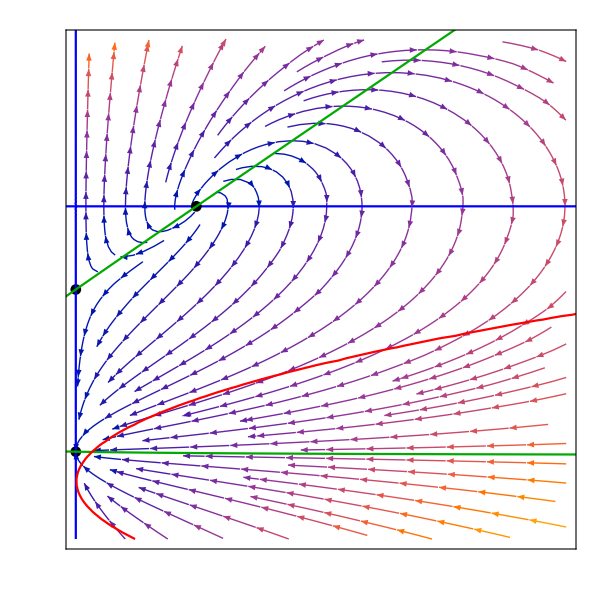

```mathematica
(*Show the plots of the phase space and its components together*)
Show[PhaseSpacexzSpiral,FPsxzSpiral,zLineSpiral,xLineSpiral,AccnxzSpiral,xzFormat,PlotRange->{{0,3},{-1,5}}]
```

### Non-Compact x - y - z Phase Space

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, dark matter, z, and the Hubble parameter, y*)
dex:=x'=-3*y*(x-ℛ)*(1+wx+ϵ*x)-q*x*y*z
dey:=y'=-y^2-(1/6)*(z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2) 
dez:=z'=-3*y*z + q*x*y*z
```

```mathematica
(*Find the fixed points of the system*)
FPsSpiral=Solve[{dex==0,dey==0,dez==0},{x,y,z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0.,z→0.0125 (6.+37. x+60. x^2)},{x→0.05,y→-0.129099,z→0.},{x→0.05,y→0.129099,z→0.},{x→2.,y→-0.816497,z→0.},{x→2.,y→0.816497,z→0.},{x→3.,y→-1.11617,z→0.7375},{x→3.,y→1.11617,z→0.7375}}

```mathematica
(*Extract the values for the fixed points and put them into a common variable name*)
FPSpiral[1]={x,y/.FPsSpiral[[1,1]],z/.FPsSpiral[[1,2]]};
FPSpiral[2]={x/.FPsSpiral[[2,1]],y/.FPsSpiral[[2,2]],z/.FPsSpiral[[2,3]]};
FPSpiral[3]={x/.FPsSpiral[[3,1]],y/.FPsSpiral[[3,2]],z/.FPsSpiral[[3,3]]};
FPSpiral[4]={x/.FPsSpiral[[4,1]],y/.FPsSpiral[[4,2]],z/.FPsSpiral[[4,3]]};
FPSpiral[5]={x/.FPsSpiral[[5,1]],y/.FPsSpiral[[5,2]],z/.FPsSpiral[[5,3]]};
FPSpiral[6]={x/.FPsSpiral[[6,1]],y/.FPsSpiral[[6,2]],z/.FPsSpiral[[6,3]]};
FPSpiral[7]={x/.FPsSpiral[[7,1]],y/.FPsSpiral[[7,2]],z/.FPsSpiral[[7,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPsSpiral=Table[FPSpiral[i],{i,1,7}];
```

```mathematica
(*Find the 3D Jacobian matrix. D[] differentiates each expression*)
JxyzSpiral=Simplify[{{D[dex,x],D[dex,y],D[dex,z]}, {D[dey,x],D[dey,y],D[dey,z]},{D[dez,x],D[dez,y],D[dez,z]}}];
JxyzSpiral//MatrixForm
```

(y (-1.5375+1.5 x-1. z) | 0.075+0.75 x^2-1. x (1.5375+z) | -x y
0.0770833+0.25 x | -2 y | -1/6
y z | (-3+x) z | (-3+x) y)

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableSpiral=Table[{FPsSpiral[[i]]//MatrixForm,Simplify[JxyzSpiral/.{x->FPsSpiral[[i,1]],y->FPsSpiral[[i,2]],z->FPsSpiral[[i,3]]}]//MatrixForm,Eigenvalues[JxyzSpiral/.{x->FPsSpiral[[i,1]],y->FPsSpiral[[i,2]],z->FPsSpiral[[i,3]]}]//MatrixForm,Eigenvectors[JxyzSpiral/.{x->FPsSpiral[[i,1]],y->FPsSpiral[[i,2]],z->FPsSpiral[[i,3]]}]//MatrixForm},{i,1,7}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTablexyzSpiral=TableForm[FPTableSpiral,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
0.
0.0125 (6.+37. x+60. x^2)) | (0. | 0.075-1.6125 x+0.2875 x^2-0.75 x^3 | 0.
0.0770833+0.25 x | 0. | -1/6
0. | -0.225-1.3125 x-1.7875 x^2+0.75 x^3 | 0.) | (0
-√(0.0432812+0.113203 x-0.0830469 x^2-0.110937 x^3-0.1875 x^4)
√(0.0432812+0.113203 x-0.0830469 x^2-0.110937 x^3-0.1875 x^4)) | (0.666667/(0.308333+1. x) | 0 | 1.
-(1. (-0.0308333+0.562917 x+2.03181 x^2-0.075 x^3+1. x^4))/((0.308333+1. x) (-0.3-1.75 x-2.38333 x^2+1. x^3)) | -(1.33333 √(0.0432813+0.113203 x-0.0830469 x^2-0.110938 x^3-0.1875 x^4))/(-0.3-1.75 x-2.38333 x^2+1. x^3) | 1.
-(1. (-0.0308333+0.562917 x+2.03181 x^2-0.075 x^3+1. x^4))/((0.308333+1. x) (-0.3-1.75 x-2.38333 x^2+1. x^3)) | (1.33333 √(0.0432813+0.113203 x-0.0830469 x^2-0.110938 x^3-0.1875 x^4))/(-0.3-1.75 x-2.38333 x^2+1. x^3) | 1.)
(0.05
-0.129099
0.) | (0.188808 | 0. | 0.00645497
0.0895833 | 0.258199 | -1/6
0. | 0. | 0.380843) | (0.380843
0.258199
0.188808) | (0.0201538 | -0.800065 | 0.599574
0. | 1. | 0.
0.612372 | -0.790569 | 0.)
(0.05
0.129099
0.) | (-0.188808 | 0. | -0.00645497
0.0895833 | -0.258199 | -1/6
0. | 0. | -0.380843) | (-0.380843
-0.258199
-0.188808) | (0.0201538 | 0.800065 | 0.599574
0. | 1. | 0.
0.612372 | 0.790569 | 0.)
(2.
-0.816497
0.) | (-1.19413 | 0. | 1.63299
0.577083 | 1.63299 | -1/6
0. | 0. | 0.816497) | (1.63299
-1.19413
0.816497) | (0. | 1. | 0.
0.979796 | -0.2 | 0.
0.605959 | -0.275985 | 0.746087)
(2.
0.816497
0.) | (1.19413 | 0. | -1.63299
0.577083 | -1.63299 | -1/6
0. | 0. | -0.816497) | (-1.63299
1.19413
-0.816497) | (0. | 1. | 0.
0.979796 | 0.2 | 0.
0.605959 | 0.275985 | 0.746087)
(3.
-1.11617
0.7375) | (-2.48348 | -8.88178×10^-16 | 3.34851
0.827083 | 2.23234 | -1/6
-0.823175 | 0. | 0.) | (2.23234+0. ⅈ
-1.24174+1.10204 ⅈ
-1.24174-1.10204 ⅈ) | (-8.17767×10^-17+0. ⅈ | 1.+0. ⅈ | 1.5283×10^-16+0. ⅈ
0.880401+0. ⅈ | -0.180212-0.0432659 ⅈ | 0.326482+0.289752 ⅈ
0.880401+0. ⅈ | -0.180212+0.0432659 ⅈ | 0.326482-0.289752 ⅈ)
(3.
1.11617
0.7375) | (2.48348 | -8.88178×10^-16 | -3.34851
0.827083 | -2.23234 | -1/6
0.823175 | 0. | 0.) | (-2.23234+0. ⅈ
1.24174+1.10204 ⅈ
1.24174-1.10204 ⅈ) | (-8.17767×10^-17+0. ⅈ | -1.+0. ⅈ | 1.5283×10^-16+0. ⅈ
0.880401+0. ⅈ | 0.180212-0.0432659 ⅈ | 0.326482-0.289752 ⅈ
0.880401+0. ⅈ | 0.180212+0.0432659 ⅈ | 0.326482+0.289752 ⅈ)

```mathematica
(*Plot the line of Einstein fixed points*)
EinsteinPointLineSpiral=ParametricPlot3D[{FPSpiral[1][[1]],FPSpiral[1][[2]],FPSpiral[1][[3]]},{x,0,15},PlotStyle->Red];
```

```mathematica
(*Plot the fixed points of the system*)
FPsxyzSpiral=ListPointPlot3D[Table[FPSpiral[i],{i,2,7}],PlotStyle->Black];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
AccnxyzSpiral=ContourPlot3D[z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2==0,{x,0,12},{y,-10,10},{z,0,12},ContourStyle->{Red,Opacity[0.25]},Mesh->None];
```

```mathematica
(*Plot the x-y-z phase space*)
PhaseSpacexyzSpiral=StreamPlot3D[{dex,dey,dez},{x,0,15},{y,-5,5},{z,0,10},AxesLabel->{"x","y","z"}];
```

```mathematica
(*Show the phase space and its components together*)
Show[PhaseSpacexyzSpiral,FPsxyzSpiral,EinsteinPointLineSpiral,AccnxyzSpiral,AxesLabel->{MaTeX["x",FontSize->20],MaTeX["y",FontSize->20],MaTeX["z",FontSize->20]},Ticks->{{0.,5.,10.},{-5.,0.,1.,5.},{0.,5.,10.}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}]
```

-Graphics3D-

## Plot the constant x0 and z0 surfaces

### Set-up for the phase spaces

```mathematica
(*Define a format for the x-y-z phase spaces*)
xyzFormat={AxesLabel->{MaTeX["x",FontSize->20],MaTeX["y",FontSize->20],MaTeX["z",FontSize->20]},Ticks->{{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.},{-5.,-4.,-3.,-2.,-1.,0.,1.,2.,3.,4.,5.},{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}};
```

```mathematica
(*Define the system of differential equations for the dark energy, x, and dark matter, z*)
dext:=x1'[t]==-3*y1[t]*(x1[t]-ℛ)*(1+wx+ϵ*x1[t])-q*x1[t]*y1[t]*z1[t]
deyt:=y1'[t]==-y1[t]^2-(1/6)*(z1[t]+x1[t]*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x1[t]^2) 
dezt:=z1'[t]==-3*y1[t]*z1[t] + q*x1[t]*y1[t]*z1[t]
```

```mathematica
(*Define Ωx0 and Ωm0 using data from Planck 2018*)
Ωx0=0.6889;
Ωm0=0.3111;
```

```mathematica
(*Set a value for α, which sets the value of the low energy cosmological constant*)
α=0.5;
```

```mathematica
(*Define the initial conditions, where a0 = 1 and K is defined as k/ρ* *)
(*Trajectories are plotted on a constant x0-z0 surface, where x0 is fixed for all cases and z0 is fixed for each phase space*)
(*K and y0 differ for each trajectory in each phase space*)

x0=ℛ/α;
y0=Sqrt[x0/3+z0/3-K];
```

```mathematica
(*Define values of K using the range of Ωk0 allowed by Planck 2018*)
Ωk0Open=0.003;
Ωk0Closed=-0.001;

KDensityParametersOpen=-Ωk0Open*ℛ/(3*α*Ωx0)
KDensityParametersClosed=-Ωk0Closed*ℛ/(3*α*Ωx0)
```

-0.000145159

0.0000483863

### Plot the Flat Friedmann Separatrix (FFS)

```mathematica
(*Define the Friedmann equation when K = 0*)
yFFS=Sqrt[x/3+z/3];
```

```mathematica
(*Plot the FFS*)
FFSPlot=ParametricPlot3D[{{x,yFFS,z},{x,-yFFS,z}},{x,0,3},{z,0,3},PlotStyle->{Darker[Green]},Mesh->None];
```

```mathematica
(*Show the FFS*)
Show[FFSPlot,xyzFormat]
```

-Graphics3D-

### Limiting Case with 1 Einstein fixed point

#### Find the Einstein Fixed Point

```mathematica
(*Fix z0 so that there is one Einstein fixed point on the surface*)
z0LimitingSpiral=0.007;
```

```mathematica
(*Substitute z0Limiting into y0 for this case*)
y0LimitingSpiral=y0/.z0->z0LimitingSpiral
```

√(0.0356667-K)

```mathematica
(*Numerically solve the system of equations using the initial conditions defined for the limiting case with one Einstein fixed point*)
trajLimitingSpiral[K_]=NDSolve[{dext,deyt,dezt,x1[0]==x0,y1[0]==y0LimitingSpiral,z1[0]==z0LimitingSpiral},{x1,y1,z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition √(0.0356667-1. K) is not a number or a rectangular array of numbers.

NDSolve[{x1'[t]==-3 (0.5-0.25 x1[t]) (-0.05+x1[t]) y1[t]-x1[t] y1[t] z1[t],y1'[t]==-y1[t]^2+1/6 (0.075+0.4625 x1[t]+0.75 x1[t]^2-z1[t]),z1'[t]==-3 y1[t] z1[t]+x1[t] y1[t] z1[t],x1[0]==0.1,y1[0]==√(0.0356667-K),z1[0]==0.007},{x1,y1,z1},{t,-100,100}]

```mathematica
(*Set-up tables of all x1 and z1 values to be used to find the x and z value of the Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
xTableSolLimitingSpiral=Table[x1[i]/.trajLimitingSpiral[0],{i,-100,100,.01}];
zTableSolLimitingSpiral=Table[z1[i]/.trajLimitingSpiral[0],{i,-100,100,.01}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSolLimitingSpiral=(zTableSolLimitingSpiral)+(xTableSolLimitingSpiral)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSolLimitingSpiral)^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSolLimiting that is closest to zero. When EinsteinPlotValuesSolLimiting = 0 (y = 0), there is an Einstein point*)
NearestToZeroLimitingSpiral=Flatten[Nearest[EinsteinPlotValuesSolLimitingSpiral,0]]
```

{-0.00951799}

```mathematica
(*Find the position of NearestToZeroLimiting in the EinsteinPlotValuesSolLimiting array*)
PositionNearestToZeroLimitingSpiral=Flatten[Position[EinsteinPlotValuesSolLimitingSpiral,NearestToZeroLimitingSpiral]]
```

{9448}

```mathematica
(*Find the Einstein point by finding the x and z values in xTableSolLimiting and zTableSolLimiting at PositionNearestToZeroLimiting*)
EinsteinPointLimitingSpiral=Flatten[{xTableSolLimitingSpiral[[PositionNearestToZeroLimitingSpiral]],0,zTableSolLimitingSpiral[[PositionNearestToZeroLimitingSpiral]]}]
```

{0.6893,0,0.740634}

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for the Einstein fixed point*)
EinsteinTableLimitingSpiral=Table[{EinsteinPointLimitingSpiral//MatrixForm,Simplify[JxyzSpiral/.{x->EinsteinPointLimitingSpiral[[1]],y->EinsteinPointLimitingSpiral[[2]],z->EinsteinPointLimitingSpiral[[3]]}]//MatrixForm,Eigenvalues[JxyzSpiral/.{x->EinsteinPointLimitingSpiral[[1]],y->EinsteinPointLimitingSpiral[[2]],z->EinsteinPointLimitingSpiral[[3]]}]//MatrixForm,Eigenvectors[JxyzSpiral/.{x->EinsteinPointLimitingSpiral[[1]],y->EinsteinPointLimitingSpiral[[2]],z->EinsteinPointLimitingSpiral[[3]]}]//MatrixForm},1];
```

```mathematica
(*Use TableForm to display the Einstein fixed point with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableEinsteinPointLimitingSpiral=TableForm[EinsteinTableLimitingSpiral,TableHeadings->{None,{"Einstein Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Einstein Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.6893
0
0.740634) | (0. | -1.13897 | 0.
0.249408 | 0 | -1/6
0. | -1.71138 | 0.) | (-0.0340995
0.0340995
3.30671×10^-14) | (-0.553965 | -0.0165851 | -0.832375
0.553965 | -0.0165851 | 0.832375
0.55561 | -1.60851×10^-14 | 0.831443)

```mathematica
(*Set-up tables of all x1 and z1 values with a bigger t increment*)
xTableSolLimitingFullSpiral=Table[x1[i]/.trajLimitingSpiral[0],{i,-100,100,.1}];
zTableSolLimitingFullSpiral=Table[z1[i]/.trajLimitingSpiral[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0*)
EinsteinPlotValuesSolLimitingFullSpiral=(zTableSolLimitingFullSpiral)+(xTableSolLimitingFullSpiral)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSolLimitingFullSpiral)^2;
```

```mathematica
(*Merge the xTableSolLimitingFull values and the EinsteinPlotValuesSolLimitingFull values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsLimitingSpiral=MapThread[h,{xTableSolLimitingFullSpiral,EinsteinPlotValuesSolLimitingFullSpiral}];
```

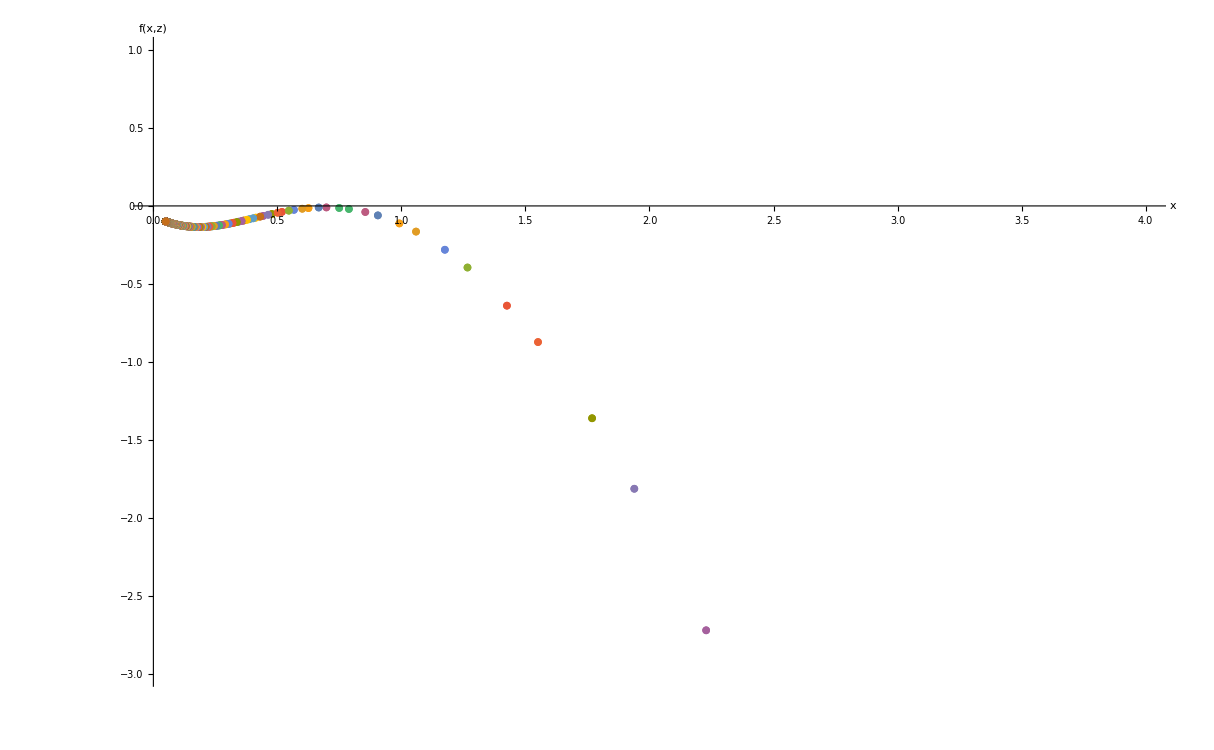

```mathematica
(*Plot x vs the remaining equation when y' = 0*)
(*When f(x,z) = 0, an Einstein point exists*)
EinsteinPlotLimitingSpiral=ListPlot[EinsteinPointSolutionsLimitingSpiral,PlotRange->{{0,4},{-3,1}},AxesLabel->{"x","f(x,z)"}]
```

#### Plot the x-y-z Phase Space

```mathematica
(*Find the maximum value of K for this combination of x0 and z0 such that y0 is not imaginary*)
KMaxLimitingSpiral=K/.Solve[y0LimitingSpiral==0,K][[1]]
```

0.0356667

```mathematica
(*Solve trajLimiting[K] for different values of K*)
```

```mathematica
solLimitingSpiral[1]=trajLimitingSpiral[KDensityParametersOpen]
```

NDSolve::ndsz: At t == -8.59273, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solLimitingSpiral[2]=trajLimitingSpiral[KDensityParametersClosed]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solLimitingSpiral[3]=trajLimitingSpiral[-.1]
```

NDSolve::ndsz: At t == -2.88294, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solLimitingSpiral[4]=trajLimitingSpiral[KMaxLimitingSpiral]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solLimitingSpiral[5]=trajLimitingSpiral[0.002]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the trajectories for the different values of K given above*)
(*Plot the solutions using a value of K found from the range of Ωk0 allowed by Planck 2018 in purple*)
```

```mathematica
trajLimitingxyzSpiral[1]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimitingSpiral[1],{t,-8.58,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingxyzSpiral[2]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimitingSpiral[2],{t,-100,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingxyzSpiral[3]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimitingSpiral[3],{t,-2.87,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingxyzSpiral[4]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimitingSpiral[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingxyzSpiral[5]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimitingSpiral[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajLimitingCaseSpiral=Table[trajLimitingxyzSpiral[i],{i,1,5}];
```

```mathematica
(*Plot the Einstein fixed point*)
EinsteinFixedPointsLimitingSpiral=ListPointPlot3D[{EinsteinPointLimitingSpiral},PlotStyle->Black];
```

```mathematica
(*Solve the x-y-z system around the Einstein fixed point to plot the Closed Friedmann Separatrix (CFS)*)
CFSLimitingSolSpiral=NDSolve[{dext,deyt,dezt,x1[0]==EinsteinPointLimitingSpiral[[1]],y1[0]==0,z1[0]==EinsteinPointLimitingSpiral[[3]]},{x1,y1,z1},{t,-100,100}]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the CFS*)
CFSLimitingSpiral=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.CFSLimitingSolSpiral,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
(*Show the x-y-z phase space*)
Show[trajLimitingCaseSpiral,EinsteinFixedPointsLimitingSpiral,CFSLimitingSpiral,AccnxyzSpiral,FPsxyzSpiral,xyzFormat,PlotRange->{{0,5},{-5,5},{0,3}}]
```

-Graphics3D-

#### Plot the x-z Projection

```mathematica
(*Plot one solution on the x-z plane*)
trajLimitingxzSpiral=ParametricPlot[Evaluate[{{z1[t],x1[t]}}/.solLimitingSpiral[1],{t,-8.58,100},PlotStyle -> {{Black, Thick,Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.03,.03,0},1]]],Arrow[x]};
```

```mathematica
(*Plot the Einstein fixed point on the x-z plane*)
EinsteinFixedPointsLimitingxzSpiral=ListPlot[{{EinsteinPointLimitingSpiral[[3]],EinsteinPointLimitingSpiral[[1]]}},PlotStyle->Black];
```

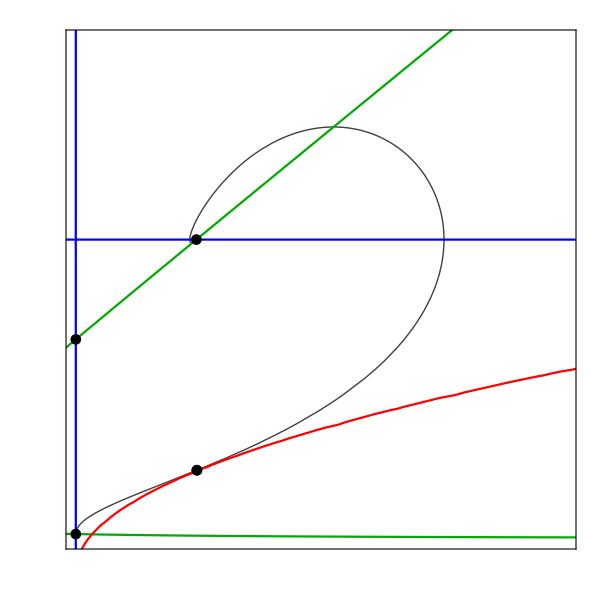

```mathematica
(*Show the x-z phase space with the a'' = 0 (red), x' = 0 (green) and z' = 0 (purple) curves*)
Show[trajLimitingxzSpiral,xLineSpiral,zLineSpiral,AccnxzSpiral,FPsxzSpiral,EinsteinFixedPointsLimitingxzSpiral,xzFormat,PlotRange->{{0,3},{0,5}}]
```

### Two Einstein Fixed Points

#### Find the Einstein Fixed Points

```mathematica
(*Fix z0 using the density parameters. In this case there are two Einstein fixed points*)
z0TwoEinsteinPointsSpiral=Ωm0*ℛ/(Ωx0*α)
```

0.0451589

```mathematica
(*Substitute z0TwoEinsteinPoints into y0 for this case*)
y0TwoEinsteinPointsSpiral=y0/.z0->z0TwoEinsteinPointsSpiral
```

√(0.0483863-K)

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajTwoEinsteinPointsSpiral[K_]=NDSolve[{dext,deyt,dezt,x1[0]==x0,y1[0]==y0TwoEinsteinPointsSpiral,z1[0]==z0TwoEinsteinPointsSpiral},{x1,y1,z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition √(0.0483863-1. K) is not a number or a rectangular array of numbers.

NDSolve[{x1'[t]==-3 (0.5-0.25 x1[t]) (-0.05+x1[t]) y1[t]-x1[t] y1[t] z1[t],y1'[t]==-y1[t]^2+1/6 (0.075+0.4625 x1[t]+0.75 x1[t]^2-z1[t]),z1'[t]==-3 y1[t] z1[t]+x1[t] y1[t] z1[t],x1[0]==0.1,y1[0]==√(0.0483863-K),z1[0]==0.0451589},{x1,y1,z1},{t,-100,100}]

```mathematica
(*Set-up tables of x1 and z1 values to be used to find the x and z value of the first Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
xTableSol1TwoEinsteinPointsSpiral=Table[x1[i]/.trajTwoEinsteinPointsSpiral[0],{i,-2,100,.01}];
zTableSol1TwoEinsteinPointsSpiral=Table[z1[i]/.trajTwoEinsteinPointsSpiral[0],{i,-2,100,.01}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol1TwoEinsteinPointsSpiral=(zTableSol1TwoEinsteinPointsSpiral)+(xTableSol1TwoEinsteinPointsSpiral)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol1TwoEinsteinPointsSpiral)^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol1TwoEinsteinPoints that is closest to zero. When EinsteinPlotValuesSol1TwoEinsteinPoints = 0 (y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints1Spiral=Flatten[Nearest[EinsteinPlotValuesSol1TwoEinsteinPointsSpiral,0]]
```

{0.000215008}

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints1 in the EinsteinPlotValuesSol1TwoEinsteinPoints*)
PositionNearestToZeroTwoEinsteinPoints1Spiral=Flatten[Position[EinsteinPlotValuesSol1TwoEinsteinPointsSpiral,NearestToZeroTwoEinsteinPoints1Spiral]]
```

{32}

```mathematica
(*Find the Einstein point by finding the x and z values in xTableSol1TwoEinsteinPoints and zTableSol1TwoEinsteinPoints at PositionNearestToZeroTwoEinsteinPoints1*)
EinsteinPoint1TwoEinsteinPointsSpiral=Flatten[{xTableSol1TwoEinsteinPointsSpiral[[PositionNearestToZeroTwoEinsteinPoints1Spiral]],0,zTableSol1TwoEinsteinPointsSpiral[[PositionNearestToZeroTwoEinsteinPoints1Spiral]]}]
```

{0.149763,0,0.161302}

```mathematica
(*Set-up tables of x1 and z1 values to be used to find the x and z value of the second Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
xTableSol2TwoEinsteinPointsSpiral=Table[x1[i]/.trajTwoEinsteinPointsSpiral[0],{i,-5.6,-3.2,.001}];
zTableSol2TwoEinsteinPointsSpiral=Table[z1[i]/.trajTwoEinsteinPointsSpiral[0],{i,-5.6,-3.2,.001}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol2TwoEinsteinPointsSpiral=(zTableSol2TwoEinsteinPointsSpiral)+(xTableSol2TwoEinsteinPointsSpiral)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol2TwoEinsteinPointsSpiral)^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol2TwoEinsteinPoints that is closest to zero. When EinsteinPlotValuesSol2TwoEinsteinPoints = 0 (y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints2Spiral=Flatten[Nearest[EinsteinPlotValuesSol2TwoEinsteinPointsSpiral,0]]
```

{0.00310612}

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints2 in the EinsteinPlotValuesSol2TwoEinsteinPoints array*)
PositionNearestToZeroTwoEinsteinPoints2Spiral=Flatten[Position[EinsteinPlotValuesSol2TwoEinsteinPointsSpiral,NearestToZeroTwoEinsteinPoints2Spiral]]
```

{1876}

```mathematica
(*Find the Einstein point by finding the x and z values in xTableSol2TwoEinsteinPoints and zTableSol2TwoEinsteinPoints at PositionNearestToZeroTwoEinsteinPoints2*)
EinsteinPoint2TwoEinsteinPointsSpiral=Flatten[{xTableSol2TwoEinsteinPointsSpiral[[PositionNearestToZeroTwoEinsteinPoints2Spiral]],0,zTableSol2TwoEinsteinPointsSpiral[[PositionNearestToZeroTwoEinsteinPoints2Spiral]]}]
```

{1.727,0,3.11374}

```mathematica
(*Put the Einstein fixed points into a common variable name*)
EinsteinPointTwoEPtsSpiral[1]=EinsteinPoint1TwoEinsteinPointsSpiral;
EinsteinPointTwoEPtsSpiral[2]=EinsteinPoint2TwoEinsteinPointsSpiral;
```

```mathematica
(*Put the Einstein fixed points into a table*)
EinsteinPointsTwoEPtsSpiral=Table[EinsteinPointTwoEPtsSpiral[i],{i,1,2}];
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each Einstein fixed point*)
EinsteinPointTableTwoEinsteinPointsSpiral=Table[{EinsteinPointsTwoEPtsSpiral[[i]]//MatrixForm,Simplify[JxyzSpiral/.{x->EinsteinPointsTwoEPtsSpiral[[i,1]],y->EinsteinPointsTwoEPtsSpiral[[i,2]],z->EinsteinPointsTwoEPtsSpiral[[i,3]]}]//MatrixForm,Eigenvalues[JxyzSpiral/.{x->EinsteinPointsTwoEPtsSpiral[[i,1]],y->EinsteinPointsTwoEPtsSpiral[[i,2]],z->EinsteinPointsTwoEPtsSpiral[[i,3]]}]//MatrixForm,Eigenvectors[JxyzSpiral/.{x->EinsteinPointsTwoEPtsSpiral[[i,1]],y->EinsteinPointsTwoEPtsSpiral[[i,2]],z->EinsteinPointsTwoEPtsSpiral[[i,3]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the Einstein fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableTwoEinsteinPointsSpiral=TableForm[EinsteinPointTableTwoEinsteinPointsSpiral,TableHeadings->{None,{"Einstein Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Einstein Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.149763
0
0.161302) | (0. | -0.162596 | 0.
0.114524 | 0 | -1/6
0. | -0.459749 | 0.) | (0.24084
-0.24084
8.53342×10^-18) | (0.298953 | -0.442814 | 0.845306
-0.298953 | -0.442814 | -0.845306
0.824179 | 1.47427×10^-16 | 0.56633)
(1.727
0
3.11374) | (0. | -5.7208 | 0.
0.508834 | 0 | -1/6
0. | -3.96379 | 0.) | (-1.33922×10^-16+1.5001 ⅈ
-1.33922×10^-16-1.5001 ⅈ
1.11057×10^-16+0. ⅈ) | (0.803522+0. ⅈ | 9.39819×10^-17-0.210699 ⅈ | 0.556739-2.03432×10^-16 ⅈ
0.803522+0. ⅈ | 9.39819×10^-17+0.210699 ⅈ | 0.556739+2.03432×10^-16 ⅈ
0.311274+0. ⅈ | 9.05767×10^-17+0. ⅈ | 0.95032+0. ⅈ)

```mathematica
(*Set-up tables of all x1 and z1 values*)
xTableSolTwoEinsteinPointsFullSpiral=Table[x1[i]/.trajTwoEinsteinPointsSpiral[0],{i,-100,100,.1}];
zTableSolTwoEinsteinPointsFullSpiral=Table[z1[i]/.trajTwoEinsteinPointsSpiral[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0*)
EinsteinPlotValuesSolTwoEinsteinPointsFullSpiral=(zTableSolTwoEinsteinPointsFullSpiral)+(xTableSolTwoEinsteinPointsFullSpiral)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSolTwoEinsteinPointsFullSpiral)^2;
```

```mathematica
(*Merge the xTableSolTwoEinsteinPointsFull values and the EinsteinPlotValuesSolTwoEinsteinPointsFull values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsTwoEinsteinPointsSpiral=MapThread[h,{xTableSolTwoEinsteinPointsFullSpiral,EinsteinPlotValuesSolTwoEinsteinPointsFullSpiral}];
```

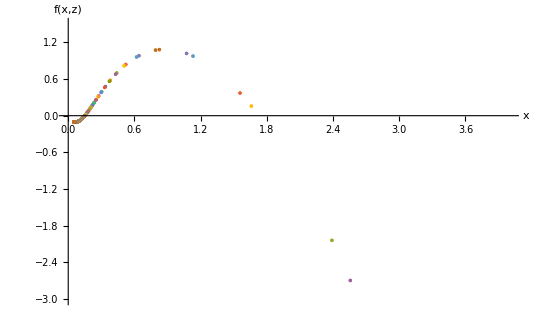

```mathematica
(*Plot x vs the remaining equation when y' = 0*)
(*When f(x,z) = 0, an Einstein point exists*)
EinsteinPlotTwoEinsteinPointsSpiral=ListPlot[EinsteinPointSolutionsTwoEinsteinPointsSpiral,PlotRange->{{0,4},{-3,1.5}},AxesLabel->{"x","f(x,z)"}]
```

#### Plot the x-y-z Phase Space

```mathematica
(*Find the maximum value of K for this combination of x0 and z0 so that y0 is not imaginary*)
KMaxTwoEinsteinPointsSpiral=K/.Flatten[Solve[y0TwoEinsteinPointsSpiral==0,K]]
```

0.0483863

```mathematica
(*Solve trajTwoEinsteinPoints[K] for different values of K*)
```

```mathematica
solTwoEinsteinPointsSpiral[1]=trajTwoEinsteinPointsSpiral[KDensityParametersOpen]
```

NDSolve::ndsz: At t == -6.68211, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsSpiral[2]=trajTwoEinsteinPointsSpiral[KDensityParametersClosed]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsSpiral[3]=trajTwoEinsteinPointsSpiral[-.1]
```

NDSolve::ndsz: At t == -2.6552, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsSpiral[4]=trajTwoEinsteinPointsSpiral[KMaxTwoEinsteinPointsSpiral]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsSpiral[5]=trajTwoEinsteinPointsSpiral[0.005]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the trajectories for the different values of K given above*)
(*Plot the solutions using a value of K found from the range of Ωk0 allowed by Planck 2018 in purple*)
```

```mathematica
trajTwoEinsteinPointsxyzSpiral[1]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsSpiral[1],{t,-6.67,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyzSpiral[2]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsSpiral[2],{t,-100,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyzSpiral[3]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsSpiral[3],{t,-2.65,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyzSpiral[4]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsSpiral[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75],Dashed}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
trajTwoEinsteinPointsxyzSpiral[5]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsSpiral[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Solve the x-y-z system using the centre Einstein fixed point for x0 and z0 to plot a cyclic trajectory*)
CyclicTrajTwoEinsteinPointsSpiral=NDSolve[{dext,deyt,dezt,x1[0]==EinsteinPoint2TwoEinsteinPointsSpiral[[1]],y1[0]==0.436,z1[0]==EinsteinPoint2TwoEinsteinPointsSpiral[[3]]},{x1,y1,z1},{t,-100,100}];
```

```mathematica
(*Plot the cyclic trajectory*)
trajTwoEinsteinPointsxyzSpiral[6]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.CyclicTrajTwoEinsteinPointsSpiral,{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajTwoEinsteinPointsCaseSpiral=Table[trajTwoEinsteinPointsxyzSpiral[i],{i,1,6}];
```

```mathematica
(*Plot the Einstein fixed points*)
EinsteinFixedPointsTwoEinsteinPointsSpiral=ListPointPlot3D[{EinsteinPoint1TwoEinsteinPointsSpiral,EinsteinPoint2TwoEinsteinPointsSpiral},PlotStyle->Black];
```

```mathematica
(*Solve the x-y-z system around the Einstein fixed point to plot the Closed Friedmann Separatrix (CFS)*)
CFSTwoEinsteinPointsSolSpiral=NDSolve[{dext,deyt,dezt,x1[0]==EinsteinPoint1TwoEinsteinPointsSpiral[[1]],y1[0]==-0.0005,z1[0]==EinsteinPoint1TwoEinsteinPointsSpiral[[3]]},{x1,y1,z1},{t,-100,100}]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the CFS*)
CFSTwoEinsteinPointsSpiral=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.CFSTwoEinsteinPointsSolSpiral,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Show the x-y-z phase space*)
Show[trajTwoEinsteinPointsCaseSpiral,CFSTwoEinsteinPointsSpiral,EinsteinFixedPointsTwoEinsteinPointsSpiral,AccnxyzSpiral,FPsxyzSpiral,xyzFormat,PlotRange->{{0,5},{-5,5},{0,4}}]
```

-Graphics3D-

#### Plot the x-z Projection

```mathematica
(*Plot one solution on the x-z plane*)
trajTwoEinsteinPointsxzSpiral=ParametricPlot[Evaluate[{{z1[t],x1[t]}}/.solTwoEinsteinPointsSpiral[1],{t,-6.67,100},PlotStyle -> {{Black, Thick,Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.03,.03,.03,0},1]]],Arrow[x]};;
```

```mathematica
(*Plot the Einstein fixed points on the x-z plane*)
EinsteinFixedPointsTwoEinsteinPointsxzSpiral=ListPlot[{{EinsteinPoint1TwoEinsteinPointsSpiral[[3]],EinsteinPoint1TwoEinsteinPointsSpiral[[1]]},{EinsteinPoint2TwoEinsteinPointsSpiral[[3]],EinsteinPoint2TwoEinsteinPointsSpiral[[1]]}},PlotStyle->Black];
```

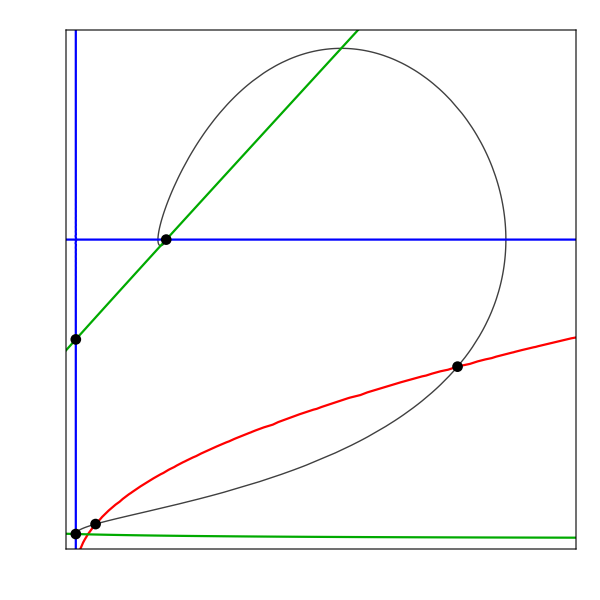

```mathematica
(*Show the x-z phase space with the a'' = 0 (red), x' = 0 (green) and z' = 0 (purple) curves*)
Show[trajTwoEinsteinPointsxzSpiral,AccnxzSpiral,xLineSpiral,zLineSpiral,FPsxzSpiral,EinsteinFixedPointsTwoEinsteinPointsxzSpiral,xzFormat,PlotRange->{{0,4},{0,5}}]
```

### No Einstein Fixed Points

#### Plot to show that there are no Einstein fixed points

```mathematica
(*Fix z0 such that there are no Einstein fixed points on the surface*)
z0NoEinsteinPointsSpiral=0.005;
```

```mathematica
(*Substitute z0NoEinsteinPoints into y0 for this case*)
y0NoEinsteinPointsSpiral=y0/.z0->z0NoEinsteinPointsSpiral
```

√(0.035-K)

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajNoEinsteinPointsSpiral[K_]=NDSolve[{dext,deyt,dezt,x1[0]==x0,y1[0]==y0NoEinsteinPointsSpiral,z1[0]==z0NoEinsteinPointsSpiral},{x1,y1,z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition √(0.035-1. K) is not a number or a rectangular array of numbers.

NDSolve[{x1'[t]==-3 (0.5-0.25 x1[t]) (-0.05+x1[t]) y1[t]-x1[t] y1[t] z1[t],y1'[t]==-y1[t]^2+1/6 (0.075+0.4625 x1[t]+0.75 x1[t]^2-z1[t]),z1'[t]==-3 y1[t] z1[t]+x1[t] y1[t] z1[t],x1[0]==0.1,y1[0]==√(0.035-K),z1[0]==0.005},{x1,y1,z1},{t,-100,100}]

```mathematica
(*Set-up tables of all x1 and z1 values*)
xTableSolNoEinsteinPointsFullSpiral=Table[x1[i]/.trajNoEinsteinPointsSpiral[0],{i,-100,100,.1}];
zTableSolNoEinsteinPointsFullSpiral=Table[z1[i]/.trajNoEinsteinPointsSpiral[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0*)
EinsteinPlotValuesSolNoEinsteinPointsFullSpiral=(zTableSolNoEinsteinPointsFullSpiral)+(xTableSolNoEinsteinPointsFullSpiral)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSolNoEinsteinPointsFullSpiral)^2;
```

```mathematica
(*Merge the xTableSolNoEinsteinPointsFull values and the EinsteinPlotValuesSolNoEinsteinPointsFull values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsNoEinsteinPointsSpiral=MapThread[h,{xTableSolNoEinsteinPointsFullSpiral,EinsteinPlotValuesSolNoEinsteinPointsFullSpiral}];
```

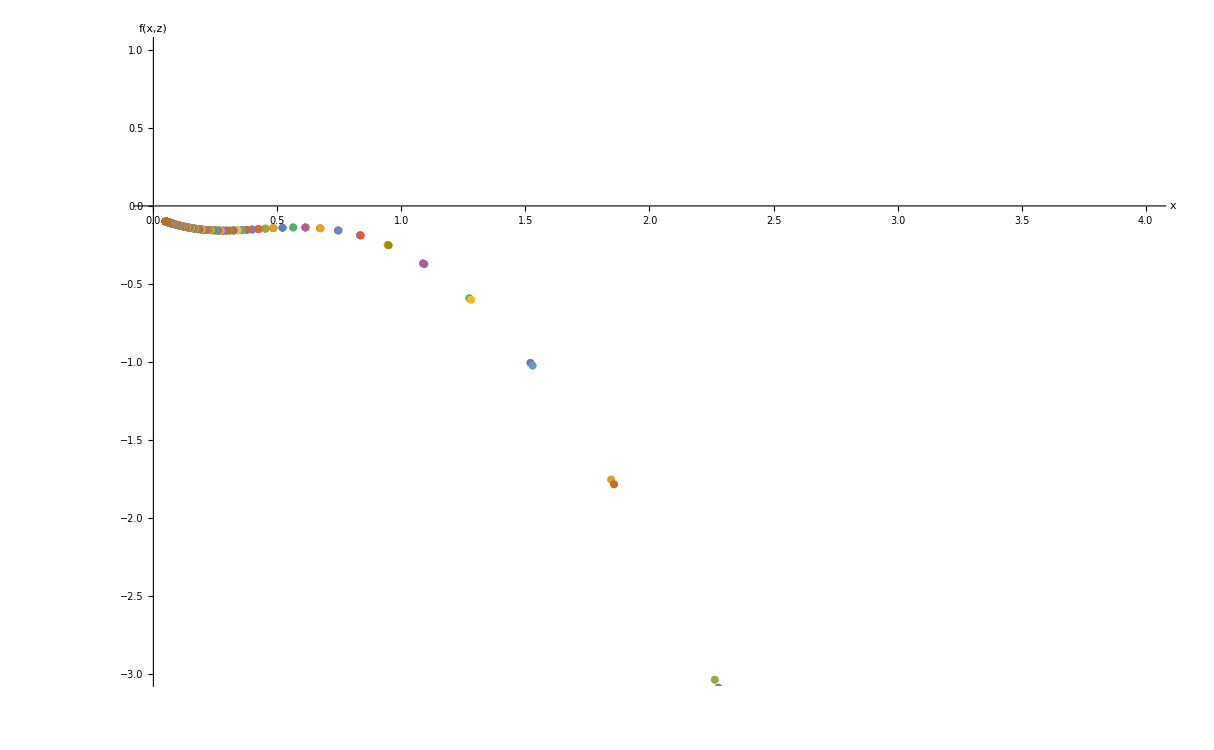

```mathematica
(*Plot x vs the remaining equation when y' = 0*)
(*Here, f(x,z) is never zero, so there are no Einstein fixed points*)
EinsteinPlotNoEinsteinPointsSpiral=ListPlot[EinsteinPointSolutionsNoEinsteinPointsSpiral,PlotRange->{{0,4},{-3,1}},AxesLabel->{"x","f(x,z)"}]
```

#### Plot the x-y-z Phase Space

```mathematica
(*Find the maximum value of K for this combination of x0 and z0 such that y0 is not imaginary*)
KMaxNoEinsteinPointsSpiral=K/.Solve[y0NoEinsteinPointsSpiral==0,K][[1]]
```

0.035

```mathematica
(*Solve trajNoEinsteinPoints[K] for different values of K*)
```

```mathematica
solNoEinsteinPointsSpiral[1]=trajNoEinsteinPointsSpiral[KDensityParametersOpen]
```

NDSolve::ndsz: At t == -8.89261, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsSpiral[2]=trajNoEinsteinPointsSpiral[KDensityParametersClosed]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsSpiral[3]=trajNoEinsteinPointsSpiral[-.1]
```

NDSolve::ndsz: At t == -2.89968, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsSpiral[4]=trajNoEinsteinPointsSpiral[0.01]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsSpiral[5]=trajNoEinsteinPointsSpiral[KMaxNoEinsteinPointsSpiral]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the trajectories for the different values of K given above.*)
(*Plot the solutions using a value of K found from the range of Ωk0 allowed by Planck 2018 in purple*)
```

```mathematica
trajNoEinsteinPointsxyzSpiral[1]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPointsSpiral[1],{t,-8.89,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsxyzSpiral[2]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPointsSpiral[2],{t,-100,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsxyzSpiral[3]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPointsSpiral[3],{t,-2.89,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsxyzSpiral[4]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPointsSpiral[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsxyzSpiral[5]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPointsSpiral[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajNoEinsteinPointsPlotsSpiral=Table[trajNoEinsteinPointsxyzSpiral[i],{i,1,5}];
```

```mathematica
(*Show the x-y-z phase space*)
Show[trajNoEinsteinPointsPlotsSpiral,AccnxyzSpiral,FPsxyzSpiral,xyzFormat,PlotRange->{{0,4.5},{-5,5},{0,2.5}}]
```

-Graphics3D-

#### Plot the x-z Projection

```mathematica
(*Plot one solution on the x-z plane*)
trajNoEinsteinPointsxzSpiral=ParametricPlot[Evaluate[{{z1[t],x1[t]}}/.solNoEinsteinPointsSpiral[1],{t,-8.89,100},PlotStyle -> {{Black,Thick, Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.03,.03,0},1]]],Arrow[x]};
```

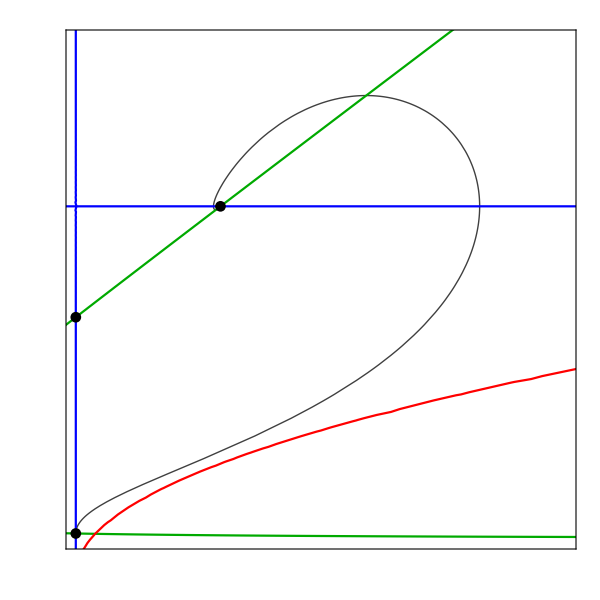

```mathematica
(*Show the x-z phase space with the a'' = 0 (red), x' = 0 (green) and z' = 0 (purple) curves*)
Show[trajNoEinsteinPointsxzSpiral,xLineSpiral,zLineSpiral,AccnxzSpiral,FPsxzSpiral,xzFormat,PlotRange->{{0,2.5},{0,4.5}}]
```

## Compact Phase Spaces: constant X0 and Z0 surfaces

### Define parameter values and set-up initial conditions

```mathematica
(*Set parameter values*)
wx=-0.5;
q=1;
ϵ=-0.25;
ℛ=0.05;
```

```mathematica
(*Define Ωx0 and Ωm0 using data from Planck 2018*)
Ωx0=0.6889;
Ωm0=0.3111;
```

```mathematica
(*Set a value for α, which sets the value of the low energy cosmological constant*)
α=0.5;
```

```mathematica
(*Define the initial conditions, where a0 = 1 and K is defined as k/ρ* *)

x0=ℛ/α;
y0=Sqrt[x0/3+Z0/(3*(1-Z0))-K];
```

```mathematica
(*Compactify the initial conditions*)
(*Trajectories are plotted on a constant X0-Z0 surface, where X0 is fixed for all cases and Z0 is fixed for each phase space*)
(*K and Y0 differ for each trajectory in each phase space*)

X0=x0/(1+x0);
Y0=y0/Sqrt[1+y0^2];
```

```mathematica
(*Define values of K using the range of Ωk0 allowed by Planck 2018*)
Ωk0Open=0.003;
Ωk0Closed=-0.001;

KDensityParametersOpen=-Ωk0Open*ℛ/(3*α*Ωx0)
KDensityParametersClosed=-Ωk0Closed*ℛ/(3*α*Ωx0)
```

-0.000145159

0.0000483863

### Set-up for the compact X-Y-Z system

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*Define a format style for the X-Y-Z phase spaces*)
XYZCompactFormat={AxesLabel->{MaTeX["X",FontSize->22],MaTeX["Y",FontSize->22],MaTeX["Z",FontSize->22]},Ticks->{{0.,0.5,1.0},{-1,-0.5,0.,0.5,1.0},{0.,0.5,1.0}},PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->22}};
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y*)
deX:=X'=-3*(Y/((1-Y^2)^(1/2)))*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))*(Y/((1-Y^2)^(1/2)))
deY:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)
deZ:=Z'=-3*Z*(1-Z)*(Y/((1-Y^2)^(1/2))) + q*(X/(1-X))*Z*(1-Z)*(Y/((1-Y^2)^(1/2)))
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y in terms of time, t*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*(X1[t]-ℛ*(1-X1[t]))*((1+wx)*(1-X1[t])+ϵ*X1[t])-q*X1[t]*(1-X1[t])*(Z1[t]/(1-Z1[t]))*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((Z1[t]/(1-Z1[t]))+(X1[t]/(1-X1[t]))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X1[t]^2/((1-X1[t])^2))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2))) + q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
```

```mathematica
(*Find the fixed points of the system*)
FPsXYZSpiral=Solve[{deX==0,deY==0,deZ==0},{X,Y,Z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Y→0.,Z→(6.+25. X+29. X^2)/(86.-135. X+109. X^2)},{X→0.666667,Y→-0.632456,Z→0.},{X→0.047619,Y→-0.128037,Z→0.},{X→-0.431034-0.145278 ⅈ,Y→0.,Z→0.},{X→-0.431034+0.145278 ⅈ,Y→0.,Z→0.},{X→0.047619,Y→0.128037,Z→0.},{X→0.666667,Y→0.632456,Z→0.},{X→0.75,Y→-0.744803,Z→0.42446},{X→0.75,Y→0.744803,Z→0.42446},{X→0.75,Y→0.,Z→0.891452}}

```mathematica
(*Extract the values of the fixed points and put them into a common variable name*)
FPXYZSpiral[1]={X,Y/.FPsXYZSpiral[[1,1]],Z/.FPsXYZSpiral[[1,2]]};
FPXYZSpiral[2]={X/.FPsXYZSpiral[[2,1]],Y/.FPsXYZSpiral[[2,2]],Z/.FPsXYZSpiral[[2,3]]};
FPXYZSpiral[3]={X/.FPsXYZSpiral[[3,1]],Y/.FPsXYZSpiral[[3,2]],Z/.FPsXYZSpiral[[3,3]]};
FPXYZSpiral[4]={X/.FPsXYZSpiral[[6,1]],Y/.FPsXYZSpiral[[6,2]],Z/.FPsXYZSpiral[[6,3]]};
FPXYZSpiral[5]={X/.FPsXYZSpiral[[7,1]],Y/.FPsXYZSpiral[[7,2]],Z/.FPsXYZSpiral[[7,3]]};
FPXYZSpiral[6]={X/.FPsXYZSpiral[[8,1]],Y/.FPsXYZSpiral[[8,2]],Z/.FPsXYZSpiral[[8,3]]};
FPXYZSpiral[7]={X/.FPsXYZSpiral[[9,1]],Y/.FPsXYZSpiral[[9,2]],Z/.FPsXYZSpiral[[9,3]]};
FPXYZSpiral[8]={X/.FPsXYZSpiral[[10,1]],Y/.FPsXYZSpiral[[10,2]],Z/.FPsXYZSpiral[[10,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPXYZTableSpiral=Table[FPXYZSpiral[i],{i,1,8}];
```

```mathematica
(*Find the 3D Jacobian matrix. D[] differentiates each expression*)
JCompactXYZSpiral=Simplify[{{D[deX,X],D[deX,Y],D[deX,Z]},{D[deY,X],D[deY,Y],D[deY,Z]},{D[deZ,X],D[deZ,Y],D[deZ,Z]}}];
JCompactXYZSpiral//MatrixForm
```

((Y (1.6875-0.6875 Z+X (-4.725+2.725 Z)))/(√(1-Y^2) (-1.+Z)) | (0.075+X^2 (2.3625-1.3625 Z)+X (-1.6875+0.6875 Z)-0.075 Z)/(√(1-Y^2) (-1.+Y^2) (-1.+Z)) | ((-1+X) X Y)/(√(1-Y^2) (-1+Z)^2)
(0.172917 (0.445783+1. X) √(1-Y^2) (-1.+Y^2))/(-1.+X)^3 | (Y (2.0375-2.5375 Z+Y^2 (-3.0375+3.5375 Z)+X (-3.84375+Y^2 (5.84375-6.84375 Z)+4.84375 Z)+X^2 (2.18125-2.68125 Z+Y^2 (-3.18125+3.68125 Z))))/((-1.+X)^2 √(1-Y^2) (-1.+Z)) | -((1-Y^2)^(3/2))/(6 (-1+Z)^2)
-(Y (-1+Z) Z)/((-1+X)^2 √(1-Y^2)) | ((-3+4 X) (-1+Z) Z)/((-1+X) (1-Y^2)^(3/2)) | ((-3+4 X) Y (-1+2 Z))/((-1+X) √(1-Y^2)))

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableCompactSpiral=Table[{FPXYZTableSpiral[[i]]//MatrixForm,Simplify[JCompactXYZSpiral/.{X->FPXYZTableSpiral[[i,1]],Y->FPXYZTableSpiral[[i,2]],Z->FPXYZTableSpiral[[i,3]]}]//MatrixForm,Eigenvalues[JCompactXYZSpiral/.{X->FPXYZTableSpiral[[i,1]],Y->FPXYZTableSpiral[[i,2]],Z->FPXYZTableSpiral[[i,3]]}]//MatrixForm,Eigenvectors[JCompactXYZSpiral/.{X->FPXYZTableSpiral[[i,1]],Y->FPXYZTableSpiral[[i,2]],Z->FPXYZTableSpiral[[i,3]]}]//MatrixForm},{i,1,8}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableXYZSpiral=TableForm[FPTableCompactSpiral,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(X
0.
(6.+25. X+29. X^2)/(86.-135. X+109. X^2)) | (0. | (0.075-1.9125 X+5.575 X^2-6.4625 X^3+2.725 X^4)/(1.-2. X+1. X^2) | 0.
(-0.0770833-0.172917 X)/(-1.+X)^3 | 0. | -(0.309401 (0.788991-1.23853 X+1. X^2)^2)/((1.-2. X+1. X^2)^2)
0. | (0.121202+0.101002 X-0.653144 X^2-0.262604 X^3+1.47462 X^4-0.781079 X^5)/((-1.+X) (0.788991-1.23853 X+1. X^2)^2) | 0.) | (0
-(√(2.36752×10^6-3.23487×10^7 X+2.03048×10^8 X^2-7.61682×10^8 X^3+1.80853×10^9 X^4-2.3693×10^9 X^5-5.96589×10^8 X^6+1.13797×10^10 X^7-3.17438×10^10 X^8+5.67742×10^10 X^9-7.55941×10^10 X^10+7.849×10^10 X^11-6.45121×10^10 X^12+4.19172×10^10 X^13-2.12178×10^10 X^14+8.11413×10^9 X^15-2.21527×10^9 X^16+3.86202×10^8 X^17-3.24002×10^7 X^18))/((-1.+X)^4 √(1.-2. X+1. X^2) (86.-135. X+109. X^2)^2)
(√(2.36752×10^6-3.23487×10^7 X+2.03048×10^8 X^2-7.61682×10^8 X^3+1.80853×10^9 X^4-2.3693×10^9 X^5-5.96589×10^8 X^6+1.13797×10^10 X^7-3.17438×10^10 X^8+5.67742×10^10 X^9-7.55941×10^10 X^10+7.849×10^10 X^11-6.45121×10^10 X^12+4.19172×10^10 X^13-2.12178×10^10 X^14+8.11413×10^9 X^15-2.21527×10^9 X^16+3.86202×10^8 X^17-3.24002×10^7 X^18))/((-1.+X)^4 √(1.-2. X+1. X^2) (86.-135. X+109. X^2)^2)) | (-(1.78931 (-1.+X)^3 (0.788991-1.23853 X+1. X^2)^2)/((0.445783+1. X) (1.-2. X+1. X^2)^2) | 0 | 1.
-(1. (-0.0165874+0.606034 X-6.81355 X^2+40.8788 X^3-153.503 X^4+370.935 X^5-488.211 X^6-216.371 X^7+2925.39 X^8-8444.38 X^9+15943.1 X^10-22619.1 X^11+25232.4 X^12-22502.4 X^13+16080.6 X^14-9133.98 X^15+4046.6 X^16-1351.95 X^17+321.135 X^18-48.4237 X^19+3.48876 X^20))/((-1.+1. X)^6 (-0.75+1. X) (0.445783+1. X) (1.-2. X+1. X^2)^2 (0.788991-1.23853 X+1. X^2)^2 (0.206897+0.862069 X+1. X^2)) | ((0.+4.20932×10^-7 ⅈ) √(-2.48252×10^12+3.39201×10^13 X-2.12911×10^14 X^2+7.98682×10^14 X^3-1.89638×10^15 X^4+2.48439×10^15 X^5+6.25569×10^14 X^6-1.19325×10^16 X^7+3.32858×10^16 X^8-5.95321×10^16 X^9+7.92661×10^16 X^10-8.23027×10^16 X^11+6.76458×10^16 X^12-4.39534×10^16 X^13+2.22485×10^16 X^14-8.50829×10^15 X^15+2.32288×10^15 X^16-4.04963×10^14 X^17+3.39741×10^13 X^18))/((-1.+X)^3 (-1.+1. X) (-3.+4. X) (1.-2. X+1. X^2) (0.206897+0.862069 X+1. X^2)) | 1.
-(1. (-0.0165874+0.606034 X-6.81355 X^2+40.8788 X^3-153.503 X^4+370.935 X^5-488.211 X^6-216.371 X^7+2925.39 X^8-8444.38 X^9+15943.1 X^10-22619.1 X^11+25232.4 X^12-22502.4 X^13+16080.6 X^14-9133.98 X^15+4046.6 X^16-1351.95 X^17+321.135 X^18-48.4237 X^19+3.48876 X^20))/((-1.+1. X)^6 (-0.75+1. X) (0.445783+1. X) (1.-2. X+1. X^2)^2 (0.788991-1.23853 X+1. X^2)^2 (0.206897+0.862069 X+1. X^2)) | -((0.+4.20932×10^-7 ⅈ) √(-2.48252×10^12+3.39201×10^13 X-2.12911×10^14 X^2+7.98682×10^14 X^3-1.89638×10^15 X^4+2.48439×10^15 X^5+6.25569×10^14 X^6-1.19325×10^16 X^7+3.32858×10^16 X^8-5.95321×10^16 X^9+7.92661×10^16 X^10-8.23027×10^16 X^11+6.76458×10^16 X^12-4.39534×10^16 X^13+2.22485×10^16 X^14-8.50829×10^15 X^15+2.32288×10^15 X^16-4.04963×10^14 X^17+3.39741×10^13 X^18))/((-1.+X)^3 (-1.+1. X) (-3.+4. X) (1.-2. X+1. X^2) (0.206897+0.862069 X+1. X^2)) | 1.)
(0.666667
-0.632456
0.) | (-1.19413 | 0. | 0.181444
2.41384 | 1.63299 | -0.0774597
0. | 0. | 0.816497) | (1.63299
-1.19413
0.816497) | (0. | 1. | 0.
0.760506 | -0.649331 | 0.
0.0885881 | -0.168767 | 0.981667)
(0.047619
-0.128037
0.) | (0.188808 | 2.84523×10^-17 | 0.00585485
0.0963469 | 0.258199 | -0.162585
0. | 0. | 0.380843) | (0.380843
0.258199
0.188808) | (0.0185705 | -0.792875 | 0.609102
-6.61074×10^-16 | -1. | 0.
-0.584422 | 0.81145 | 0.)
(0.047619
0.128037
0.) | (-0.188808 | 2.84523×10^-17 | -0.00585485
0.0963469 | -0.258199 | -0.162585
0. | 0. | -0.380843) | (-0.380843
-0.258199
-0.188808) | (0.0185705 | 0.792875 | 0.609102
-6.61074×10^-16 | 1. | 0.
0.584422 | 0.81145 | 0.)
(0.666667
0.632456
0.) | (1.19413 | 0. | -0.181444
2.41384 | -1.63299 | -0.0774597
0. | 0. | -0.816497) | (-1.63299
1.19413
-0.816497) | (0. | 1. | 0.
0.760506 | 0.649331 | 0.
0.0885881 | 0.168767 | 0.981667)
(0.75
-0.744803
0.42446) | (-2.48348 | 0. | 0.631802
3.9319 | 2.23234 | -0.149497
-4.36277 | 0. | 0.) | (2.23234+0. ⅈ
-1.24174+1.10204 ⅈ
-1.24174-1.10204 ⅈ) | (0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ
0.25061-0.222416 ⅈ | -0.29583+0.157884 ⅈ | 0.880502+0. ⅈ
0.25061+0.222416 ⅈ | -0.29583-0.157884 ⅈ | 0.880502+0. ⅈ)
(0.75
0.744803
0.42446) | (2.48348 | 0. | -0.631802
3.9319 | -2.23234 | -0.149497
4.36277 | 0. | 0.) | (-2.23234+0. ⅈ
1.24174+1.10204 ⅈ
1.24174-1.10204 ⅈ) | (0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ
0.25061+0.222416 ⅈ | 0.29583+0.157884 ⅈ | 0.880502+0. ⅈ
0.25061-0.222416 ⅈ | 0.29583-0.157884 ⅈ | 0.880502+0. ⅈ)
(0.75
0.
0.891452) | (0. | -1.40156 | 0.
13.2333 | 0. | -14.145
0. | 0. | 0.) | (0.+4.30666 ⅈ
0.-4.30666 ⅈ
0.+0. ⅈ) | (0.-0.309465 ⅈ | -0.950911+0. ⅈ | 0.+0. ⅈ
0.+0.309465 ⅈ | -0.950911+0. ⅈ | 0.+0. ⅈ
0.730249+0. ⅈ | 0.+0. ⅈ | 0.683182+0. ⅈ)

```mathematica
(*Plot the fixed points of the system*)
FPsXYZSpiral=ListPointPlot3D[Table[FPXYZSpiral[i],{i,2,7}], PlotStyle->{Black}];
```

```mathematica
(*Extra fixed points exist when the system is compactified*)
(*Find the de Sitter fixed points at Y = +-1*)
```

```mathematica
(*Solve X' = 0 when Y = +- 1 for Z*)
ZXPrimeZeroSpiral=Z/.Solve[-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))==0,Z]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{(3. (2.-45. X+63. X^2))/(6.-55. X+109. X^2)}

```mathematica
(*Substitute Z = ZXPrimeZero into Z' at Y = +-1*)
ZPrimeSpiral=Flatten[-3*Z*(1-Z) + q*(X/(1-X))*Z*(1-Z)/.Z->ZXPrimeZeroSpiral][[1]]
```

-(9. (2.-45. X+63. X^2) (1-(3. (2.-45. X+63. X^2))/(6.-55. X+109. X^2)))/(6.-55. X+109. X^2)+(3. X (2.-45. X+63. X^2) (1-(3. (2.-45. X+63. X^2))/(6.-55. X+109. X^2)))/((1-X) (6.-55. X+109. X^2))

```mathematica
(*Solve ZPrime = 0 (Z' = 0) for X*)
XdSSolSpiral=X/.FindRoot[ZPrimeSpiral==0,{X,0.75}]
```

0.75

```mathematica
(*Subsitute XdSSol into ZXPrimeZero to find the value of Z at the fixed point*)
ZdSSolSpiral=Flatten[ZXPrimeZeroSpiral/.X->XdSSolSpiral][[1]]
```

0.42446

```mathematica
(*Plot the fixed points from compactification*)
CompactFPShowXYZSpiral=ListPointPlot3D[{{XdSSolSpiral,1,ZdSSolSpiral},{XdSSolSpiral,-1,ZdSSolSpiral}}, PlotStyle->{Black}];
```

```mathematica
(*Define the acceleration equation*)
AccnCompactSpiral=((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)/Sqrt[1+((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)^2]
```

(-0.075-(0.4625 X)/(1-X)-(0.75 X^2)/(1-X)^2+Z/(1-Z))/(√(1+(-0.075-(0.4625 X)/(1-X)-(0.75 X^2)/(1-X)^2+Z/(1-Z))^2))

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
AccnXYZSpiral=ContourPlot3D[AccnCompactSpiral==0,{X,0,1},{Y,-1,1},{Z,0,1},ContourStyle->{Red,Opacity[0.25]},Mesh->None];
```

### Set-up for the compact X-Z system

```mathematica
(*Define a format style for the X-Z phase spaces*)
XZCompactFormat={Frame->True,FrameLabel->{MaTeX["Z",FontSize->24],Rotate[MaTeX["X",FontSize->24],300]},FrameTicks->{{Table[{X,MaTeX[X,"DisplayStyle"->False,FontSize->24]},{X,0.5Range[-1,2]}],None},{Table[{Z,MaTeX[Z,"DisplayStyle"->False,FontSize->24]},{Z,0.5Range[-1,2]}],None}},PlotRange->{{0,1},{0,1}},ImageSize->{600,600},PlotRangePadding->{0.01,0}};
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, and dark matter, Z*)
deX:=X'=-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))
deZ:=Z'=-3*Z*(1-Z)+ q*(X/(1-X))*Z*(1-Z)
```

```mathematica
(*Find the fixed points of the system*)
FPsXZSpiral=Solve[{deZ==0,deX==0},{Z,X}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Z→0.,X→0.047619},{Z→0.,X→0.666667},{Z→0.42446,X→0.75}}

```mathematica
(*Extract the values of the fixed points and put them into a common variable name*)
FPXZSpiral[1]={Z/.FPsXZSpiral[[1,1]],X/.FPsXZSpiral[[1,2]]};
FPXZSpiral[2]={Z/.FPsXZSpiral[[2,1]],X/.FPsXZSpiral[[2,2]]};
FPXZSpiral[3]={Z/.FPsXZSpiral[[3,1]],X/.FPsXZSpiral[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPXZTableSpiral=Table[FPXZSpiral[i],{i,1,3}];
```

```mathematica
(*Find the 2D Jacobian matrix. D[] differentiates each expression*)
JCompactXZSpiral=Simplify[{{D[deZ,Z],D[deZ,X]},{D[deX,Z],D[deX,X]}}];
JCompactXZSpiral//MatrixForm
```

(((-3+4 X) (-1+2 Z))/(-1+X) | -((-1+Z) Z)/(-1+X)^2
((-1+X) X)/(-1+Z)^2 | (1.6875-0.6875 Z+X (-4.725+2.725 Z))/(-1.+Z))

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableCompactSpiral=Table[{FPXZTableSpiral[[i]]//MatrixForm,Simplify[JCompactXZSpiral/.{Z->FPXZTableSpiral[[i,1]],X->FPXZTableSpiral[[i,2]]}]//MatrixForm,Eigenvalues[JCompactXZSpiral/.{Z->FPXZTableSpiral[[i,1]],X->FPXZTableSpiral[[i,2]]}]//MatrixForm,Eigenvectors[JCompactXZSpiral/.{Z->FPXZTableSpiral[[i,1]],X->FPXZTableSpiral[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableXZSpiral=TableForm[FPTableCompactSpiral,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.
0.047619) | (-2.95 | 0.
-0.0453515 | -1.4625) | (-2.95
-1.4625) | (0.999536 | 0.0304742
0. | 1.)
(0.
0.666667) | (-1. | 0.
-0.222222 | 1.4625) | (1.4625
-1.) | (0. | 1.
0.995953 | 0.0898773)
(0.42446
0.75) | (0. | 3.9087
-0.566045 | 2.225) | (1.1125+0.987342 ⅈ
1.1125-0.987342 ⅈ) | (0.934613+0. ⅈ | 0.266011+0.236084 ⅈ
0.934613+0. ⅈ | 0.266011-0.236084 ⅈ)

```mathematica
(*Plot the fixed points of the system*)
FPsXZSpiral=ListPlot[FPXZTableSpiral, PlotStyle->{Black}];
```

```mathematica
(*Plot the fixed points from compactification*)
CompactFPShowXZSpiral=ListPlot[{{ZdSSolSpiral,XdSSolSpiral}}, PlotStyle->{Black}];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions on the X-Z plane*)
AccnXZSpiral=ContourPlot[AccnCompactSpiral==0,{Z,0,1},{X,0,1},ContourStyle->{Red},Mesh->None,PlotPoints->300];
```

```mathematica
(*Plot the curves where Z' = 0*)
ZLineSpiral=ContourPlot[-3*Z*(1-Z) + q*(X/(1-X))*Z*(1-Z)==0,{Z,-.1,1},{X,0,1},ContourStyle->Blue,PlotPoints->300];
```

```mathematica
(*Plot the curves where X' = 0*)
XLineSpiral=ContourPlot[-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))==0,{Z,0,1},{X,0,1},ContourStyle->Darker[Green],PlotPoints->300];
```

### Plot the Flat Friedmann Separatrix (FFS)

```mathematica
(*Define the Friedmann equation when K = 0 in terms of compact variables*)
yFFS=Sqrt[X/(3*(1-X))+Z/(3*(1-Z))];
```

```mathematica
(*Compactify yFFS*)
YFFS=yFFS/Sqrt[1+yFFS^2];
```

```mathematica
(*Plot the FFS*)
FFSCompactPlot=ParametricPlot3D[{{X,YFFS,Z},{X,-YFFS,Z}},{X,0,1},{Z,0,1},PlotStyle->{Darker[Green]},Mesh->None];
```

```mathematica
(*Show the FFS*)
Show[FFSCompactPlot,XYZCompactFormat]
```

-Graphics3D-

### Limiting Case

#### Find the Einstein Fixed Point

```mathematica
(*Fix z0 so that there is one Einstein fixed point on the surface*)
z0LimitingSpiral=0.007;
```

```mathematica
(*Compactify z0*)
Z0LimitingSpiral=z0LimitingSpiral/(1+z0LimitingSpiral)
```

0.00695134

```mathematica
(*Substitute Z0Limiting into Y0 for this case*)
Y0LimitingSpiral=Y0/.Z0->Z0LimitingSpiral
```

(√(0.0356667-K))/(√(1.03567-K))

```mathematica
(*Numerically solve the system of compact equations using the initial conditions defined for the limiting case with one Einstein fixed point*)
trajLimitingCompactSpiral[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0LimitingSpiral,Z1[0]==Z0LimitingSpiral},{X1,Y1,Z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition (√(0.0356667-1. K))/(√(1.03567-1. K)) is not a number or a rectangular array of numbers.

NDSolve[{X1'[t]==-(3 (0.5 (1-X1[t])-0.25 X1[t]) (-0.05 (1-X1[t])+X1[t]) Y1[t])/(√(1-Y1[t]^2))-((1-X1[t]) X1[t] Y1[t] Z1[t])/(√(1-Y1[t]^2) (1-Z1[t])),Y1'[t]==-Y1[t]^2 √(1-Y1[t]^2)-1/6 (1-Y1[t]^2)^(3/2) (-0.075-(0.4625 X1[t])/(1-X1[t])-(0.75 X1[t]^2)/(1-X1[t])^2+Z1[t]/(1-Z1[t])),Z1'[t]==-(3 Y1[t] (1-Z1[t]) Z1[t])/(√(1-Y1[t]^2))+(X1[t] Y1[t] (1-Z1[t]) Z1[t])/((1-X1[t]) √(1-Y1[t]^2)),X1[0]==0.0909091,Y1[0]==(√(0.0356667-K))/(√(1.03567-K)),Z1[0]==0.00695134},{X1,Y1,Z1},{t,-100,100}]

```mathematica
(*Set-up tables of all X1 and Z1 values to be used to find the X and Z value of the Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
XTableSolLimitingCompactSpiral=Table[X1[i]/.trajLimitingCompactSpiral[0],{i,-100,100,.01}];
ZTableSolLimitingCompactSpiral=Table[Z1[i]/.trajLimitingCompactSpiral[0],{i,-100,100,.01}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSolLimitingCompactSpiral=(ZTableSolLimitingCompactSpiral/(1-ZTableSolLimitingCompactSpiral))+(XTableSolLimitingCompactSpiral/(1-XTableSolLimitingCompactSpiral))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSolLimitingCompactSpiral/(1-XTableSolLimitingCompactSpiral))^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSolLimitingCompact that is closest to zero. When EinsteinPlotValuesSolLimitingCompact = 0 (Y = 0), there is an Einstein point*)
NearestToZeroLimitingCompactSpiral=Flatten[Nearest[EinsteinPlotValuesSolLimitingCompactSpiral,0]]
```

{-0.00951868}

```mathematica
(*Find the position of NearestToZeroLimitingCompact in the EinsteinPlotValuesSolLimitingCompact array*)
PositionNearestToZeroLimitingCompactSpiral=Flatten[Position[EinsteinPlotValuesSolLimitingCompactSpiral,NearestToZeroLimitingCompactSpiral]]
```

{9448}

```mathematica
(*Find the Einstein point by finding the X and Z values in XTableSolLimitingCompact and ZTableSolLimitingCompact at PositionNearestToZeroLimitingCompact*)
EinsteinPointLimitingCompactSpiral=Flatten[{XTableSolLimitingCompactSpiral[[PositionNearestToZeroLimitingCompactSpiral]],0,ZTableSolLimitingCompactSpiral[[PositionNearestToZeroLimitingCompactSpiral]]}]
```

{0.408039,0,0.425496}

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for the Einstein fixed point*)
EinsteinTableLimitingCompactSpiral=Table[{EinsteinPointLimitingCompactSpiral//MatrixForm,Simplify[JCompactXYZSpiral/.{X->EinsteinPointLimitingCompactSpiral[[1]],Y->EinsteinPointLimitingCompactSpiral[[2]],Z->EinsteinPointLimitingCompactSpiral[[3]]}]//MatrixForm,Eigenvalues[JCompactXYZSpiral/.{X->EinsteinPointLimitingCompactSpiral[[1]],Y->EinsteinPointLimitingCompactSpiral[[2]],Z->EinsteinPointLimitingCompactSpiral[[3]]}]//MatrixForm,Eigenvectors[JCompactXYZSpiral/.{X->EinsteinPointLimitingCompactSpiral[[1]],Y->EinsteinPointLimitingCompactSpiral[[2]],Z->EinsteinPointLimitingCompactSpiral[[3]]}]//MatrixForm},1];
```

```mathematica
(*Use TableForm to display the Einstein fixed point with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableEinsteinPointLimitingCompactSpiral=TableForm[EinsteinTableLimitingCompactSpiral,TableHeadings->{None,{"Einstein Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Einstein Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.408039
0
0.425496) | (0. | -0.399114 | 0.
0.711744 | 0. | -0.504967
0. | -0.564849 | 0.) | (-0.0341006
0.0341006
1.37381×10^-14) | (-0.576366 | -0.0492451 | -0.815706
0.576366 | -0.0492451 | 0.815706
0.578639 | -1.98575×10^-14 | 0.815584)

```mathematica
(*Set-up tables of all X1 and Z1 values with a bigger t increment*)
XTableSolLimitingFullCompactSpiral=Table[X1[i]/.trajLimitingCompactSpiral[0],{i,-100,100,.1}];
ZTableSolLimitingFullCompactSpiral=Table[Z1[i]/.trajLimitingCompactSpiral[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0*)
EinsteinPlotValuesSolLimitingFullXZSpiral=(ZTableSolLimitingFullCompactSpiral/(1-ZTableSolLimitingFullCompactSpiral))+(XTableSolLimitingFullCompactSpiral/(1-XTableSolLimitingFullCompactSpiral))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSolLimitingFullCompactSpiral/(1-XTableSolLimitingFullCompactSpiral))^2;
```

```mathematica
(*Compactify EinsteinPlotValuesSolLimitingFullXZ*)
EinsteinPlotValuesSolLimitingFullCompactSpiral=EinsteinPlotValuesSolLimitingFullXZSpiral/Sqrt[1+EinsteinPlotValuesSolLimitingFullXZSpiral^2];
```

```mathematica
(*Merge the XTableSolLimitingFullCompact values and the EinsteinPlotValuesSolLimitingFullCompact values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsLimitingCompactSpiral=MapThread[h,{XTableSolLimitingFullCompactSpiral,EinsteinPlotValuesSolLimitingFullCompactSpiral}];
```

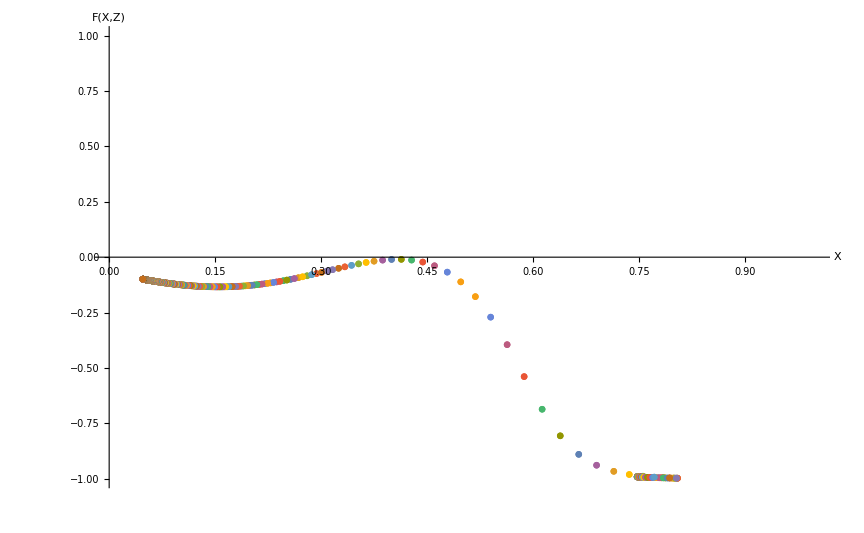

```mathematica
(*Plot X vs the remaining equation when Y' = 0*)
(*When F(X,Z) = 0, an Einstein point exists*)
EinsteinPlotLimitingCompactSpiral=ListPlot[EinsteinPointSolutionsLimitingCompactSpiral,PlotRange->{{0,1},{-1,1}},AxesLabel->{"X","F(X,Z)"}]
```

#### Plot the X-Y-Z Phase Space

```mathematica
(*Find the maximum value of K for this combination of X0 and Z0 such that Y0 is not imaginary*)
KMaxLimitingCompactSpiral=K/.Solve[Y0LimitingSpiral==0,K][[1]]
```

0.0356667

```mathematica
(*Solve trajLimitingCompact[K] for different values of K*)
```

```mathematica
solLimitingCompactSpiral[1]=trajLimitingCompactSpiral[KDensityParametersOpen]
```

NDSolve::mxst: Maximum number of 134831 steps reached at the point t == -8.88046.

{{X1→InterpolatingFunction[{{-8.88046, 100.}}, <>],Y1→InterpolatingFunction[{{-8.88046, 100.}}, <>],Z1→InterpolatingFunction[{{-8.88046, 100.}}, <>]}}

```mathematica
solLimitingCompactSpiral[2]=trajLimitingCompactSpiral[KDensityParametersClosed]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solLimitingCompactSpiral[3]=trajLimitingCompactSpiral[-.1]
```

Power::infy: Infinite expression 1/(√(0.+0. ⅈ)) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,0.+0. ⅈ,Indeterminate} is not a list of numbers with dimensions {3} at {t,X1[t],Y1[t],Z1[t]} = {-2.88294,0.75+0. ⅈ,1.+0. ⅈ,0.42446+0. ⅈ}.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solLimitingCompactSpiral[4]=trajLimitingCompactSpiral[KMaxLimitingCompactSpiral]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solLimitingCompactSpiral[5]=trajLimitingCompactSpiral[0.005]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solLimitingCompactSpiral[6]=trajLimitingCompactSpiral[0.017]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solLimitingCompactSpiral[7]=trajLimitingCompactSpiral[0.013]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the trajectories for the different values of K given above.*)
(*Plot the solutions using a value of K found from the range of Ωk0 allowed by Planck 2018 in purple*)
```

```mathematica
trajLimitingCompactXYZSpiral[1]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactSpiral[1],{t,-8.58,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZSpiral[2]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactSpiral[2],{t,-100,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZSpiral[3]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactSpiral[3],{t,-2.87,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZSpiral[4]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactSpiral[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZSpiral[5]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactSpiral[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZSpiral[6]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactSpiral[6],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZSpiral[7]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactSpiral[7],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajLimitingCaseCompactSpiral=Table[trajLimitingCompactXYZSpiral[i],{i,1,7}];
```

```mathematica
(*Plot the Einstein fixed point*)
EinsteinFixedPointsLimitingCompactSpiral=ListPointPlot3D[{EinsteinPointLimitingCompactSpiral},PlotStyle->Black];
```

```mathematica
(*Solve theX-Y-Z system around the Einstein fixed point to plot the Closed Friedmann Separatrix (CFS)*)
CFSLimitingSolCompactSpiral=NDSolve[{deXt,deYt,deZt,X1[0]==EinsteinPointLimitingCompactSpiral[[1]],Y1[0]==0,Z1[0]==EinsteinPointLimitingCompactSpiral[[3]]},{X1,Y1,Z1},{t,-100,100}]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the CFS*)
CFSLimitingCompactSpiral=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.CFSLimitingSolCompactSpiral,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
(*Show the X-Y-Z phase space*)
Show[trajLimitingCaseCompactSpiral,EinsteinFixedPointsLimitingCompactSpiral,CFSLimitingCompactSpiral,AccnXYZSpiral,FPsXYZSpiral,CompactFPShowXYZSpiral,XYZCompactFormat]
```

-Graphics3D-

#### Plot the X-Z Projection

```mathematica
(*Plot one solution on the X-Z plane*)
trajLimitingCompactXZSpiral=ParametricPlot[Evaluate[{{Z1[t],X1[t]}}/.solLimitingCompactSpiral[1],{t,-8.58,100},PlotStyle -> {{Black, Thick,Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0,.03,0,.03,0},1]]],Arrow[x]};
```

```mathematica
(*Plot the Einstein fixed point on the X-Z plane*)
EinsteinFixedPointsLimitingCompactXZSpiral=ListPlot[{{EinsteinPointLimitingCompactSpiral[[3]],EinsteinPointLimitingCompactSpiral[[1]]}},PlotStyle->Black];
```

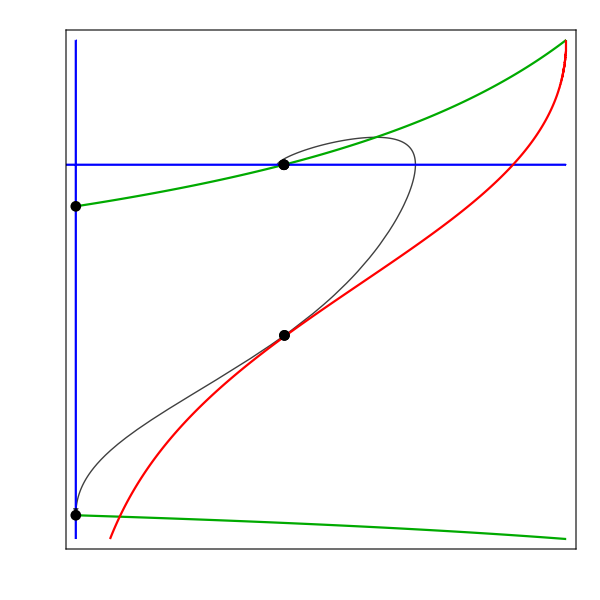

```mathematica
(*Show the X-Z phase space with the a'' = 0 (red), X' = 0 (green) and Z' = 0 (purple) curves*)
Show[trajLimitingCompactXZSpiral,XLineSpiral,ZLineSpiral,AccnXZSpiral,EinsteinFixedPointsLimitingCompactXZSpiral,FPsXZSpiral,CompactFPShowXZSpiral,XZCompactFormat]
```

### Two Einstein Fixed Points

#### Find the Einstein Fixed Points

```mathematica
(*Fix z0 using the density parameters*)
z0TwoEinsteinPointsSpiral=Ωm0*ℛ/(Ωx0*α);
```

```mathematica
(*Compactify z0*)
Z0TwoEinsteinPointsSpiral=z0TwoEinsteinPointsSpiral/(1+z0TwoEinsteinPointsSpiral)
```

0.0432077

```mathematica
(*Substitute Z0TwoEinsteinPoints into Y0 for this case*)
Y0TwoEinsteinPointsSpiral=Y0/.Z0->Z0TwoEinsteinPointsSpiral
```

(√(0.0483863-K))/(√(1.04839-K))

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajTwoEinsteinPointsCompactSpiral[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0TwoEinsteinPointsSpiral,Z1[0]==Z0TwoEinsteinPointsSpiral},{X1,Y1,Z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition (√(0.0483863-1. K))/(√(1.04839-1. K)) is not a number or a rectangular array of numbers.

NDSolve[{X1'[t]==-(3 (0.5 (1-X1[t])-0.25 X1[t]) (-0.05 (1-X1[t])+X1[t]) Y1[t])/(√(1-Y1[t]^2))-((1-X1[t]) X1[t] Y1[t] Z1[t])/(√(1-Y1[t]^2) (1-Z1[t])),Y1'[t]==-Y1[t]^2 √(1-Y1[t]^2)-1/6 (1-Y1[t]^2)^(3/2) (-0.075-(0.4625 X1[t])/(1-X1[t])-(0.75 X1[t]^2)/(1-X1[t])^2+Z1[t]/(1-Z1[t])),Z1'[t]==-(3 Y1[t] (1-Z1[t]) Z1[t])/(√(1-Y1[t]^2))+(X1[t] Y1[t] (1-Z1[t]) Z1[t])/((1-X1[t]) √(1-Y1[t]^2)),X1[0]==0.0909091,Y1[0]==(√(0.0483863-K))/(√(1.04839-K)),Z1[0]==0.0432077},{X1,Y1,Z1},{t,-100,100}]

```mathematica
(*Set-up tables of X1 and Z1 values to be used to find the X and Z value of the first Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
XTableSol1TwoEinsteinPointsCompactSpiral=Table[X1[i]/.trajTwoEinsteinPointsCompactSpiral[0],{i,-2,100,.01}];
ZTableSol1TwoEinsteinPointsCompactSpiral=Table[Z1[i]/.trajTwoEinsteinPointsCompactSpiral[0],{i,-2,100,.01}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol1TwoEinsteinPointsCompactSpiral=(ZTableSol1TwoEinsteinPointsCompactSpiral/(1-ZTableSol1TwoEinsteinPointsCompactSpiral))+(XTableSol1TwoEinsteinPointsCompactSpiral/(1-XTableSol1TwoEinsteinPointsCompactSpiral))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSol1TwoEinsteinPointsCompactSpiral/(1-XTableSol1TwoEinsteinPointsCompactSpiral))^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol1TwoEinsteinPointsCompact that is closest to zero. When EinsteinPlotValuesSol1TwoEinsteinPointsCompact = 0 (Y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints1CompactSpiral=Flatten[Nearest[EinsteinPlotValuesSol1TwoEinsteinPointsCompactSpiral,0]]
```

{0.00021485}

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints1Compact in the EinsteinPlotValuesSol1TwoEinsteinPointsCompact*)
PositionNearestToZeroTwoEinsteinPoints1CompactSpiral=Flatten[Position[EinsteinPlotValuesSol1TwoEinsteinPointsCompactSpiral,NearestToZeroTwoEinsteinPoints1CompactSpiral]]
```

{32}

```mathematica
(*Find the Einstein point by finding the X and Z values in XTableSol1TwoEinsteinPointsCompact and ZTableSol1TwoEinsteinPointsCompact at PositionNearestToZeroTwoEinsteinPoints1Compact*)
EinsteinPoint1TwoEinsteinPointsCompactSpiral=Flatten[{XTableSol1TwoEinsteinPointsCompactSpiral[[PositionNearestToZeroTwoEinsteinPoints1CompactSpiral]],0,ZTableSol1TwoEinsteinPointsCompactSpiral[[PositionNearestToZeroTwoEinsteinPoints1CompactSpiral]]}]
```

{0.130255,0,0.138897}

```mathematica
(*Set-up tables of X1 and Z1 values to be used to find the X and Z value of the second Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
XTableSol2TwoEinsteinPointsCompactSpiral=Table[X1[i]/.trajTwoEinsteinPointsCompactSpiral[0],{i,-5.6,-3.2,.001}];
ZTableSol2TwoEinsteinPointsCompactSpiral=Table[Z1[i]/.trajTwoEinsteinPointsCompactSpiral[0],{i,-5.6,-3.2,.001}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol2TwoEinsteinPointsCompactSpiral=(ZTableSol2TwoEinsteinPointsCompactSpiral/(1-ZTableSol2TwoEinsteinPointsCompactSpiral))+(XTableSol2TwoEinsteinPointsCompactSpiral/(1-XTableSol2TwoEinsteinPointsCompactSpiral))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSol2TwoEinsteinPointsCompactSpiral/(1-XTableSol2TwoEinsteinPointsCompactSpiral))^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol2TwoEinsteinPointsCompact that is closest to zero. When EinsteinPlotValuesSol2TwoEinsteinPointsCompact = 0 (Y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints2CompactSpiral=Flatten[Nearest[EinsteinPlotValuesSol2TwoEinsteinPointsCompactSpiral,0]]
```

{0.00312607}

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints2Compact in the EinsteinPlotValuesSol2TwoEinsteinPointsCompact array*)
PositionNearestToZeroTwoEinsteinPoints2CompactSpiral=Flatten[Position[EinsteinPlotValuesSol2TwoEinsteinPointsCompactSpiral,NearestToZeroTwoEinsteinPoints2CompactSpiral]]
```

{1876}

```mathematica
(*Find the Einstein point by finding the X and Z values in XTableSol2TwoEinsteinPointsCompact and ZTableSol2TwoEinsteinPointsCompact at PositionNearestToZeroTwoEinsteinPoints2Compact*)
EinsteinPoint2TwoEinsteinPointsCompactSpiral=Flatten[{XTableSol2TwoEinsteinPointsCompactSpiral[[PositionNearestToZeroTwoEinsteinPoints2CompactSpiral]],0,ZTableSol2TwoEinsteinPointsCompactSpiral[[PositionNearestToZeroTwoEinsteinPoints2CompactSpiral]]}]
```

{0.633296,0,0.756912}

```mathematica
(*Put the Einstein fixed points into a common variable name*)
EinsteinPointTwoEPtsCompactSpiral[1]=EinsteinPoint1TwoEinsteinPointsCompactSpiral;
EinsteinPointTwoEPtsCompactSpiral[2]=EinsteinPoint2TwoEinsteinPointsCompactSpiral;
```

```mathematica
(*Put the Einstein fixed points into a table*)
EinsteinPointsTwoEPtsCompactSpiral=Table[EinsteinPointTwoEPtsCompactSpiral[i],{i,1,2}];
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each Einstein fixed point*)
EinsteinPointTableTwoEinsteinPointsCompactSpiral=Table[{EinsteinPointsTwoEPtsCompactSpiral[[i]]//MatrixForm,Simplify[JCompactXYZSpiral/.{X->EinsteinPointsTwoEPtsCompactSpiral[[i,1]],Y->EinsteinPointsTwoEPtsCompactSpiral[[i,2]],Z->EinsteinPointsTwoEPtsCompactSpiral[[i,3]]}]//MatrixForm,Eigenvalues[JCompactXYZSpiral/.{X->EinsteinPointsTwoEPtsCompactSpiral[[i,1]],Y->EinsteinPointsTwoEPtsCompactSpiral[[i,2]],Z->EinsteinPointsTwoEPtsCompactSpiral[[i,3]]}]//MatrixForm,Eigenvectors[JCompactXYZSpiral/.{X->EinsteinPointsTwoEPtsCompactSpiral[[i,1]],Y->EinsteinPointsTwoEPtsCompactSpiral[[i,2]],Z->EinsteinPointsTwoEPtsCompactSpiral[[i,3]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the Einstein fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableTwoEinsteinPointsCompactSpiral=TableForm[EinsteinPointTableTwoEinsteinPointsCompactSpiral,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.130255
0
0.138897) | (0. | -0.122997 | 0.
0.151396 | 0. | -0.22477
0. | -0.340903 | 0.) | (-0.240839
0.240839
6.38968×10^-18) | (-0.28266 | -0.553477 | -0.783433
0.28266 | -0.553477 | 0.783433
0.829403 | -5.09251×10^-17 | 0.55865)
(0.633296
0
0.756912) | (0. | -0.769284 | 0.
3.78391 | 0. | -2.82047
0. | -0.234229 | 0.) | (-1.00153×10^-17+1.50009 ⅈ
-1.00153×10^-17-1.50009 ⅈ
5.82828×10^-17+0. ⅈ) | (-3.46579×10^-16-0.451978 ⅈ | -0.88135+0. ⅈ | -1.25865×10^-16-0.137617 ⅈ
-3.46579×10^-16+0.451978 ⅈ | -0.88135+0. ⅈ | -1.25865×10^-16+0.137617 ⅈ
0.597629+0. ⅈ | 1.24466×10^-15+0. ⅈ | 0.801773+0. ⅈ)

```mathematica
(*Set-up tables of all X1 and Z1 values*)
XTableSolTwoEinsteinPointsFullCompactSpiral=Table[X1[i]/.trajTwoEinsteinPointsCompactSpiral[0],{i,-100,100,.1}];
ZTableSolTwoEinsteinPointsFullCompactSpiral=Table[Z1[i]/.trajTwoEinsteinPointsCompactSpiral[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0*)
EinsteinPlotValuesSolTwoEinsteinPointsFullXZSpiral=(ZTableSolTwoEinsteinPointsFullCompactSpiral/(1-ZTableSolTwoEinsteinPointsFullCompactSpiral))+(XTableSolTwoEinsteinPointsFullCompactSpiral/(1-XTableSolTwoEinsteinPointsFullCompactSpiral))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSolTwoEinsteinPointsFullCompactSpiral/(1-XTableSolTwoEinsteinPointsFullCompactSpiral))^2;
```

```mathematica
(*Compactify EinsteinPlotValuesSolTwoEinsteinPointsFullXZ*)
EinsteinPlotValuesSolTwoEinsteinPointsFullCompactSpiral=EinsteinPlotValuesSolTwoEinsteinPointsFullXZSpiral/Sqrt[1+EinsteinPlotValuesSolTwoEinsteinPointsFullXZSpiral^2];
```

```mathematica
(*Merge the XTableSolTwoEinsteinPointsFullCompact values and the EinsteinPlotValuesSolTwoEinsteinPointsFullCompact values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsTwoEinsteinPointsCompactSpiral=MapThread[h,{XTableSolTwoEinsteinPointsFullCompactSpiral,EinsteinPlotValuesSolTwoEinsteinPointsFullCompactSpiral}];
```

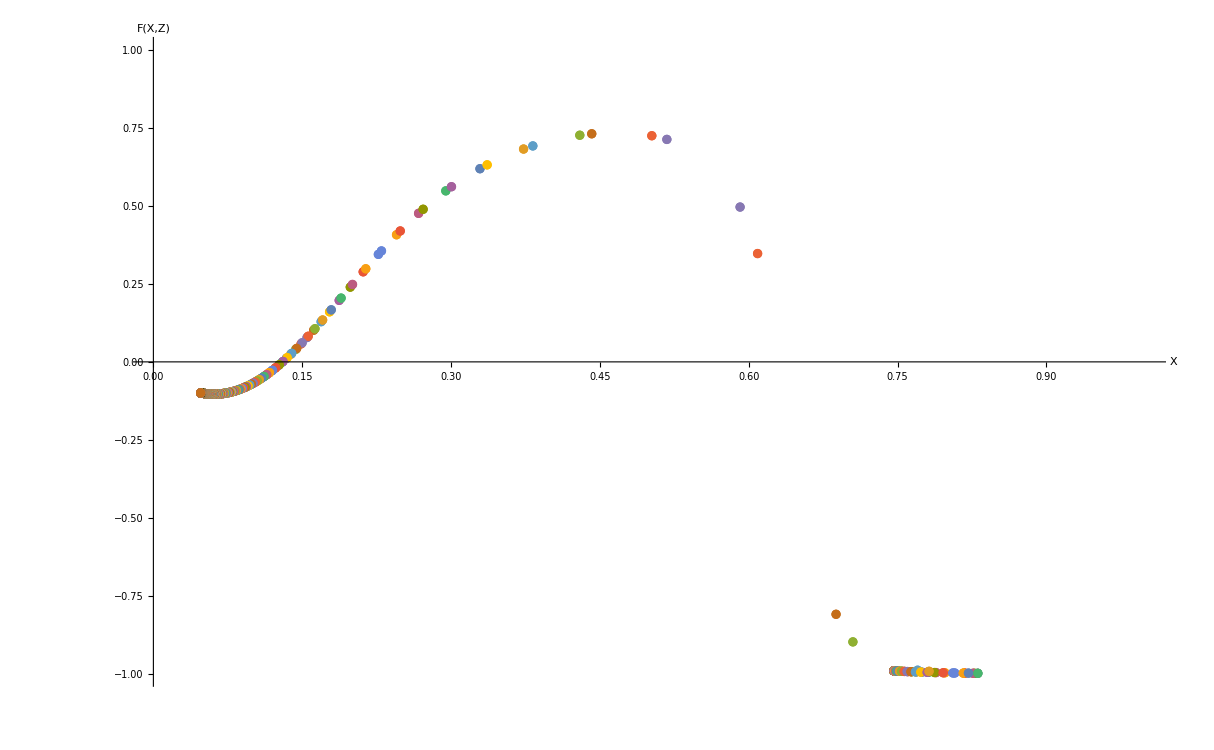

```mathematica
(*Plot X vs the remaining equation when Y' = 0*)
(*When F(X,Z) = 0, an Einstein point exists*)
EinsteinPlotTwoEinsteinPointsCompactSpiral=ListPlot[EinsteinPointSolutionsTwoEinsteinPointsCompactSpiral,PlotRange->{{0,1},{-1,1}},AxesLabel->{"X","F(X,Z)"}]
```

#### Plot the X-Y-Z Phase Space

```mathematica
(*Find the maximum value of K for this combination of X0 and Z0 so that Y0 is not imaginary*)
KMaxTwoEinsteinPointsCompactSpiral=K/.Flatten[Solve[Y0TwoEinsteinPointsSpiral==0,K]]
```

0.0483863

```mathematica
(*Solve trajTwoEinsteinPointsCompact[K] for different values of K*)
```

```mathematica
solTwoEinsteinPointsCompactSpiral[1]=trajTwoEinsteinPointsCompactSpiral[KDensityParametersOpen]
```

NDSolve::mxst: Maximum number of 238904 steps reached at the point t == -7.0047.

{{X1→InterpolatingFunction[{{-7.0047, 100.}}, <>],Y1→InterpolatingFunction[{{-7.0047, 100.}}, <>],Z1→InterpolatingFunction[{{-7.0047, 100.}}, <>]}}

```mathematica
solTwoEinsteinPointsCompactSpiral[2]=trajTwoEinsteinPointsCompactSpiral[KDensityParametersClosed]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsCompactSpiral[3]=trajTwoEinsteinPointsCompactSpiral[-.1]
```

NDSolve::ndcf: Repeated convergence test failure at t == -2.6552; unable to continue.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsCompactSpiral[4]=trajTwoEinsteinPointsCompactSpiral[KMaxTwoEinsteinPointsCompactSpiral]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsCompactSpiral[5]=trajTwoEinsteinPointsCompactSpiral[0.02]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the trajectories for the different values of K given above*)
(*Plot the solutions using a value of K found from the range of Ωk0 allowed by Planck 2018 in purple*)
```

```mathematica
trajTwoEinsteinPointsCompactXYZSpiral[1]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactSpiral[1],{t,-6.9,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsCompactXYZSpiral[2]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactSpiral[2],{t,-100,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsCompactXYZSpiral[3]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactSpiral[3],{t,-2.65,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsCompactXYZSpiral[4]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactSpiral[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
trajTwoEinsteinPointsCompactXYZSpiral[5]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactSpiral[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Solve the X-Y-Z system using the centre Einstein fixed point for X0 and Z0 to plot a cyclic trajectory*)
CyclicTrajTwoEinsteinPointsCompactSpiral=NDSolve[{deXt,deYt,deZt,X1[0]==EinsteinPoint2TwoEinsteinPointsCompactSpiral[[1]],Y1[0]==0.4,Z1[0]==EinsteinPoint2TwoEinsteinPointsCompactSpiral[[3]]},{X1,Y1,Z1},{t,-100,100}];
```

```mathematica
(*Plot the cyclic trajectory*)
trajTwoEinsteinPointsCompactXYZSpiral[6]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.CyclicTrajTwoEinsteinPointsCompactSpiral,{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajTwoEinsteinPointsCaseCompactSpiral=Table[trajTwoEinsteinPointsCompactXYZSpiral[i],{i,1,6}];
```

```mathematica
(*Plot the Einstein fixed points*)
EinsteinFixedPointsTwoEinsteinPointsCompactSpiral=ListPointPlot3D[{EinsteinPoint1TwoEinsteinPointsCompactSpiral,EinsteinPoint2TwoEinsteinPointsCompactSpiral},PlotStyle->Black];
```

```mathematica
(*Solve the X-Y-Z system around the Einstein fixed point to plot the Closed Friedmann Separatrix (CFS)*)
CFSTwoEinsteinPointsSolCompactSpiral=NDSolve[{deXt,deYt,deZt,X1[0]==EinsteinPoint1TwoEinsteinPointsCompactSpiral[[1]],Y1[0]==-0.0005,Z1[0]==EinsteinPoint1TwoEinsteinPointsCompactSpiral[[3]]},{X1,Y1,Z1},{t,-100,100}]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the CFS*)
CFSTwoEinsteinPointsCompactSpiral=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.CFSTwoEinsteinPointsSolCompactSpiral,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Show the X-Y-Z phase space*)
Show[trajTwoEinsteinPointsCaseCompactSpiral,CFSTwoEinsteinPointsCompactSpiral,EinsteinFixedPointsTwoEinsteinPointsCompactSpiral,AccnXYZSpiral,FPsXYZSpiral,CompactFPShowXYZSpiral,XYZCompactFormat]
```

-Graphics3D-

#### Plot the X-Z Projection

```mathematica
(*Plot one solution on the X-Z plane*)
trajTwoEinsteinPointsCompactXZSpiral=ParametricPlot[Evaluate[{{Z1[t],X1[t]}}/.solTwoEinsteinPointsCompactSpiral[1],{t,-6.67,100},PlotStyle -> {{Black,Thick, Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.03,.03,0},1]]],Arrow[x]};
```

```mathematica
(*Plot the Einstein fixed points on the X-Z plane*)
EinsteinFixedPointsTwoEinsteinPointsCompactXZSpiral=ListPlot[{{EinsteinPoint1TwoEinsteinPointsCompactSpiral[[3]],EinsteinPoint1TwoEinsteinPointsCompactSpiral[[1]]},{EinsteinPoint2TwoEinsteinPointsCompactSpiral[[3]],EinsteinPoint2TwoEinsteinPointsCompactSpiral[[1]]}},PlotStyle->Black];
```

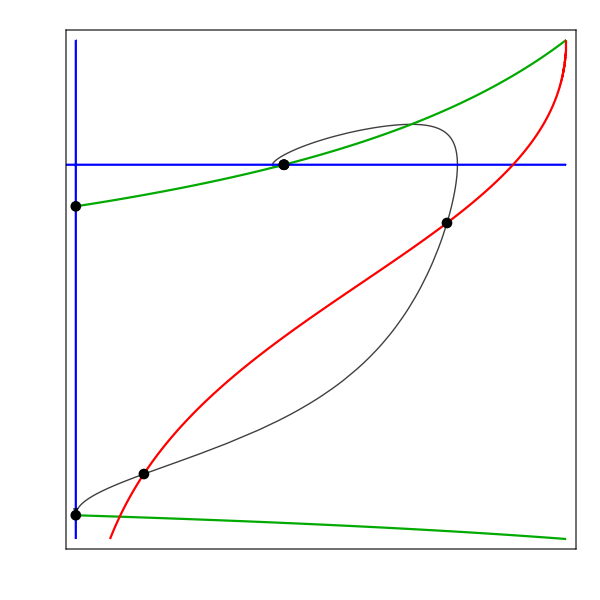

```mathematica
(*Show the X-Z phase space with the a'' = 0 (red), X' = 0 (green) and Z' = 0 (purple) curves*)
Show[trajTwoEinsteinPointsCompactXZSpiral,XLineSpiral,ZLineSpiral,AccnXZSpiral,EinsteinFixedPointsTwoEinsteinPointsCompactXZSpiral,FPsXZSpiral,CompactFPShowXZSpiral,XZCompactFormat]
```

### No Einstein Fixed Points

#### Plot to show there are no Einstein fixed points

```mathematica
(*Fix z0 such that there are no Einstein fixed points on the surface*)
z0NoEinsteinPointsSpiral=0.005;
```

```mathematica
(*Compactify z0*)
Z0NoEinsteinPointsSpiral=z0NoEinsteinPointsSpiral/(1+z0NoEinsteinPointsSpiral)
```

0.00497512

```mathematica
(*Substitute Z0NoEinsteinPoints into Y0 for this case*)
Y0NoEinsteinPointsSpiral=Y0/.Z0->Z0NoEinsteinPointsSpiral
```

(√(0.035-K))/(√(1.035-K))

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajNoEinsteinPointsCompactSpiral[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0NoEinsteinPointsSpiral,Z1[0]==Z0NoEinsteinPointsSpiral},{X1,Y1,Z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition (√(0.035-1. K))/(√(1.035-1. K)) is not a number or a rectangular array of numbers.

NDSolve[{X1'[t]==-(3 (0.5 (1-X1[t])-0.25 X1[t]) (-0.05 (1-X1[t])+X1[t]) Y1[t])/(√(1-Y1[t]^2))-((1-X1[t]) X1[t] Y1[t] Z1[t])/(√(1-Y1[t]^2) (1-Z1[t])),Y1'[t]==-Y1[t]^2 √(1-Y1[t]^2)-1/6 (1-Y1[t]^2)^(3/2) (-0.075-(0.4625 X1[t])/(1-X1[t])-(0.75 X1[t]^2)/(1-X1[t])^2+Z1[t]/(1-Z1[t])),Z1'[t]==-(3 Y1[t] (1-Z1[t]) Z1[t])/(√(1-Y1[t]^2))+(X1[t] Y1[t] (1-Z1[t]) Z1[t])/((1-X1[t]) √(1-Y1[t]^2)),X1[0]==0.0909091,Y1[0]==(√(0.035-K))/(√(1.035-K)),Z1[0]==0.00497512},{X1,Y1,Z1},{t,-100,100}]

```mathematica
(*Set-up tables of all X1 and Z1 values*)
XTableSolNoEinsteinPointsFullCompactSpiral=Table[X1[i]/.trajNoEinsteinPointsCompactSpiral[0],{i,-100,100,.1}];
ZTableSolNoEinsteinPointsFullCompactSpiral=Table[Z1[i]/.trajNoEinsteinPointsCompactSpiral[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0*)
EinsteinPlotValuesSolNoEinsteinPointsFullCompactSpiral=(ZTableSolNoEinsteinPointsFullCompactSpiral/(1-ZTableSolNoEinsteinPointsFullCompactSpiral))+(XTableSolNoEinsteinPointsFullCompactSpiral/(1-XTableSolNoEinsteinPointsFullCompactSpiral))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSolNoEinsteinPointsFullCompactSpiral/(1-XTableSolNoEinsteinPointsFullCompactSpiral))^2;
```

```mathematica
(*Compactify EinsteinPlotValuesSolNoEinsteinPointsFullCompact*)
EinsteinPlotValuesSolNoEinsteinPointsFullXZSpiral=EinsteinPlotValuesSolNoEinsteinPointsFullCompactSpiral/Sqrt[1+EinsteinPlotValuesSolNoEinsteinPointsFullCompactSpiral^2];
```

```mathematica
(*Merge the XTableSolNoEinsteinPointsFullCompact values and the EinsteinPlotValuesSolNoEinsteinPointsFullXZ values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsNoEinsteinPointsCompactSpiral=MapThread[h,{XTableSolNoEinsteinPointsFullCompactSpiral,EinsteinPlotValuesSolNoEinsteinPointsFullXZSpiral}];
```

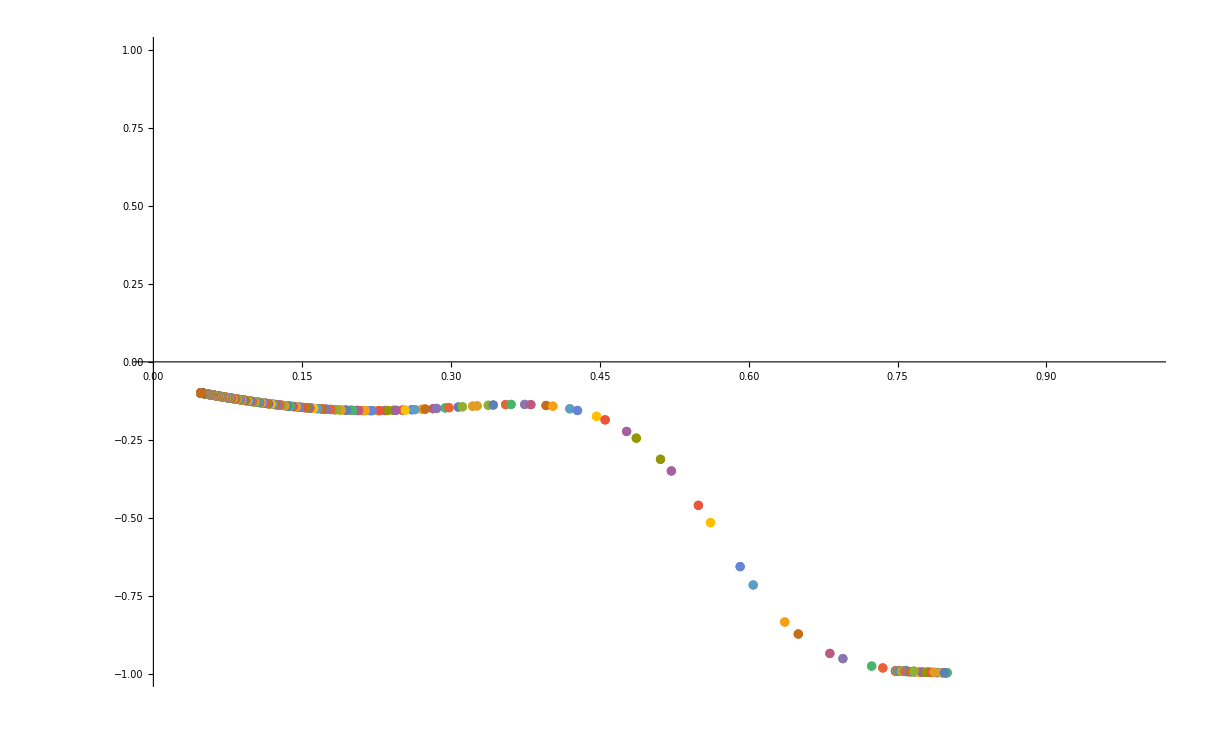

```mathematica
(*Plot X vs the remaining equation when Y' = 0*)
(*Here, F(X,Z) is never zero, so there are no Einstein fixed points*)
EinsteinPlotNoEinsteinPointsCompactSpiral=ListPlot[EinsteinPointSolutionsNoEinsteinPointsCompactSpiral,PlotRange->{{0,1},{-1,1}}]
```

#### Plot the X-Y-Z Phase Space

```mathematica
(*Find the maximum value of K for this combination of X0 and Z0 such that Y0 is not imaginary*)
KMaxNoEinsteinPointsCompactSpiral=K/.Solve[Y0NoEinsteinPointsSpiral==0,K][[1]]
```

0.035

```mathematica
(*Solve trajNoEinsteinPointsCompact[K] for different values of K*)
```

```mathematica
solNoEinsteinPointsCompactSpiral[1]=trajNoEinsteinPointsCompactSpiral[KDensityParametersOpen]
```

NDSolve::mxst: Maximum number of 131491 steps reached at the point t == -8.89343.

{{X1→InterpolatingFunction[{{-8.89343, 100.}}, <>],Y1→InterpolatingFunction[{{-8.89343, 100.}}, <>],Z1→InterpolatingFunction[{{-8.89343, 100.}}, <>]}}

```mathematica
solNoEinsteinPointsCompactSpiral[2]=trajNoEinsteinPointsCompactSpiral[KDensityParametersClosed]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsCompactSpiral[3]=trajNoEinsteinPointsCompactSpiral[-.1]
```

NDSolve::ndsz: At t == -2.89969, step size is effectively zero; singularity or stiff system suspected.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsCompactSpiral[4]=trajNoEinsteinPointsCompactSpiral[0.005]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsCompactSpiral[5]=trajNoEinsteinPointsCompactSpiral[KMaxNoEinsteinPointsCompactSpiral]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsCompactSpiral[6]=trajNoEinsteinPointsCompactSpiral[0.013]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsCompactSpiral[7]=trajNoEinsteinPointsCompactSpiral[0.01]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the trajectories for the different values of K given above.*)
(*Plot the solutions using a value of K found from the range of Ωk0 allowed by Planck 2018 in purple*)
```

```mathematica
trajNoEinsteinPointsCompactXYZSpiral[1]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactSpiral[1],{t,-8.89,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZSpiral[2]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactSpiral[2],{t,-100,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZSpiral[3]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactSpiral[3],{t,-2.89,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZSpiral[4]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactSpiral[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZSpiral[5]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactSpiral[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZSpiral[6]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactSpiral[6],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZSpiral[7]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactSpiral[7],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajNoEinsteinPointsPlotsCompactSpiral=Table[trajNoEinsteinPointsCompactXYZSpiral[i],{i,1,7}];
```

```mathematica
(*Show the X-Y-Z phase space*)
Show[trajNoEinsteinPointsPlotsCompactSpiral,AccnXYZSpiral,FPsXYZSpiral,CompactFPShowXYZSpiral,XYZCompactFormat]
```

-Graphics3D-

#### Plot the X-Z Projection

```mathematica
(*Plot one solution on the X-Z plane*)
trajNoEinsteinPointsCompactXZSpiral=ParametricPlot[Evaluate[{{Z1[t],X1[t]}}/.solNoEinsteinPointsCompactSpiral[1],{t,-8.89,100},PlotStyle -> {{Black,Thick, Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0,.03,0,.03,0},1]]],Arrow[x]};
```

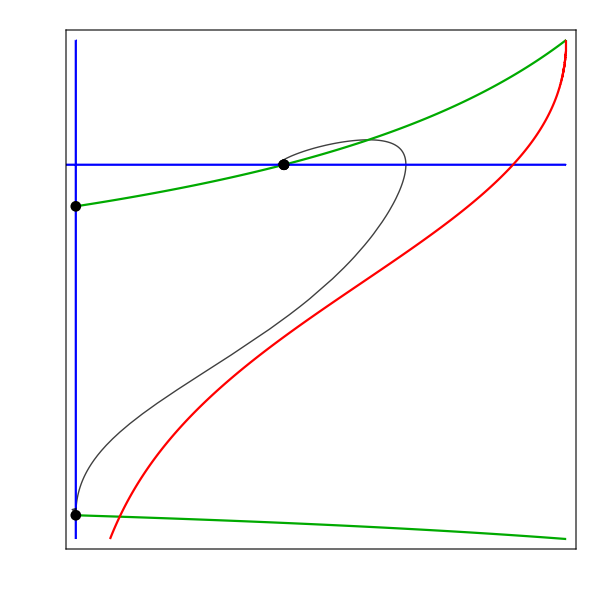

```mathematica
(*Show the X-Z phase space with the a'' = 0 (red), X' = 0 (green) and Z' = 0 (purple) curves*)
Show[trajNoEinsteinPointsCompactXZSpiral,XLineSpiral,ZLineSpiral,AccnXZSpiral,FPsXZSpiral,CompactFPShowXZSpiral,XZCompactFormat]
```

## Investigate system when ℛ = 10^(-120)

### Set-up

```mathematica
(*Clear variables*)
Clear[q,ϵ,ℛ,wx]
```

```mathematica
(*Set parameter values*)
q=1;
ϵ=-0.25;
ℛ=10^(-120);
wx=-0.5;
```

```mathematica
(*Define Ωx0 and Ωm0 using data from Planck 2018*)
Ωx0=0.6889;
Ωm0=0.3111;
```

```mathematica
(*Set a value for α, which sets the value of the low energy cosmological constant*)
α=0.5;
```

```mathematica
(*Define the initial conditions, where a0 = 1 and K is defined as k/ρ* *)

x0=ℛ/α;
y0=Sqrt[x0/3+Z0/(3*(1-Z0))-K];
```

```mathematica
(*Compactify the initial conditions*)

X0=x0/(1+x0);
Y0=y0/Sqrt[1+y0^2];
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y in terms of time, t*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*(X1[t]-ℛ*(1-X1[t]))*((1+wx)*(1-X1[t])+ϵ*X1[t])-q*X1[t]*(1-X1[t])*(Z1[t]/(1-Z1[t]))*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((Z1[t]/(1-Z1[t]))+(X1[t]/(1-X1[t]))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X1[t]^2/((1-X1[t])^2))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2))) + q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
```

### Find the value of z0 to give the limiting case

```mathematica
(*Fix z0 using the density parameters*)
z0RealisticℛSpiral=Ωm0*ℛ/(Ωx0*α)
```

9.03179×10^-121

```mathematica
(*Compactify z0*)
Z0RealisticℛSpiral=z0RealisticℛSpiral/(1+z0RealisticℛSpiral)
```

9.03179×10^-121

```mathematica
(*Substitute Z0Realisticℛ into Y0 for this case*)
Y0RealisticℛSpiral=Y0/.Z0->Z0RealisticℛSpiral
```

(√(9.67726×10^-121-K))/(√(1.-K))

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajRealisticℛSpiral[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0RealisticℛSpiral,Z1[0]==Z0RealisticℛSpiral},{X1,Y1,Z1},{t,-100,100}];
```

NDSolve::ndinnt: Initial condition (√(9.67726×10^-121-1. K))/(√(1.-1. K)) is not a number or a rectangular array of numbers.

```mathematica
(*Set-up tables of all X1 and Z1 values*)
XTableRealisticℛSpiral=Table[X1[i]/.trajRealisticℛSpiral[0],{i,-100,100,.1}];
ZTableRealisticℛSpiral=Table[Z1[i]/.trajRealisticℛSpiral[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0*)
EinsteinPlotValuesRealisticℛSpiral=(ZTableRealisticℛSpiral/(1-ZTableRealisticℛSpiral))+(XTableRealisticℛSpiral/(1-XTableRealisticℛSpiral))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableRealisticℛSpiral/(1-XTableRealisticℛSpiral))^2;
```

```mathematica
(*Compactify EinsteinPlotValuesRealisticℛ*)
EinsteinPlotRealisticℛCompactSpiral=EinsteinPlotValuesRealisticℛSpiral/Sqrt[1+EinsteinPlotValuesRealisticℛSpiral^2];
```

```mathematica
(*Find the maximum value of EinsteinPlotRealisticℛCompact*)
(*As EinsteinPlotRealisticℛCompact is always less than zero there are no Einstein points when z0 is defined using the density parameters*)
Max[EinsteinPlotRealisticℛCompactSpiral]
```

-1.59682×10^-120

## Fix Parameters : wx > -1, ϵ = +1, 0 < q < 0.75

## Plot the full x-z and x-y-z phase spaces

### Non-Compact x - z Phase Space

```mathematica
(*Clear variables*)
Clear[q,ϵ,ℛ,wx]
```

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*Define a format style for the x-z phase spaces*)
xzFormat={Frame->{True},FrameLabel->{MaTeX["z",FontSize->24],Rotate[MaTeX["x",FontSize->24],300]},FrameTicks->{{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->24]},{x,1Range[-1,5]}],None},{Table[{z,MaTeX[z,"DisplayStyle"->False,FontSize->24]},{z,1Range[0,5]}],None}},ImageSize->{600,600},PlotRangePadding->{0.02,0}};
```

```mathematica
(*Set parameter values such that wx > -0.25 and only the repellor and attractor fixed points satisfy z >= 0*)
wx=-0.2;
q=1;
ϵ=-0.25;
ℛ=0.05;
```

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, and dark matter, z*)
dex:=x'=-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z
dez:=z'=-3*z + q*x*z
```

```mathematica
(*Find the fixed points of the system*)
FPsxzRepellor=Solve[{dez==0,dex==0},{z,x}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{z→0.,x→0.05},{z→-0.1475,x→3.},{z→0.,x→3.2}}

```mathematica
(*Extract the values of the fixed points and put them into one variable name*)
FPxzRepellor[1]={z/.FPsxzRepellor[[1,1]],x/.FPsxzRepellor[[1,2]]};
FPxzRepellor[2]={z/.FPsxzRepellor[[2,1]],x/.FPsxzRepellor[[2,2]]};
FPxzRepellor[3]={z/.FPsxzRepellor[[3,1]],x/.FPsxzRepellor[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPxzTableRepellor=Table[FPxzRepellor[i],{i,1,3}];
```

```mathematica
(*Find the 2D Jacobian matrix. D[] differentiates each expression*)
JxzRepellor=Simplify[{{D[dez,z],D[dez,x]}, {D[dex,z],D[dex,x]}}];
JxzRepellor//MatrixForm
```

(-3+x | z
-x | -2.4375+1.5 x-1. z)

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableRepellor=Table[{FPxzTableRepellor[[i]]//MatrixForm,Simplify[JxzRepellor/.{z->FPxzTableRepellor[[i,1]],x->FPxzTableRepellor[[i,2]]}]//MatrixForm,Eigenvalues[JxzRepellor/.{z->FPxzTableRepellor[[i,1]],x->FPxzTableRepellor[[i,2]]}]//MatrixForm,Eigenvectors[JxzRepellor/.{z->FPxzTableRepellor[[i,1]],x->FPxzTableRepellor[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTablexzRepellor=TableForm[FPTableRepellor,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.
0.05) | (-2.95 | 0.
-0.05 | -2.3625) | (-2.95
-2.3625) | (0.996398 | 0.0847998
0. | 1.)
(-0.1475
3.) | (0. | -0.1475
-3. | 2.21) | (2.39478
-0.184777) | (0.0614759 | -0.998109
-0.623865 | -0.781532)
(0.
3.2) | (0.2 | 0.
-3.2 | 2.3625) | (2.3625
0.2) | (0. | 1.
0.559917 | 0.828548)

```mathematica
(*Plot the fixed points*)
FPsxzRepellor=ListPlot[FPxzTableRepellor,PlotStyle->Black];
```

```mathematica
(*Plot the phase space for the dark energy and dark matter*)
PhaseSpacexzRepellor=StreamPlot[{dez,dex},{z,0,3},{x,-1,5}];
```

```mathematica
(*Plot the curves where z' = 0*)
zLineRepellor=ContourPlot[-3*z + q*x*z==0,{z,-.1,5},{x,-1,5},ContourStyle->Blue,PlotPoints->300];
```

```mathematica
(*Plot the curves where x' = 0*)
xLineRepellor=ContourPlot[-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z==0,{z,-.1,10},{x,-1,10},ContourStyle->Darker[Green],PlotPoints->300];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
AccnxzRepellor=ContourPlot[z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2==0,{z,0,10},{x,-1,10},ContourStyle->Red,PlotPoints->300];
```

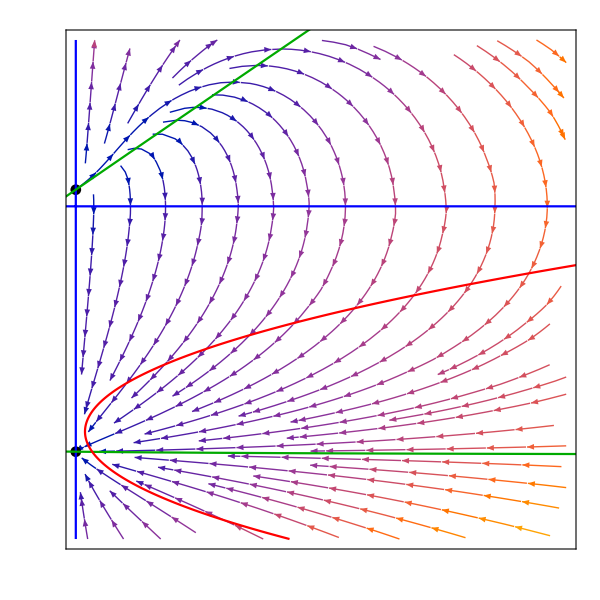

```mathematica
(*Show the plots of the phase space and its components together*)
Show[PhaseSpacexzRepellor,FPsxzRepellor,zLineRepellor,xLineRepellor,AccnxzRepellor,xzFormat,PlotRange->{{0,3},{-1,5}}]
```

### Non-Compact x - y - z Phase Space

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, dark matter, z, and the Hubble parameter, y*)
dex:=x'=-3*y*(x-ℛ)*(1+wx+ϵ*x)-q*x*y*z
dey:=y'=-y^2-(1/6)*(z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2) 
dez:=z'=-3*y*z + q*x*y*z
```

```mathematica
(*Find the fixed points of the system*)
FPsRepellor=Solve[{dex==0,dey==0,dez==0},{x,y,z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0.,z→0.0025 (48.-175. x+300. x^2)},{x→0.05,y→-0.129099,z→0.},{x→0.05,y→0.129099,z→0.},{x→3.,y→-0.975107,z→-0.1475},{x→3.,y→0.975107,z→-0.1475},{x→3.2,y→-1.0328,z→0.},{x→3.2,y→1.0328,z→0.}}

```mathematica
(*Extract the values for the fixed points and put them into a common variable name*)
FPRepellor[1]={x,y/.FPsRepellor[[1,1]],z/.FPsRepellor[[1,2]]};
FPRepellor[2]={x/.FPsRepellor[[2,1]],y/.FPsRepellor[[2,2]],z/.FPsRepellor[[2,3]]};
FPRepellor[3]={x/.FPsRepellor[[3,1]],y/.FPsRepellor[[3,2]],z/.FPsRepellor[[3,3]]};
FPRepellor[4]={x/.FPsRepellor[[6,1]],y/.FPsRepellor[[6,2]],z/.FPsRepellor[[6,3]]};
FPRepellor[5]={x/.FPsRepellor[[7,1]],y/.FPsRepellor[[7,2]],z/.FPsRepellor[[7,3]]};
FPRepellor[6]={x/.FPsRepellor[[4,1]],y/.FPsRepellor[[4,2]],z/.FPsRepellor[[4,3]]};
FPRepellor[7]={x/.FPsRepellor[[5,1]],y/.FPsRepellor[[5,2]],z/.FPsRepellor[[5,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPsRepellor=Table[FPRepellor[i],{i,1,7}];
```

```mathematica
(*Find the 3D Jacobian matrix. D[] differentiates each expression*)
JxyzRepellor=Simplify[{{D[dex,x],D[dex,y],D[dex,z]}, {D[dey,x],D[dey,y],D[dey,z]},{D[dez,x],D[dez,y],D[dez,z]}}];
JxyzRepellor//MatrixForm
```

(y (-2.4375+1.5 x-1. z) | 0.12+0.75 x^2-1. x (2.4375+z) | -x y
-0.0729167+0.25 x | -2 y | -1/6
y z | (-3+x) z | (-3+x) y)

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableRepellor=Table[{FPsRepellor[[i]]//MatrixForm,Simplify[JxyzRepellor/.{x->FPsRepellor[[i,1]],y->FPsRepellor[[i,2]],z->FPsRepellor[[i,3]]}]//MatrixForm,Eigenvalues[JxyzRepellor/.{x->FPsRepellor[[i,1]],y->FPsRepellor[[i,2]],z->FPsRepellor[[i,3]]}]//MatrixForm,Eigenvectors[JxyzRepellor/.{x->FPsRepellor[[i,1]],y->FPsRepellor[[i,2]],z->FPsRepellor[[i,3]]}]//MatrixForm},{i,1,7}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableRepellor=TableForm[FPTableRepellor,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
0.
0.0025 (48.-175. x+300. x^2)) | (0. | 0.12-2.5575 x+1.1875 x^2-0.75 x^3 | 0.
-0.0729167+0.25 x | 0. | -1/6
0. | -0.36+1.4325 x-2.6875 x^2+0.75 x^3 | 0.) | (0
-√(0.05125-0.0222656 x-0.278047 x^2+0.226562 x^3-0.1875 x^4)
√(0.05125-0.0222656 x-0.278047 x^2+0.226562 x^3-0.1875 x^4)) | (0.666667/(-0.291667+1. x) | 0 | 1.
-(1. (0.0466667-1.15458 x+3.87181 x^2-1.875 x^3+1. x^4))/((-0.291667+1. x) (-0.48+1.91 x-3.58333 x^2+1. x^3)) | -(1.33333 √(0.05125-0.0222656 x-0.278047 x^2+0.226563 x^3-0.1875 x^4))/(-0.48+1.91 x-3.58333 x^2+1. x^3) | 1.
-(1. (0.0466667-1.15458 x+3.87181 x^2-1.875 x^3+1. x^4))/((-0.291667+1. x) (-0.48+1.91 x-3.58333 x^2+1. x^3)) | (1.33333 √(0.05125-0.0222656 x-0.278047 x^2+0.226563 x^3-0.1875 x^4))/(-0.48+1.91 x-3.58333 x^2+1. x^3) | 1.)
(0.05
-0.129099
0.) | (0.304997 | 0. | 0.00645497
-0.0604167 | 0.258199 | -1/6
0. | 0. | 0.380843) | (0.380843
0.304997
0.258199) | (0.0493865 | -0.81291 | 0.580291
0.612372 | -0.790569 | 0.
0. | 1. | 0.)
(0.05
0.129099
0.) | (-0.304997 | 0. | -0.00645497
-0.0604167 | -0.258199 | -1/6
0. | 0. | -0.380843) | (-0.380843
-0.304997
-0.258199) | (0.0493865 | 0.81291 | 0.580291
0.612372 | 0.790569 | 0.
0. | 1. | 0.)
(3.2
-1.0328
0.) | (-2.43998 | 0. | 3.30495
0.727083 | 2.06559 | -1/6
0. | 0. | -0.206559) | (-2.43998
2.06559
-0.206559) | (0.987228 | -0.159313 | 0.
0. | 1. | 0.
0.808502 | -0.218642 | 0.54637)
(3.2
1.0328
0.) | (2.43998 | 0. | -3.30495
0.727083 | -2.06559 | -1/6
0. | 0. | 0.206559) | (2.43998
-2.06559
0.206559) | (0.987228 | 0.159313 | 0.
0. | 1. | 0.
0.808502 | 0.218642 | 0.54637)
(3.
-0.975107
-0.1475) | (-2.15499 | -8.88178×10^-16 | 2.92532
0.677083 | 1.95021 | -1/6
0.143828 | 0. | 0.) | (-2.33516
1.95021
0.180177) | (0.985559 | -0.158078 | -0.0607029
2.50611×10^-16 | -1. | 6.39718×10^-17
0.759915 | -0.233568 | 0.606609)
(3.
0.975107
-0.1475) | (2.15499 | -8.88178×10^-16 | -2.92532
0.677083 | -1.95021 | -1/6
-0.143828 | 0. | 0.) | (2.33516
-1.95021
-0.180177) | (-0.985559 | -0.158078 | 0.0607029
2.50611×10^-16 | 1. | 6.39718×10^-17
0.759915 | 0.233568 | 0.606609)

```mathematica
(*Plot the line of Einstein fixed points*)
EinsteinPointLineRepellor=ParametricPlot3D[{FPRepellor[1][[1]],FPRepellor[1][[2]],FPRepellor[1][[3]]},{x,0,15},PlotStyle->Red];
```

```mathematica
(*Plot the fixed points of the system*)
FPsxyzRepellor=ListPointPlot3D[Table[FPRepellor[i],{i,2,5}],PlotStyle->Black];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
AccnxyzRepellor=ContourPlot3D[z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2==0,{x,0,12},{y,-10,10},{z,0,12},ContourStyle->{Red,Opacity[0.25]},Mesh->None];
```

```mathematica
(*Plot the x-y-z phase space*)
PhaseSpacexyzRepellor=StreamPlot3D[{dex,dey,dez},{x,0,15},{y,-5,5},{z,0,10},AxesLabel->{"x","y","z"}];
```

```mathematica
(*Show the phase space and its components together*)
Show[PhaseSpacexyzRepellor,FPsxyzRepellor,EinsteinPointLineRepellor,AccnxyzRepellor,AxesLabel->{MaTeX["x",FontSize->20],MaTeX["y",FontSize->20],MaTeX["z",FontSize->20]},Ticks->{{0.,5.,10.},{-5.,0.,1.,5.},{0.,5.,10.}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}]
```

-Graphics3D-

## Plot the constant x0 and z0 surfaces

### Set-up for the phase spaces

```mathematica
(*Define a format for the x-y-z phase spaces*)
xyzFormat={AxesLabel->{MaTeX["x",FontSize->20],MaTeX["y",FontSize->20],MaTeX["z",FontSize->20]},Ticks->{{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.},{-5.,-4.,-3.,-2.,-1.,0.,1.,2.,3.,4.,5.},{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}};
```

```mathematica
(*Define the system of differential equations for the dark energy, x, and dark matter, z*)
dext:=x1'[t]==-3*y1[t]*(x1[t]-ℛ)*(1+wx+ϵ*x1[t])-q*x1[t]*y1[t]*z1[t]
deyt:=y1'[t]==-y1[t]^2-(1/6)*(z1[t]+x1[t]*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x1[t]^2) 
dezt:=z1'[t]==-3*y1[t]*z1[t] + q*x1[t]*y1[t]*z1[t]
```

```mathematica
(*Define Ωx0 and Ωm0 using data from Planck 2018*)
Ωx0=0.6889;
Ωm0=0.3111;
```

```mathematica
(*Set a value for α, which sets the value of the low energy cosmological constant*)
α=0.5;
```

```mathematica
(*Define the initial conditions, where a0 = 1 and K is defined as k/ρ* *)
(*Trajectories are plotted on a constant x0-z0 surface, where x0 is fixed for all cases and z0 is fixed for each phase space*)
(*K and y0 differ for each trajectory in each phase space*)

x0=ℛ/α;
y0=Sqrt[x0/3+z0/3-K];
```

```mathematica
(*Define values of K using the range of Ωk0 allowed by Planck 2018*)
Ωk0Open=0.003;
Ωk0Closed=-0.001;

KDensityParametersOpen=-Ωk0Open*ℛ/(3*α*Ωx0)
KDensityParametersClosed=-Ωk0Closed*ℛ/(3*α*Ωx0)
```

-0.000145159

0.0000483863

### Limiting Case with 1 Einstein fixed point

#### Find the Einstein Fixed Point

```mathematica
(*Fix z0 so that there is one Einstein fixed point on the surface*)
z0LimitingRepellor=0.0058;
```

```mathematica
(*Substitute z0Limiting into y0 for this case*)
y0LimitingRepellor=y0/.z0->z0LimitingRepellor
```

√(0.0352667-K)

```mathematica
(*Numerically solve the system of equations using the initial conditions defined for the limiting case with one Einstein fixed point*)
trajLimitingRepellor[K_]=NDSolve[{dext,deyt,dezt,x1[0]==x0,y1[0]==y0LimitingRepellor,z1[0]==z0LimitingRepellor},{x1,y1,z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition √(0.0352667-1. K) is not a number or a rectangular array of numbers.

NDSolve[{x1'[t]==-3 (0.8-0.25 x1[t]) (-0.05+x1[t]) y1[t]-x1[t] y1[t] z1[t],y1'[t]==-y1[t]^2+1/6 (0.12-0.4375 x1[t]+0.75 x1[t]^2-z1[t]),z1'[t]==-3 y1[t] z1[t]+x1[t] y1[t] z1[t],x1[0]==0.1,y1[0]==√(0.0352667-K),z1[0]==0.0058},{x1,y1,z1},{t,-100,100}]

```mathematica
(*Set-up tables of all x1 and z1 values to be used to find the x and z value of the Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
xTableSolLimitingRepellor=Table[x1[i]/.trajLimitingRepellor[0],{i,-100,100,.01}];
zTableSolLimitingRepellor=Table[z1[i]/.trajLimitingRepellor[0],{i,-100,100,.01}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSolLimitingRepellor=(zTableSolLimitingRepellor)+(xTableSolLimitingRepellor)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSolLimitingRepellor)^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSolLimiting that is closest to zero. When EinsteinPlotValuesSolLimiting = 0 (y = 0), there is an Einstein point*)
NearestToZeroLimitingRepellor=Flatten[Nearest[EinsteinPlotValuesSolLimitingRepellor,0]]
```

{-0.000860698}

```mathematica
(*Find the position of NearestToZeroLimiting in the EinsteinPlotValuesSolLimiting array*)
PositionNearestToZeroLimitingRepellor=Flatten[Position[EinsteinPlotValuesSolLimitingRepellor,NearestToZeroLimitingRepellor]]
```

{9659}

```mathematica
(*Find the Einstein point by finding the x and z values in xTableSolLimiting and zTableSolLimiting at PositionNearestToZeroLimiting*)
EinsteinPointLimitingRepellor=Flatten[{xTableSolLimitingRepellor[[PositionNearestToZeroLimitingRepellor]],0,zTableSolLimitingRepellor[[PositionNearestToZeroLimitingRepellor]]}]
```

{0.436572,0,0.0710854}

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for the Einstein fixed point*)
EinsteinTableLimitingRepellor=Table[{EinsteinPointLimitingRepellor//MatrixForm,Simplify[JxyzRepellor/.{x->EinsteinPointLimitingRepellor[[1]],y->EinsteinPointLimitingRepellor[[2]],z->EinsteinPointLimitingRepellor[[3]]}]//MatrixForm,Eigenvalues[JxyzRepellor/.{x->EinsteinPointLimitingRepellor[[1]],y->EinsteinPointLimitingRepellor[[2]],z->EinsteinPointLimitingRepellor[[3]]}]//MatrixForm,Eigenvectors[JxyzRepellor/.{x->EinsteinPointLimitingRepellor[[1]],y->EinsteinPointLimitingRepellor[[2]],z->EinsteinPointLimitingRepellor[[3]]}]//MatrixForm},1];
```

```mathematica
(*Use TableForm to display the Einstein fixed point with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableEinsteinPointLimitingRepellor=TableForm[EinsteinTableLimitingRepellor,TableHeadings->{None,{"Einstein Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Einstein Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.436572
0
0.0710854) | (0. | -0.832232 | 0.
0.0362263 | 0 | -1/6
0. | -0.182222 | 0.) | (-0.0148888
0.0148888
5.08148×10^-15) | (-0.976709 | -0.0174736 | -0.213856
0.976709 | -0.0174736 | 0.213856
0.977183 | -6.02311×10^-15 | 0.212399)

```mathematica
(*Set-up tables of all x1 and z1 values with a bigger t increment*)
xTableSolLimitingFullRepellor=Table[x1[i]/.trajLimitingRepellor[0],{i,-100,100,.1}];
zTableSolLimitingFullRepellor=Table[z1[i]/.trajLimitingRepellor[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0*)
EinsteinPlotValuesSolLimitingFullRepellor=(zTableSolLimitingFullRepellor)+(xTableSolLimitingFullRepellor)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSolLimitingFullRepellor)^2;
```

```mathematica
(*Merge the xTableSolLimitingFull values and the EinsteinPlotValuesSolLimitingFull values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsLimitingRepellor=MapThread[h,{xTableSolLimitingFullRepellor,EinsteinPlotValuesSolLimitingFullRepellor}];
```

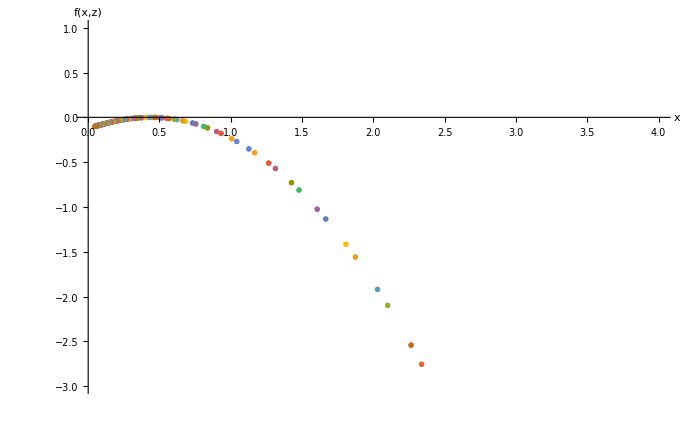

```mathematica
(*Plot x vs the remaining equation when y' = 0*)
(*When f(x,z) = 0, an Einstein point exists*)
EinsteinPlotLimitingRepellor=ListPlot[EinsteinPointSolutionsLimitingRepellor,PlotRange->{{0,4},{-3,1}},AxesLabel->{"x","f(x,z)"}]
```

#### Plot the x-y-z Phase Space

```mathematica
(*Find the maximum value of K for this combination of x0 and z0 such that y0 is not imaginary*)
KMaxLimitingRepellor=K/.Solve[y0LimitingRepellor==0,K][[1]]
```

0.0352667

```mathematica
(*Solve trajLimiting[K] for different values of K*)
```

```mathematica
solLimitingRepellor[1]=trajLimitingRepellor[KDensityParametersOpen]
```

NDSolve::ndsz: At t == -7.98089, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solLimitingRepellor[2]=trajLimitingRepellor[KDensityParametersClosed]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solLimitingRepellor[3]=trajLimitingRepellor[-.1]
```

NDSolve::ndsz: At t == -2.82253, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solLimitingRepellor[4]=trajLimitingRepellor[KMaxLimitingRepellor]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solLimitingRepellor[5]=trajLimitingRepellor[0.002]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the trajectories for the different values of K given above*)
(*Plot the solutions using a value of K found from the range of Ωk0 allowed by Planck 2018 in purple*)
```

```mathematica
trajLimitingxyzRepellor[1]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimitingRepellor[1],{t,-7.97,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingxyzRepellor[2]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimitingRepellor[2],{t,-100,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingxyzRepellor[3]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimitingRepellor[3],{t,-2.81,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingxyzRepellor[4]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimitingRepellor[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingxyzRepellor[5]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimitingRepellor[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajLimitingCaseRepellor=Table[trajLimitingxyzRepellor[i],{i,1,5}];
```

```mathematica
(*Plot the Einstein fixed point*)
EinsteinFixedPointsLimitingRepellor=ListPointPlot3D[{EinsteinPointLimitingRepellor},PlotStyle->Black];
```

```mathematica
(*Solve the x-y-z system around the Einstein fixed point to plot the Closed Friedmann Separatrix (CFS)*)
CFSLimitingSolRepellor=NDSolve[{dext,deyt,dezt,x1[0]==EinsteinPointLimitingRepellor[[1]],y1[0]==0,z1[0]==EinsteinPointLimitingRepellor[[3]]},{x1,y1,z1},{t,-100,100}]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the CFS*)
CFSLimitingRepellor=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.CFSLimitingSolRepellor,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
(*Show the x-y-z phase space*)
Show[trajLimitingCaseRepellor,EinsteinFixedPointsLimitingRepellor,CFSLimitingRepellor,AccnxyzRepellor,FPsxyzRepellor,xyzFormat,PlotRange->{{0,4},{-4,4},{-0.5,1}}]
```

-Graphics3D-

#### Plot the x-z Projection

```mathematica
(*Plot one solution on the x-z plane*)
trajLimitingxzRepellor=ParametricPlot[Evaluate[{{z1[t],x1[t]}}/.solLimitingRepellor[1],{t,-8.57,100},PlotStyle -> {{Black, Thick,Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.03,.03,0},1]]],Arrow[x]};
```

InterpolatingFunction::dmval: Input value {-8.57978} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
(*Plot the Einstein fixed point on the x-z plane*)
EinsteinFixedPointsLimitingxzRepellor=ListPlot[{{EinsteinPointLimitingRepellor[[3]],EinsteinPointLimitingRepellor[[1]]}},PlotStyle->Black];
```

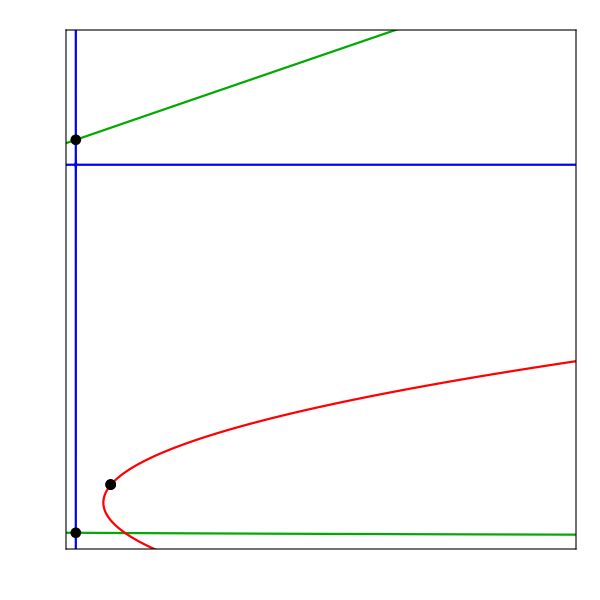

```mathematica
(*Show the x-z phase space with the a'' = 0 (red), x' = 0 (green) and z' = 0 (purple) curves*)
Show[trajLimitingxzRepellor,xLineRepellor,zLineRepellor,AccnxzRepellor,FPsxzRepellor,EinsteinFixedPointsLimitingxzRepellor,xzFormat,PlotRange->{{0,1},{0,4}}]
```

### Two Einstein Fixed Points

#### Find the Einstein Fixed Points

```mathematica
(*Fix z0 using the density parameters. In this case there are two Einstein fixed points*)
z0TwoEinsteinPointsRepellor=Ωm0*ℛ/(Ωx0*α)
```

0.0451589

```mathematica
(*Substitute z0TwoEinsteinPoints into y0 for this case*)
y0TwoEinsteinPointsRepellor=y0/.z0->z0TwoEinsteinPointsRepellor
```

√(0.0483863-K)

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajTwoEinsteinPointsRepellor[K_]=NDSolve[{dext,deyt,dezt,x1[0]==x0,y1[0]==y0TwoEinsteinPointsRepellor,z1[0]==z0TwoEinsteinPointsRepellor},{x1,y1,z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition √(0.0483863-1. K) is not a number or a rectangular array of numbers.

NDSolve[{x1'[t]==-3 (0.8-0.25 x1[t]) (-0.05+x1[t]) y1[t]-x1[t] y1[t] z1[t],y1'[t]==-y1[t]^2+1/6 (0.12-0.4375 x1[t]+0.75 x1[t]^2-z1[t]),z1'[t]==-3 y1[t] z1[t]+x1[t] y1[t] z1[t],x1[0]==0.1,y1[0]==√(0.0483863-K),z1[0]==0.0451589},{x1,y1,z1},{t,-100,100}]

```mathematica
(*Set-up tables of x1 and z1 values to be used to find the x and z value of the first Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
xTableSol1TwoEinsteinPointsRepellor=Table[x1[i]/.trajTwoEinsteinPointsRepellor[0],{i,-2,100,.01}];
zTableSol1TwoEinsteinPointsRepellor=Table[z1[i]/.trajTwoEinsteinPointsRepellor[0],{i,-2,100,.01}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol1TwoEinsteinPointsRepellor=(zTableSol1TwoEinsteinPointsRepellor)+(xTableSol1TwoEinsteinPointsRepellor)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol1TwoEinsteinPointsRepellor)^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol1TwoEinsteinPoints that is closest to zero. When EinsteinPlotValuesSol1TwoEinsteinPoints = 0 (y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints1Repellor=Flatten[Nearest[EinsteinPlotValuesSol1TwoEinsteinPointsRepellor,0]]
```

{-0.000146739}

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints1 in the EinsteinPlotValuesSol1TwoEinsteinPoints*)
PositionNearestToZeroTwoEinsteinPoints1Repellor=Flatten[Position[EinsteinPlotValuesSol1TwoEinsteinPointsRepellor,NearestToZeroTwoEinsteinPoints1Repellor]]
```

{125}

```mathematica
(*Find the Einstein point by finding the x and z values in xTableSol1TwoEinsteinPoints and zTableSol1TwoEinsteinPoints at PositionNearestToZeroTwoEinsteinPoints1*)
EinsteinPoint1TwoEinsteinPointsRepellor=Flatten[{xTableSol1TwoEinsteinPointsRepellor[[PositionNearestToZeroTwoEinsteinPoints1Repellor]],0,zTableSol1TwoEinsteinPointsRepellor[[PositionNearestToZeroTwoEinsteinPoints1Repellor]]}]
```

{0.127584,0,0.0762435}

```mathematica
(*Set-up tables of x1 and z1 values to be used to find the x and z value of the second Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
xTableSol2TwoEinsteinPointsRepellor=Table[x1[i]/.trajTwoEinsteinPointsRepellor[0],{i,-5.6,-3.2,.001}];
zTableSol2TwoEinsteinPointsRepellor=Table[z1[i]/.trajTwoEinsteinPointsRepellor[0],{i,-5.6,-3.2,.001}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol2TwoEinsteinPointsRepellor=(zTableSol2TwoEinsteinPointsRepellor)+(xTableSol2TwoEinsteinPointsRepellor)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol2TwoEinsteinPointsRepellor)^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol2TwoEinsteinPoints that is closest to zero. When EinsteinPlotValuesSol2TwoEinsteinPoints = 0 (y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints2Repellor=Flatten[Nearest[EinsteinPlotValuesSol2TwoEinsteinPointsRepellor,0]]
```

{-0.00134504}

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints2 in the EinsteinPlotValuesSol2TwoEinsteinPoints array*)
PositionNearestToZeroTwoEinsteinPoints2Repellor=Flatten[Position[EinsteinPlotValuesSol2TwoEinsteinPointsRepellor,NearestToZeroTwoEinsteinPoints2Repellor]]
```

{2349}

```mathematica
(*Find the Einstein point by finding the x and z values in xTableSol2TwoEinsteinPoints and zTableSol2TwoEinsteinPoints at PositionNearestToZeroTwoEinsteinPoints2*)
EinsteinPoint2TwoEinsteinPointsRepellor=Flatten[{xTableSol2TwoEinsteinPointsRepellor[[PositionNearestToZeroTwoEinsteinPoints2Repellor]],0,zTableSol2TwoEinsteinPointsRepellor[[PositionNearestToZeroTwoEinsteinPoints2Repellor]]}]
```

{1.61749,0,1.37321}

```mathematica
(*Put the Einstein fixed points into a common variable name*)
EinsteinPointTwoEPtsRepellor[1]=EinsteinPoint1TwoEinsteinPointsRepellor;
EinsteinPointTwoEPtsRepellor[2]=EinsteinPoint2TwoEinsteinPointsRepellor;
```

```mathematica
(*Put the Einstein fixed points into a table*)
EinsteinPointsTwoEPtsRepellor=Table[EinsteinPointTwoEPtsRepellor[i],{i,1,2}];
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each Einstein fixed point*)
EinsteinPointTableTwoEinsteinPointsRepellor=Table[{EinsteinPointsTwoEPtsRepellor[[i]]//MatrixForm,Simplify[JxyzRepellor/.{x->EinsteinPointsTwoEPtsRepellor[[i,1]],y->EinsteinPointsTwoEPtsRepellor[[i,2]],z->EinsteinPointsTwoEPtsRepellor[[i,3]]}]//MatrixForm,Eigenvalues[JxyzRepellor/.{x->EinsteinPointsTwoEPtsRepellor[[i,1]],y->EinsteinPointsTwoEPtsRepellor[[i,2]],z->EinsteinPointsTwoEPtsRepellor[[i,3]]}]//MatrixForm,Eigenvectors[JxyzRepellor/.{x->EinsteinPointsTwoEPtsRepellor[[i,1]],y->EinsteinPointsTwoEPtsRepellor[[i,2]],z->EinsteinPointsTwoEPtsRepellor[[i,3]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the Einstein fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableTwoEinsteinPointsRepellor=TableForm[EinsteinPointTableTwoEinsteinPointsRepellor,TableHeadings->{None,{"Einstein Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Einstein Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.127584
0
0.0762435) | (0. | -0.188506 | 0.
-0.0410206 | 0 | -1/6
0. | -0.219003 | 0.) | (0.210317
-0.210317
2.54105×10^-17) | (0.527446 | -0.588474 | 0.612779
0.527446 | 0.588474 | 0.612779
-0.971022 | 2.0168×10^-17 | 0.238991)
(1.61749
0
1.37321) | (0. | -4.08157 | 0.
0.331456 | 0 | -1/6
0. | -1.89847 | 0.) | (1.09548×10^-16+1.01806 ⅈ
1.09548×10^-16-1.01806 ⅈ
8.26236×10^-17+0. ⅈ) | (0.88438+0. ⅈ | -5.23779×10^-17-0.22059 ⅈ | 0.411354-2.75461×10^-17 ⅈ
0.88438+0. ⅈ | -5.23779×10^-17+0.22059 ⅈ | 0.411354+2.75461×10^-17 ⅈ
0.449237+0. ⅈ | 2.94913×10^-17+0. ⅈ | 0.893413+0. ⅈ)

```mathematica
(*Set-up tables of all x1 and z1 values*)
xTableSolTwoEinsteinPointsFullRepellor=Table[x1[i]/.trajTwoEinsteinPointsRepellor[0],{i,-100,100,.1}];
zTableSolTwoEinsteinPointsFullRepellor=Table[z1[i]/.trajTwoEinsteinPointsRepellor[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0*)
EinsteinPlotValuesSolTwoEinsteinPointsFullRepellor=(zTableSolTwoEinsteinPointsFullRepellor)+(xTableSolTwoEinsteinPointsFullRepellor)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSolTwoEinsteinPointsFullRepellor)^2;
```

```mathematica
(*Merge the xTableSolTwoEinsteinPointsFull values and the EinsteinPlotValuesSolTwoEinsteinPointsFull values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsTwoEinsteinPointsRepellor=MapThread[h,{xTableSolTwoEinsteinPointsFullRepellor,EinsteinPlotValuesSolTwoEinsteinPointsFullRepellor}];
```

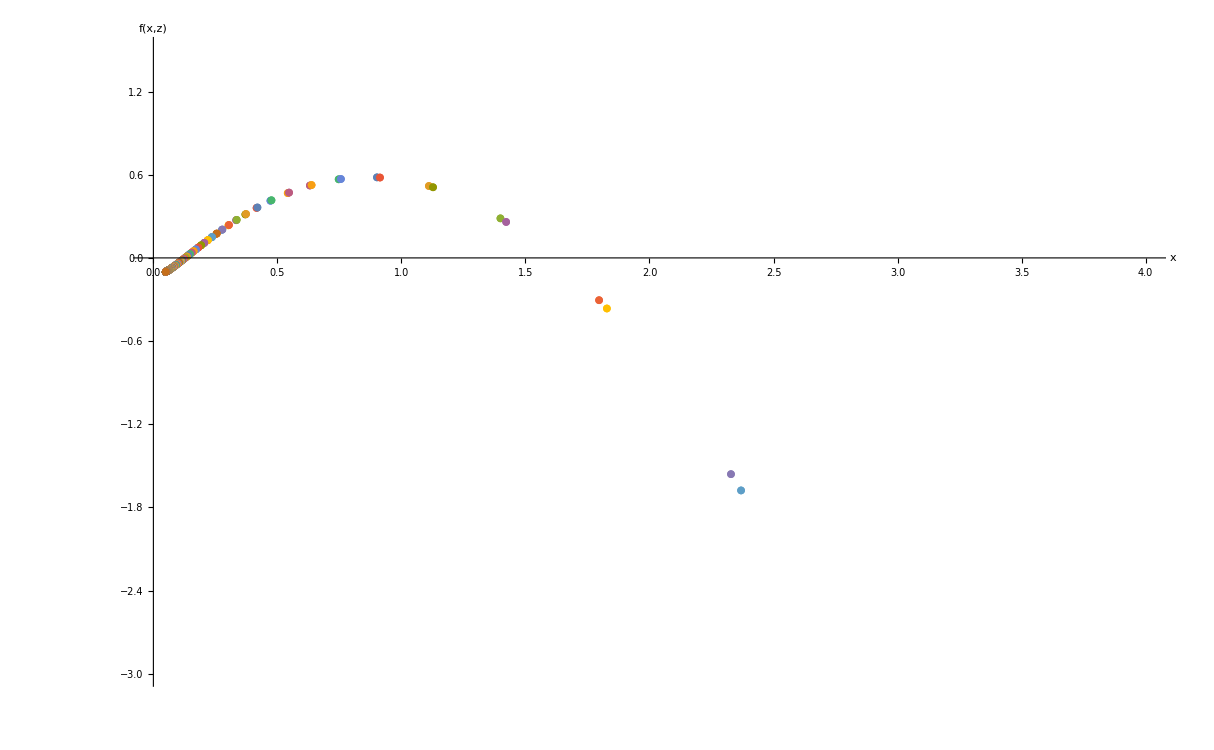

```mathematica
(*Plot x vs the remaining equation when y' = 0*)
(*When f(x,z) = 0, an Einstein point exists*)
EinsteinPlotTwoEinsteinPointsRepellor=ListPlot[EinsteinPointSolutionsTwoEinsteinPointsRepellor,PlotRange->{{0,4},{-3,1.5}},AxesLabel->{"x","f(x,z)"}]
```

#### Plot the x-y-z Phase Space

```mathematica
(*Find the maximum value of K for this combination of x0 and z0 so that y0 is not imaginary*)
KMaxTwoEinsteinPointsRepellor=K/.Flatten[Solve[y0TwoEinsteinPointsRepellor==0,K]]
```

0.0483863

```mathematica
(*Solve trajTwoEinsteinPoints[K] for different values of K*)
```

```mathematica
solTwoEinsteinPointsRepellor[1]=trajTwoEinsteinPointsRepellor[KDensityParametersOpen]
```

NDSolve::ndsz: At t == -6.53774, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsRepellor[2]=trajTwoEinsteinPointsRepellor[KDensityParametersClosed]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsRepellor[3]=trajTwoEinsteinPointsRepellor[-.1]
```

NDSolve::ndsz: At t == -2.61973, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsRepellor[4]=trajTwoEinsteinPointsRepellor[KMaxTwoEinsteinPointsRepellor]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsRepellor[5]=trajTwoEinsteinPointsRepellor[0.005]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the trajectories for the different values of K given above*)
(*Plot the solutions using a value of K found from the range of Ωk0 allowed by Planck 2018 in purple*)
```

```mathematica
trajTwoEinsteinPointsxyzRepellor[1]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsRepellor[1],{t,-6.53,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyzRepellor[2]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsRepellor[2],{t,-100,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyzRepellor[3]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsRepellor[3],{t,-2.61,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyzRepellor[4]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsRepellor[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75],Dashed}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
trajTwoEinsteinPointsxyzRepellor[5]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsRepellor[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Solve the x-y-z system using the centre Einstein fixed point for x0 and z0 to plot a cyclic trajectory*)
CyclicTrajTwoEinsteinPointsRepellor=NDSolve[{dext,deyt,dezt,x1[0]==EinsteinPoint2TwoEinsteinPointsRepellor[[1]],y1[0]==0.436,z1[0]==EinsteinPoint2TwoEinsteinPointsRepellor[[3]]},{x1,y1,z1},{t,-100,100}];
```

```mathematica
(*Plot the cyclic trajectory*)
trajTwoEinsteinPointsxyzRepellor[6]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.CyclicTrajTwoEinsteinPointsRepellor,{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajTwoEinsteinPointsCaseRepellor=Table[trajTwoEinsteinPointsxyzRepellor[i],{i,1,6}];
```

```mathematica
(*Plot the Einstein fixed points*)
EinsteinFixedPointsTwoEinsteinPointsRepellor=ListPointPlot3D[{EinsteinPoint1TwoEinsteinPointsRepellor,EinsteinPoint2TwoEinsteinPointsRepellor},PlotStyle->Black];
```

```mathematica
(*Solve the x-y-z system around the Einstein fixed point to plot the Closed Friedmann Separatrix (CFS)*)
CFSTwoEinsteinPointsSolRepellor=NDSolve[{dext,deyt,dezt,x1[0]==EinsteinPoint1TwoEinsteinPointsRepellor[[1]],y1[0]==-0.0005,z1[0]==EinsteinPoint1TwoEinsteinPointsRepellor[[3]]},{x1,y1,z1},{t,-100,100}]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the CFS*)
CFSTwoEinsteinPointsRepellor=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.CFSTwoEinsteinPointsSolRepellor,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Show the x-y-z phase space*)
Show[trajTwoEinsteinPointsCaseRepellor,CFSTwoEinsteinPointsRepellor,EinsteinFixedPointsTwoEinsteinPointsRepellor,AccnxyzRepellor,FPsxyzRepellor,xyzFormat,PlotRange->{{0,5},{-5,5},{0,2}}]
```

-Graphics3D-

#### Plot the x-z Projection

```mathematica
(*Plot one solution on the x-z plane*)
trajTwoEinsteinPointsxzRepellor=ParametricPlot[Evaluate[{{z1[t],x1[t]}}/.solTwoEinsteinPointsRepellor[1],{t,-6.53,100},PlotStyle -> {{Black, Thick,Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.03,.03,0},1]]],Arrow[x]};;
```

```mathematica
(*Plot the Einstein fixed points on the x-z plane*)
EinsteinFixedPointsTwoEinsteinPointsxzRepellor=ListPlot[{{EinsteinPoint1TwoEinsteinPointsRepellor[[3]],EinsteinPoint1TwoEinsteinPointsRepellor[[1]]},{EinsteinPoint2TwoEinsteinPointsRepellor[[3]],EinsteinPoint2TwoEinsteinPointsRepellor[[1]]}},PlotStyle->Black];
```

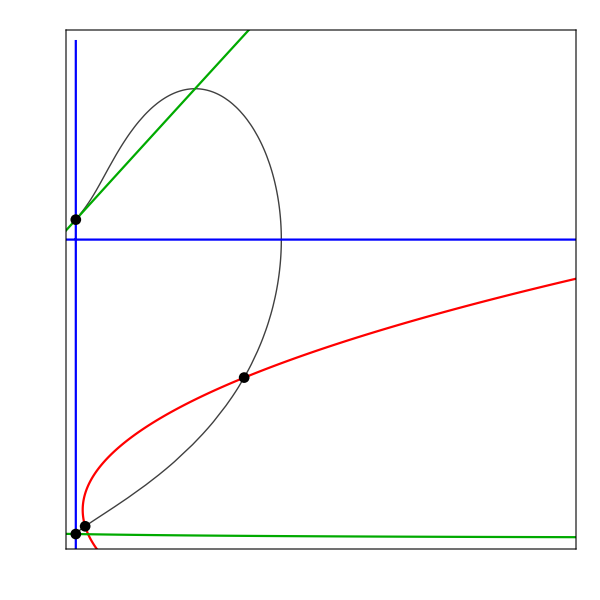

```mathematica
(*Show the x-z phase space with the a'' = 0 (red), x' = 0 (green) and z' = 0 (purple) curves*)
Show[trajTwoEinsteinPointsxzRepellor,AccnxzRepellor,xLineRepellor,zLineRepellor,FPsxzRepellor,EinsteinFixedPointsTwoEinsteinPointsxzRepellor,xzFormat,PlotRange->{{0,4},{0,5}}]
```

### No Einstein Fixed Points

#### Plot to show that there are no Einstein fixed points

```mathematica
(*Fix z0 such that there are no Einstein fixed points on the surface*)
z0NoEinsteinPointsRepellor=0.003;
```

```mathematica
(*Substitute z0NoEinsteinPoints into y0 for this case*)
y0NoEinsteinPointsRepellor=y0/.z0->z0NoEinsteinPointsRepellor
```

√(0.0343333-K)

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajNoEinsteinPointsRepellor[K_]=NDSolve[{dext,deyt,dezt,x1[0]==x0,y1[0]==y0NoEinsteinPointsRepellor,z1[0]==z0NoEinsteinPointsRepellor},{x1,y1,z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition √(0.0343333-1. K) is not a number or a rectangular array of numbers.

NDSolve[{x1'[t]==-3 (0.8-0.25 x1[t]) (-0.05+x1[t]) y1[t]-x1[t] y1[t] z1[t],y1'[t]==-y1[t]^2+1/6 (0.12-0.4375 x1[t]+0.75 x1[t]^2-z1[t]),z1'[t]==-3 y1[t] z1[t]+x1[t] y1[t] z1[t],x1[0]==0.1,y1[0]==√(0.0343333-K),z1[0]==0.003},{x1,y1,z1},{t,-100,100}]

```mathematica
(*Set-up tables of all x1 and z1 values*)
xTableSolNoEinsteinPointsFullRepellor=Table[x1[i]/.trajNoEinsteinPointsRepellor[0],{i,-100,100,.1}];
zTableSolNoEinsteinPointsFullRepellor=Table[z1[i]/.trajNoEinsteinPointsRepellor[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0*)
EinsteinPlotValuesSolNoEinsteinPointsFullRepellor=(zTableSolNoEinsteinPointsFullRepellor)+(xTableSolNoEinsteinPointsFullRepellor)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSolNoEinsteinPointsFullRepellor)^2;
```

```mathematica
(*Merge the xTableSolNoEinsteinPointsFull values and the EinsteinPlotValuesSolNoEinsteinPointsFull values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsNoEinsteinPointsRepellor=MapThread[h,{xTableSolNoEinsteinPointsFullRepellor,EinsteinPlotValuesSolNoEinsteinPointsFullRepellor}];
```

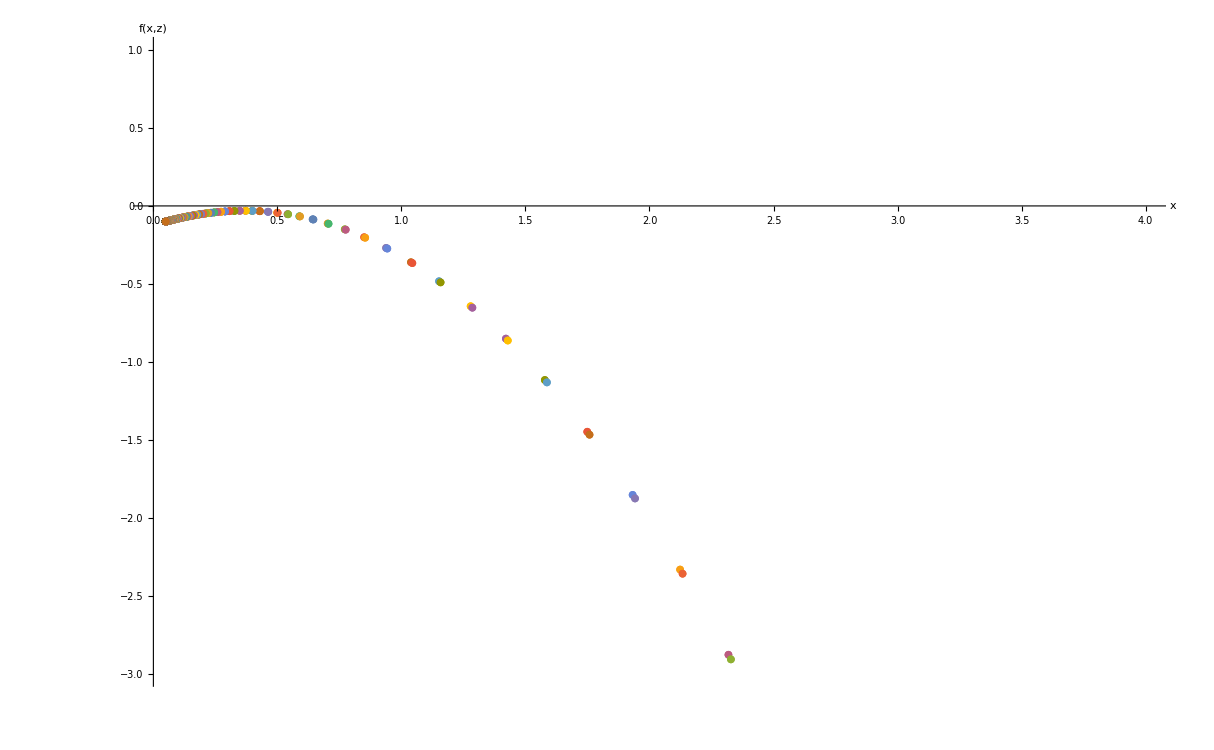

```mathematica
(*Plot x vs the remaining equation when y' = 0*)
(*Here, f(x,z) is never zero, so there are no Einstein fixed points*)
EinsteinPlotNoEinsteinPointsRepellor=ListPlot[EinsteinPointSolutionsNoEinsteinPointsRepellor,PlotRange->{{0,4},{-3,1}},AxesLabel->{"x","f(x,z)"}]
```

#### Plot the x-y-z Phase Space

```mathematica
(*Find the maximum value of K for this combination of x0 and z0 such that y0 is not imaginary*)
KMaxNoEinsteinPointsRepellor=K/.Solve[y0NoEinsteinPointsRepellor==0,K][[1]]
```

0.0343333

```mathematica
(*Solve trajNoEinsteinPoints[K] for different values of K*)
```

```mathematica
solNoEinsteinPointsRepellor[1]=trajNoEinsteinPointsRepellor[KDensityParametersOpen]
```

NDSolve::ndsz: At t == -8.24071, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsRepellor[2]=trajNoEinsteinPointsRepellor[KDensityParametersClosed]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsRepellor[3]=trajNoEinsteinPointsRepellor[-.1]
```

NDSolve::ndsz: At t == -2.84158, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsRepellor[4]=trajNoEinsteinPointsRepellor[0.01]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsRepellor[5]=trajNoEinsteinPointsRepellor[KMaxNoEinsteinPointsRepellor]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the trajectories for the different values of K given above.*)
(*Plot the solutions using a value of K found from the range of Ωk0 allowed by Planck 2018 in purple*)
```

```mathematica
trajNoEinsteinPointsxyzRepellor[1]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPointsRepellor[1],{t,-8.23,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsxyzRepellor[2]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPointsRepellor[2],{t,-100,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsxyzRepellor[3]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPointsRepellor[3],{t,-2.83,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsxyzRepellor[4]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPointsRepellor[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsxyzRepellor[5]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPointsRepellor[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajNoEinsteinPointsPlotsRepellor=Table[trajNoEinsteinPointsxyzRepellor[i],{i,1,5}];
```

```mathematica
(*Show the x-y-z phase space*)
Show[trajNoEinsteinPointsPlotsRepellor,AccnxyzRepellor,FPsxyzRepellor,xyzFormat,PlotRange->{{0,4},{-4,4},{0,1}}]
```

-Graphics3D-

#### Plot the x-z Projection

```mathematica
(*Plot one solution on the x-z plane*)
trajNoEinsteinPointsxzRepellor=ParametricPlot[Evaluate[{{z1[t],x1[t]}}/.solNoEinsteinPointsRepellor[1],{t,-8.23,100},PlotStyle -> {{Black,Thick, Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.03,0,.03,0},1]]],Arrow[x]};
```

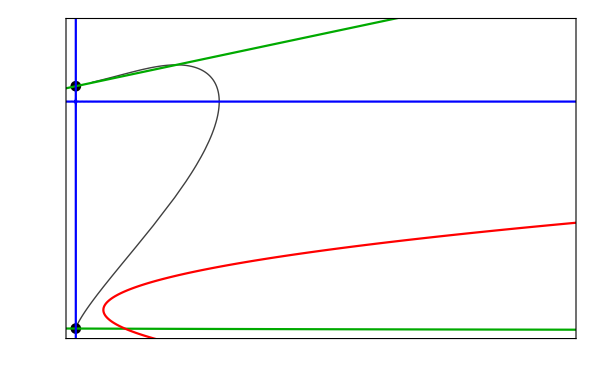

```mathematica
(*Show the x-z phase space with the a'' = 0 (red), x' = 0 (green) and z' = 0 (purple) curves*)
Show[FPsxzRepellor,trajNoEinsteinPointsxzRepellor,xLineRepellor,zLineRepellor,AccnxzRepellor,xzFormat,PlotRange->{{0,1},{0,4}}]
```

## Compact Phase Spaces: constant X0 and Z0 surfaces

### Define parameter values and set-up initial conditions

```mathematica
(*Set parameter values*)
wx=-0.2;
q=1;
ϵ=-0.25;
ℛ=0.05;
```

```mathematica
(*Define Ωx0 and Ωm0 using data from Planck 2018*)
Ωx0=0.6889;
Ωm0=0.3111;
```

```mathematica
(*Set a value for α, which sets the value of the low energy cosmological constant*)
α=0.5;
```

```mathematica
(*Define the initial conditions, where a0 = 1 and K is defined as k/ρ* *)

x0=ℛ/α;
y0=Sqrt[x0/3+Z0/(3*(1-Z0))-K];
```

```mathematica
(*Compactify the initial conditions*)
(*Trajectories are plotted on a constant X0-Z0 surface, where X0 is fixed for all cases and Z0 is fixed for each phase space*)
(*K and Y0 differ for each trajectory in each phase space*)

X0=x0/(1+x0);
Y0=y0/Sqrt[1+y0^2];
```

```mathematica
(*Define values of K using the range of Ωk0 allowed by Planck 2018*)
Ωk0Open=0.003;
Ωk0Closed=-0.001;

KDensityParametersOpen=-Ωk0Open*ℛ/(3*α*Ωx0)
KDensityParametersClosed=-Ωk0Closed*ℛ/(3*α*Ωx0)
```

-0.000145159

0.0000483863

### Set-up for the compact X-Y-Z system

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*Define a format style for the X-Y-Z phase spaces*)
XYZCompactFormat={AxesLabel->{MaTeX["X",FontSize->22],MaTeX["Y",FontSize->22],MaTeX["Z",FontSize->22]},Ticks->{{0.,0.5,1.0},{-1,-0.5,0.,0.5,1.0},{0.,0.5,1.0}},PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->22}};
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y*)
deX:=X'=-3*(Y/((1-Y^2)^(1/2)))*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))*(Y/((1-Y^2)^(1/2)))
deY:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)
deZ:=Z'=-3*Z*(1-Z)*(Y/((1-Y^2)^(1/2))) + q*(X/(1-X))*Z*(1-Z)*(Y/((1-Y^2)^(1/2)))
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y in terms of time, t*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*(X1[t]-ℛ*(1-X1[t]))*((1+wx)*(1-X1[t])+ϵ*X1[t])-q*X1[t]*(1-X1[t])*(Z1[t]/(1-Z1[t]))*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((Z1[t]/(1-Z1[t]))+(X1[t]/(1-X1[t]))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X1[t]^2/((1-X1[t])^2))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2))) + q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
```

```mathematica
(*Find the fixed points of the system*)
FPsXYZRepellor=Solve[{deX==0,deY==0,deZ==0},{X,Y,Z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Y→0.,Z→(48.-271. X+523. X^2)/(448.-1071. X+923. X^2)},{X→0.75,Y→-0.698139,Z→-0.173021},{X→0.75,Y→0.698139,Z→-0.173021},{X→0.761905,Y→-0.718421,Z→0.},{X→0.047619,Y→-0.128037,Z→0.},{X→0.259082-0.157018 ⅈ,Y→0.,Z→0.},{X→0.259082+0.157018 ⅈ,Y→0.,Z→0.},{X→0.047619,Y→0.128037,Z→0.},{X→0.761905,Y→0.718421,Z→0.},{X→0.75,Y→0.,Z→0.847503}}

```mathematica
(*Extract the values of the fixed points and put them into a common variable name*)
FPXYZRepellor[1]={X,Y/.FPsXYZRepellor[[1,1]],Z/.FPsXYZRepellor[[1,2]]};
FPXYZRepellor[2]={X/.FPsXYZRepellor[[4,1]],Y/.FPsXYZRepellor[[4,2]],Z/.FPsXYZRepellor[[4,3]]};
FPXYZRepellor[3]={X/.FPsXYZRepellor[[9,1]],Y/.FPsXYZRepellor[[9,2]],Z/.FPsXYZRepellor[[9,3]]};
FPXYZRepellor[4]={X/.FPsXYZRepellor[[8,1]],Y/.FPsXYZRepellor[[8,2]],Z/.FPsXYZRepellor[[8,3]]};FPXYZRepellor[5]={X/.FPsXYZRepellor[[5,1]],Y/.FPsXYZRepellor[[5,2]],Z/.FPsXYZRepellor[[5,3]]};
FPXYZRepellor[6]={X/.FPsXYZRepellor[[10,1]],Y/.FPsXYZRepellor[[10,2]],Z/.FPsXYZRepellor[[10,3]]};
FPXYZRepellor[7]={X/.FPsXYZRepellor[[2,1]],Y/.FPsXYZRepellor[[2,2]],Z/.FPsXYZRepellor[[2,3]]};
FPXYZRepellor[8]={X/.FPsXYZRepellor[[3,1]],Y/.FPsXYZRepellor[[3,2]],Z/.FPsXYZRepellor[[3,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPXYZTableRepellor=Table[FPXYZRepellor[i],{i,1,8}];
```

```mathematica
(*Find the 3D Jacobian matrix. D[] differentiates each expression*)
JCompactXYZRepellor=Simplify[{{D[deX,X],D[deX,Y],D[deX,Z]},{D[deY,X],D[deY,Y],D[deY,Z]},{D[deZ,X],D[deZ,Y],D[deZ,Z]}}];
JCompactXYZRepellor//MatrixForm
```

((Y (2.6775-1.6775 Z+X (-6.615+4.615 Z)))/(√(1-Y^2) (-1.+Z)) | (0.12+X^2 (3.3075-2.3075 Z)-0.12 Z+X (-2.6775+1.6775 Z))/(√(1-Y^2) (-1.+Y^2) (-1.+Z)) | ((-1+X) X Y)/(√(1-Y^2) (-1+Z)^2)
(0.322917 (-0.225806+1. X) √(1-Y^2) (-1.+Y^2))/(-1.+X)^3 | (Y (2.06-2.56 Z+Y^2 (-3.06+3.56 Z)+X (-4.33875+Y^2 (6.33875-7.33875 Z)+5.33875 Z)+X^2 (2.65375-3.15375 Z+Y^2 (-3.65375+4.15375 Z))))/((-1.+X)^2 √(1-Y^2) (-1.+Z)) | -((1-Y^2)^(3/2))/(6 (-1+Z)^2)
-(Y (-1+Z) Z)/((-1+X)^2 √(1-Y^2)) | ((-3+4 X) (-1+Z) Z)/((-1+X) (1-Y^2)^(3/2)) | ((-3+4 X) Y (-1+2 Z))/((-1+X) √(1-Y^2)))

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableCompactRepellor=Table[{FPXYZTableRepellor[[i]]//MatrixForm,Simplify[JCompactXYZRepellor/.{X->FPXYZTableRepellor[[i,1]],Y->FPXYZTableRepellor[[i,2]],Z->FPXYZTableRepellor[[i,3]]}]//MatrixForm,Eigenvalues[JCompactXYZRepellor/.{X->FPXYZTableRepellor[[i,1]],Y->FPXYZTableRepellor[[i,2]],Z->FPXYZTableRepellor[[i,3]]}]//MatrixForm,Eigenvectors[JCompactXYZRepellor/.{X->FPXYZTableRepellor[[i,1]],Y->FPXYZTableRepellor[[i,2]],Z->FPXYZTableRepellor[[i,3]]}]//MatrixForm},{i,1,8}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableXYZRepellor=TableForm[FPTableCompactRepellor,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(X
0.
(48.-271. X+523. X^2)/(448.-1071. X+923. X^2)) | (0. | (0.12-3.0375 X+9.58 X^2-11.2775 X^3+4.615 X^4)/(1.-2. X+1. X^2) | 0.
(0.0729167-0.322917 X)/(-1.+X)^3 | 0. | -(0.887426 (0.485374-1.16035 X+1. X^2)^2)/((1.-2. X+1. X^2)^2)
0. | (0.0676113-0.607093 X+2.257 X^2-3.9454 X^3+3.21013 X^4-0.982241 X^5)/((-1.+X) (0.485374-1.16035 X+1. X^2)^2) | 0.) | (0
-(√(2.06446×10^9-4.12829×10^10 X+3.83568×10^11 X^2-2.19078×10^12 X^3+8.53777×10^12 X^4-2.36557×10^13 X^5+4.63354×10^13 X^6-5.83367×10^13 X^7+2.25544×10^13 X^8+9.04794×10^13 X^9-2.59395×10^14 X^10+4.03215×10^14 X^11-4.38417×10^14 X^12+3.52435×10^14 X^13-2.10756×10^14 X^14+9.17619×10^13 X^15-2.76117×10^13 X^16+5.14838×10^12 X^17-4.48965×10^11 X^18))/((-1.+X)^4 √(1.-2. X+1. X^2) (448.-1071. X+923. X^2)^2)
(√(2.06446×10^9-4.12829×10^10 X+3.83568×10^11 X^2-2.19078×10^12 X^3+8.53777×10^12 X^4-2.36557×10^13 X^5+4.63354×10^13 X^6-5.83367×10^13 X^7+2.25544×10^13 X^8+9.04794×10^13 X^9-2.59395×10^14 X^10+4.03215×10^14 X^11-4.38417×10^14 X^12+3.52435×10^14 X^13-2.10756×10^14 X^14+9.17619×10^13 X^15-2.76117×10^13 X^16+5.14838×10^12 X^17-4.48965×10^11 X^18))/((-1.+X)^4 √(1.-2. X+1. X^2) (448.-1071. X+923. X^2)^2)) | (-(2.74816 (-1.+X)^3 (0.485374-1.16035 X+1. X^2)^2)/((-0.225806+1. X) (1.-2. X+1. X^2)^2) | 0 | 1.
-(1. (0.0015311-0.0708956 X+1.24783 X^2-12.4846 X^3+83.3189 X^4-403.23 X^5+1487.28 X^6-4315.32 X^7+10055.6 X^8-19071.5 X^9+29675.3 X^10-38015.8 X^11+40075.6 X^12-34606.6 X^13+24255.2 X^14-13591. X^15+5947.01 X^16-1958.63 X^17+456.752 X^18-67.2387 X^19+4.69844 X^20))/((-1.+1. X)^6 (-0.75+1. X) (-0.225806+1. X) (1.-2. X+1. X^2)^2 (0.485374-1.16035 X+1. X^2)^2 (0.0917782-0.518164 X+1. X^2)) | ((0.+5.28133×10^-8 ⅈ) √(-1.6912×10^13+3.38189×10^14 X-3.14218×10^15 X^2+1.79469×10^16 X^3-6.99414×10^16 X^4+1.93788×10^17 X^5-3.7958×10^17 X^6+4.77894×10^17 X^7-1.84765×10^17 X^8-7.41207×10^17 X^9+2.12497×10^18 X^10-3.30314×10^18 X^11+3.59151×10^18 X^12-2.88715×10^18 X^13+1.72651×10^18 X^14-7.51714×10^17 X^15+2.26195×10^17 X^16-4.21755×10^16 X^17+3.67792×10^15 X^18))/((-1.+X)^3 (-1.+1. X) (-3.+4. X) (1.-2. X+1. X^2) (0.0917782-0.518164 X+1. X^2)) | 1.
-(1. (0.0015311-0.0708956 X+1.24783 X^2-12.4846 X^3+83.3189 X^4-403.23 X^5+1487.28 X^6-4315.32 X^7+10055.6 X^8-19071.5 X^9+29675.3 X^10-38015.8 X^11+40075.6 X^12-34606.6 X^13+24255.2 X^14-13591. X^15+5947.01 X^16-1958.63 X^17+456.752 X^18-67.2387 X^19+4.69844 X^20))/((-1.+1. X)^6 (-0.75+1. X) (-0.225806+1. X) (1.-2. X+1. X^2)^2 (0.485374-1.16035 X+1. X^2)^2 (0.0917782-0.518164 X+1. X^2)) | -((0.+5.28133×10^-8 ⅈ) √(-1.6912×10^13+3.38189×10^14 X-3.14218×10^15 X^2+1.79469×10^16 X^3-6.99414×10^16 X^4+1.93788×10^17 X^5-3.7958×10^17 X^6+4.77894×10^17 X^7-1.84765×10^17 X^8-7.41207×10^17 X^9+2.12497×10^18 X^10-3.30314×10^18 X^11+3.59151×10^18 X^12-2.88715×10^18 X^13+1.72651×10^18 X^14-7.51714×10^17 X^15+2.26195×10^17 X^16-4.21755×10^16 X^17+3.67792×10^15 X^18))/((-1.+X)^3 (-1.+1. X) (-3.+4. X) (1.-2. X+1. X^2) (0.0917782-0.518164 X+1. X^2)) | 1.)
(0.761905
-0.718421
0.) | (-2.43998 | 1.3194×10^-15 | 0.187355
4.31695 | 2.06559 | -0.0560974
0. | 0. | -0.206559) | (-2.43998
2.06559
-0.206559) | (-0.722059 | 0.691831 | 0.
-1.82482×10^-16 | -1. | 0.
0.0828506 | -0.133027 | 0.987643)
(0.761905
0.718421
0.) | (2.43998 | 1.3194×10^-15 | -0.187355
4.31695 | -2.06559 | -0.0560974
0. | 0. | 0.206559) | (2.43998
-2.06559
0.206559) | (0.722059 | 0.691831 | 0.
-1.82482×10^-16 | 1. | 0.
0.0828506 | 0.133027 | 0.987643)
(0.047619
0.128037
0.) | (-0.304997 | -2.84523×10^-17 | -0.00585485
-0.0649782 | -0.258199 | -0.162585
0. | 0. | -0.380843) | (-0.380843
-0.304997
-0.258199) | (0.0455388 | 0.806171 | 0.589927
-0.584422 | -0.81145 | 0.
9.71163×10^-16 | -1. | 0.)
(0.047619
-0.128037
0.) | (0.304997 | -2.84523×10^-17 | 0.00585485
-0.0649782 | 0.258199 | -0.162585
0. | 0. | 0.380843) | (0.380843
0.304997
0.258199) | (0.0455388 | -0.806171 | 0.589927
0.584422 | -0.81145 | 0.
9.71163×10^-16 | 1. | 0.)
(0.75
0.
0.847503) | (0. | -1.06969 | 0.
10.8333 | 0. | -7.1668
0. | 0. | 0.) | (0.+3.40416 ⅈ
0.-3.40416 ⅈ
0.+0. ⅈ) | (0.-0.299778 ⅈ | -0.954009+0. ⅈ | 0.+0. ⅈ
0.+0.299778 ⅈ | -0.954009+0. ⅈ | 0.+0. ⅈ
0.551743+0. ⅈ | 0.+0. ⅈ | 0.834014+0. ⅈ)
(0.75
-0.698139
-0.173021) | (-2.15499 | 0. | 0.132875
3.97587 | 1.95021 | -0.0444536
3.16647 | 0. | 0.) | (-2.33516
1.95021
0.180177) | (-0.518073 | 0.487943 | 0.702504
0. | 1. | 0.
-0.0565135 | 0.101998 | -0.993178)
(0.75
0.698139
-0.173021) | (2.15499 | 0. | -0.132875
3.97587 | -1.95021 | -0.0444536
-3.16647 | 0. | 0.) | (2.33516
-1.95021
-0.180177) | (0.518073 | 0.487943 | -0.702504
0. | 1. | 0.
0.0565135 | 0.101998 | 0.993178)

```mathematica
(*Plot the fixed points of the system*)
FPsXYZRepellor=ListPointPlot3D[Table[FPXYZRepellor[i],{i,2,5}], PlotStyle->{Black}];
```

```mathematica
(*Extra fixed points exist when the system is compactified*)
(*Find the de Sitter fixed points at Y = +-1*)
```

```mathematica
(*Solve X' = 0 when Y = +- 1 for Z*)
ZXPrimeZeroRepellor=Z/.Solve[-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))==0,Z]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{(3. (16.-357. X+441. X^2))/(48.-671. X+923. X^2)}

```mathematica
(*Substitute Z = ZXPrimeZero into Z' at Y = +-1*)
ZPrimeRepellor=Flatten[-3*Z*(1-Z) + q*(X/(1-X))*Z*(1-Z)/.Z->ZXPrimeZeroRepellor][[1]]
```

-(9. (16.-357. X+441. X^2) (1-(3. (16.-357. X+441. X^2))/(48.-671. X+923. X^2)))/(48.-671. X+923. X^2)+(3. X (16.-357. X+441. X^2) (1-(3. (16.-357. X+441. X^2))/(48.-671. X+923. X^2)))/((1-X) (48.-671. X+923. X^2))

```mathematica
(*Solve ZPrime = 0 (Z' = 0) for X*)
XdSSolRepellor=X/.FindRoot[ZPrimeRepellor==0,{X,0.8}]
```

0.761905

```mathematica
(*Subsitute XdSSol into ZXPrimeZero to find the value of Z at the fixed point*)
ZdSSolRepellor=Flatten[ZXPrimeZeroRepellor/.X->XdSSolRepellor][[1]]
```

2.35012×10^-15

```mathematica
(*Plot the fixed points from compactification*)
CompactFPShowXYZRepellor=ListPointPlot3D[{{XdSSolRepellor,1,ZdSSolRepellor},{XdSSolRepellor,-1,ZdSSolRepellor}}, PlotStyle->{Black}];
```

```mathematica
(*Define the acceleration equation*)
AccnCompactRepellor=((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)/Sqrt[1+((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)^2]
```

(-0.12+(0.4375 X)/(1-X)-(0.75 X^2)/(1-X)^2+Z/(1-Z))/(√(1+(-0.12+(0.4375 X)/(1-X)-(0.75 X^2)/(1-X)^2+Z/(1-Z))^2))

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
AccnXYZRepellor=ContourPlot3D[AccnCompactRepellor==0,{X,0,1},{Y,-1,1},{Z,0,1},ContourStyle->{Red,Opacity[0.25]},Mesh->None];
```

### Set-up for the compact X-Z system

```mathematica
(*Define a format style for the X-Z phase spaces*)
XZCompactFormat={Frame->True,FrameLabel->{MaTeX["Z",FontSize->24],Rotate[MaTeX["X",FontSize->24],300]},FrameTicks->{{Table[{X,MaTeX[X,"DisplayStyle"->False,FontSize->24]},{X,0.5Range[-1,2]}],None},{Table[{Z,MaTeX[Z,"DisplayStyle"->False,FontSize->24]},{Z,0.5Range[-1,2]}],None}},PlotRange->{{0,1},{0,1}},ImageSize->{600,600},PlotRangePadding->{0.01,0}};
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, and dark matter, Z*)
deX:=X'=-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))
deZ:=Z'=-3*Z*(1-Z)+ q*(X/(1-X))*Z*(1-Z)
```

```mathematica
(*Find the fixed points of the system*)
FPsXZRepellor=Solve[{deZ==0,deX==0},{Z,X}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Z→0.,X→0.047619},{Z→-0.173021,X→0.75},{Z→0.,X→0.761905}}

```mathematica
(*Extract the values of the fixed points and put them into a common variable name*)
FPXZRepellor[1]={Z/.FPsXZRepellor[[1,1]],X/.FPsXZRepellor[[1,2]]};
FPXZRepellor[2]={Z/.FPsXZRepellor[[2,1]],X/.FPsXZRepellor[[2,2]]};
FPXZRepellor[3]={Z/.FPsXZRepellor[[3,1]],X/.FPsXZRepellor[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPXZTableRepellor=Table[FPXZRepellor[i],{i,1,3}];
```

```mathematica
(*Find the 2D Jacobian matrix. D[] differentiates each expression*)
JCompactXZRepellor=Simplify[{{D[deZ,Z],D[deZ,X]},{D[deX,Z],D[deX,X]}}];
JCompactXZRepellor//MatrixForm
```

(((-3+4 X) (-1+2 Z))/(-1+X) | -((-1+Z) Z)/(-1+X)^2
((-1+X) X)/(-1+Z)^2 | (2.6775-1.6775 Z+X (-6.615+4.615 Z))/(-1.+Z))

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableCompact=Table[{FPXZTableRepellor[[i]]//MatrixForm,Simplify[JCompactXZRepellor/.{Z->FPXZTableRepellor[[i,1]],X->FPXZTableRepellor[[i,2]]}]//MatrixForm,Eigenvalues[JCompactXZRepellor/.{Z->FPXZTableRepellor[[i,1]],X->FPXZTableRepellor[[i,2]]}]//MatrixForm,Eigenvectors[JCompactXZRepellor/.{Z->FPXZTableRepellor[[i,1]],X->FPXZTableRepellor[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableXZRepellor=TableForm[FPTableCompactRepellor,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(X
0.
(48.-271. X+523. X^2)/(448.-1071. X+923. X^2)) | (0. | (0.12-3.0375 X+9.58 X^2-11.2775 X^3+4.615 X^4)/(1.-2. X+1. X^2) | 0.
(0.0729167-0.322917 X)/(-1.+X)^3 | 0. | -(0.887426 (0.485374-1.16035 X+1. X^2)^2)/((1.-2. X+1. X^2)^2)
0. | (0.0676113-0.607093 X+2.257 X^2-3.9454 X^3+3.21013 X^4-0.982241 X^5)/((-1.+X) (0.485374-1.16035 X+1. X^2)^2) | 0.) | (0
-(√(2.06446×10^9-4.12829×10^10 X+3.83568×10^11 X^2-2.19078×10^12 X^3+8.53777×10^12 X^4-2.36557×10^13 X^5+4.63354×10^13 X^6-5.83367×10^13 X^7+2.25544×10^13 X^8+9.04794×10^13 X^9-2.59395×10^14 X^10+4.03215×10^14 X^11-4.38417×10^14 X^12+3.52435×10^14 X^13-2.10756×10^14 X^14+9.17619×10^13 X^15-2.76117×10^13 X^16+5.14838×10^12 X^17-4.48965×10^11 X^18))/((-1.+X)^4 √(1.-2. X+1. X^2) (448.-1071. X+923. X^2)^2)
(√(2.06446×10^9-4.12829×10^10 X+3.83568×10^11 X^2-2.19078×10^12 X^3+8.53777×10^12 X^4-2.36557×10^13 X^5+4.63354×10^13 X^6-5.83367×10^13 X^7+2.25544×10^13 X^8+9.04794×10^13 X^9-2.59395×10^14 X^10+4.03215×10^14 X^11-4.38417×10^14 X^12+3.52435×10^14 X^13-2.10756×10^14 X^14+9.17619×10^13 X^15-2.76117×10^13 X^16+5.14838×10^12 X^17-4.48965×10^11 X^18))/((-1.+X)^4 √(1.-2. X+1. X^2) (448.-1071. X+923. X^2)^2)) | (-(2.74816 (-1.+X)^3 (0.485374-1.16035 X+1. X^2)^2)/((-0.225806+1. X) (1.-2. X+1. X^2)^2) | 0 | 1.
-(1. (0.0015311-0.0708956 X+1.24783 X^2-12.4846 X^3+83.3189 X^4-403.23 X^5+1487.28 X^6-4315.32 X^7+10055.6 X^8-19071.5 X^9+29675.3 X^10-38015.8 X^11+40075.6 X^12-34606.6 X^13+24255.2 X^14-13591. X^15+5947.01 X^16-1958.63 X^17+456.752 X^18-67.2387 X^19+4.69844 X^20))/((-1.+1. X)^6 (-0.75+1. X) (-0.225806+1. X) (1.-2. X+1. X^2)^2 (0.485374-1.16035 X+1. X^2)^2 (0.0917782-0.518164 X+1. X^2)) | ((0.+5.28133×10^-8 ⅈ) √(-1.6912×10^13+3.38189×10^14 X-3.14218×10^15 X^2+1.79469×10^16 X^3-6.99414×10^16 X^4+1.93788×10^17 X^5-3.7958×10^17 X^6+4.77894×10^17 X^7-1.84765×10^17 X^8-7.41207×10^17 X^9+2.12497×10^18 X^10-3.30314×10^18 X^11+3.59151×10^18 X^12-2.88715×10^18 X^13+1.72651×10^18 X^14-7.51714×10^17 X^15+2.26195×10^17 X^16-4.21755×10^16 X^17+3.67792×10^15 X^18))/((-1.+X)^3 (-1.+1. X) (-3.+4. X) (1.-2. X+1. X^2) (0.0917782-0.518164 X+1. X^2)) | 1.
-(1. (0.0015311-0.0708956 X+1.24783 X^2-12.4846 X^3+83.3189 X^4-403.23 X^5+1487.28 X^6-4315.32 X^7+10055.6 X^8-19071.5 X^9+29675.3 X^10-38015.8 X^11+40075.6 X^12-34606.6 X^13+24255.2 X^14-13591. X^15+5947.01 X^16-1958.63 X^17+456.752 X^18-67.2387 X^19+4.69844 X^20))/((-1.+1. X)^6 (-0.75+1. X) (-0.225806+1. X) (1.-2. X+1. X^2)^2 (0.485374-1.16035 X+1. X^2)^2 (0.0917782-0.518164 X+1. X^2)) | -((0.+5.28133×10^-8 ⅈ) √(-1.6912×10^13+3.38189×10^14 X-3.14218×10^15 X^2+1.79469×10^16 X^3-6.99414×10^16 X^4+1.93788×10^17 X^5-3.7958×10^17 X^6+4.77894×10^17 X^7-1.84765×10^17 X^8-7.41207×10^17 X^9+2.12497×10^18 X^10-3.30314×10^18 X^11+3.59151×10^18 X^12-2.88715×10^18 X^13+1.72651×10^18 X^14-7.51714×10^17 X^15+2.26195×10^17 X^16-4.21755×10^16 X^17+3.67792×10^15 X^18))/((-1.+X)^3 (-1.+1. X) (-3.+4. X) (1.-2. X+1. X^2) (0.0917782-0.518164 X+1. X^2)) | 1.)
(0.761905
-0.718421
0.) | (-2.43998 | 1.3194×10^-15 | 0.187355
4.31695 | 2.06559 | -0.0560974
0. | 0. | -0.206559) | (-2.43998
2.06559
-0.206559) | (-0.722059 | 0.691831 | 0.
-1.82482×10^-16 | -1. | 0.
0.0828506 | -0.133027 | 0.987643)
(0.761905
0.718421
0.) | (2.43998 | 1.3194×10^-15 | -0.187355
4.31695 | -2.06559 | -0.0560974
0. | 0. | 0.206559) | (2.43998
-2.06559
0.206559) | (0.722059 | 0.691831 | 0.
-1.82482×10^-16 | 1. | 0.
0.0828506 | 0.133027 | 0.987643)
(0.047619
0.128037
0.) | (-0.304997 | -2.84523×10^-17 | -0.00585485
-0.0649782 | -0.258199 | -0.162585
0. | 0. | -0.380843) | (-0.380843
-0.304997
-0.258199) | (0.0455388 | 0.806171 | 0.589927
-0.584422 | -0.81145 | 0.
9.71163×10^-16 | -1. | 0.)
(0.047619
-0.128037
0.) | (0.304997 | -2.84523×10^-17 | 0.00585485
-0.0649782 | 0.258199 | -0.162585
0. | 0. | 0.380843) | (0.380843
0.304997
0.258199) | (0.0455388 | -0.806171 | 0.589927
0.584422 | -0.81145 | 0.
9.71163×10^-16 | 1. | 0.)
(0.75
0.
0.847503) | (0. | -1.06969 | 0.
10.8333 | 0. | -7.1668
0. | 0. | 0.) | (0.+3.40416 ⅈ
0.-3.40416 ⅈ
0.+0. ⅈ) | (0.-0.299778 ⅈ | -0.954009+0. ⅈ | 0.+0. ⅈ
0.+0.299778 ⅈ | -0.954009+0. ⅈ | 0.+0. ⅈ
0.551743+0. ⅈ | 0.+0. ⅈ | 0.834014+0. ⅈ)
(0.75
-0.698139
-0.173021) | (-2.15499 | 0. | 0.132875
3.97587 | 1.95021 | -0.0444536
3.16647 | 0. | 0.) | (-2.33516
1.95021
0.180177) | (-0.518073 | 0.487943 | 0.702504
0. | 1. | 0.
-0.0565135 | 0.101998 | -0.993178)
(0.75
0.698139
-0.173021) | (2.15499 | 0. | -0.132875
3.97587 | -1.95021 | -0.0444536
-3.16647 | 0. | 0.) | (2.33516
-1.95021
-0.180177) | (0.518073 | 0.487943 | -0.702504
0. | 1. | 0.
0.0565135 | 0.101998 | 0.993178)

```mathematica
(*Plot the fixed points of the system*)
FPsXZRepellor=ListPlot[FPXZTableRepellor, PlotStyle->{Black}];
```

```mathematica
(*Plot the fixed points from compactification*)
CompactFPShowXZRepellor=ListPlot[{{ZdSSolRepellor,XdSSolRepellor}}, PlotStyle->{Black}];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions on the X-Z plane*)
AccnXZRepellor=ContourPlot[AccnCompactRepellor==0,{Z,0,1},{X,0,1},ContourStyle->Red,Mesh->None,PlotPoints->300];
```

```mathematica
(*Plot the curves where Z' = 0*)
ZLineRepellor=ContourPlot[-3*Z*(1-Z) + q*(X/(1-X))*Z*(1-Z)==0,{Z,-.1,1},{X,0,1},ContourStyle->Blue,PlotPoints->300];
```

```mathematica
(*Plot the curves where X' = 0*)
XLineRepellor=ContourPlot[-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))==0,{Z,0,1},{X,0,1},ContourStyle->Darker[Green],PlotPoints->300];
```

### Limiting Case

#### Find the Einstein Fixed Point

```mathematica
(*Fix z0 so that there is one Einstein fixed point on the surface*)
z0LimitingRepellor=0.0058;
```

```mathematica
(*Compactify z0*)
Z0LimitingRepellor=z0LimitingRepellor/(1+z0LimitingRepellor)
```

0.00576655

```mathematica
(*Substitute Z0Limiting into Y0 for this case*)
Y0LimitingRepellor=Y0/.Z0->Z0LimitingRepellor
```

(√(0.0352667-K))/(√(1.03527-K))

```mathematica
(*Numerically solve the system of compact equations using the initial conditions defined for the limiting case with one Einstein fixed point*)
trajLimitingCompactRepellor[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0LimitingRepellor,Z1[0]==Z0LimitingRepellor},{X1,Y1,Z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition (√(0.0352667-1. K))/(√(1.03527-1. K)) is not a number or a rectangular array of numbers.

NDSolve[{X1'[t]==-(3 (0.8 (1-X1[t])-0.25 X1[t]) (-0.05 (1-X1[t])+X1[t]) Y1[t])/(√(1-Y1[t]^2))-((1-X1[t]) X1[t] Y1[t] Z1[t])/(√(1-Y1[t]^2) (1-Z1[t])),Y1'[t]==-Y1[t]^2 √(1-Y1[t]^2)-1/6 (1-Y1[t]^2)^(3/2) (-0.12+(0.4375 X1[t])/(1-X1[t])-(0.75 X1[t]^2)/(1-X1[t])^2+Z1[t]/(1-Z1[t])),Z1'[t]==-(3 Y1[t] (1-Z1[t]) Z1[t])/(√(1-Y1[t]^2))+(X1[t] Y1[t] (1-Z1[t]) Z1[t])/((1-X1[t]) √(1-Y1[t]^2)),X1[0]==0.0909091,Y1[0]==(√(0.0352667-K))/(√(1.03527-K)),Z1[0]==0.00576655},{X1,Y1,Z1},{t,-100,100}]

```mathematica
(*Set-up tables of all X1 and Z1 values to be used to find the X and Z value of the Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
XTableSolLimitingCompactRepellor=Table[X1[i]/.trajLimitingCompactRepellor[0],{i,-100,100,.01}];
ZTableSolLimitingCompactRepellor=Table[Z1[i]/.trajLimitingCompactRepellor[0],{i,-100,100,.01}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSolLimitingCompactRepellor=(ZTableSolLimitingCompactRepellor/(1-ZTableSolLimitingCompactRepellor))+(XTableSolLimitingCompactRepellor/(1-XTableSolLimitingCompactRepellor))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSolLimitingCompactRepellor/(1-XTableSolLimitingCompactRepellor))^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSolLimitingCompact that is closest to zero. When EinsteinPlotValuesSolLimitingCompact = 0 (Y = 0), there is an Einstein point*)
NearestToZeroLimitingCompactRepellor=Flatten[Nearest[EinsteinPlotValuesSolLimitingCompactRepellor,0]]
```

{-0.000860615}

```mathematica
(*Find the position of NearestToZeroLimitingCompact in the EinsteinPlotValuesSolLimitingCompact array*)
PositionNearestToZeroLimitingCompactRepellor=Flatten[Position[EinsteinPlotValuesSolLimitingCompactRepellor,NearestToZeroLimitingCompactRepellor]]
```

{9659}

```mathematica
(*Find the Einstein point by finding the X and Z values in XTableSolLimitingCompact and ZTableSolLimitingCompact at PositionNearestToZeroLimitingCompact*)
EinsteinPointLimitingCompactRepellor=Flatten[{XTableSolLimitingCompactRepellor[[PositionNearestToZeroLimitingCompactRepellor]],0,ZTableSolLimitingCompactRepellor[[PositionNearestToZeroLimitingCompactRepellor]]}]
```

{0.303898,0,0.0663676}

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for the Einstein fixed point*)
EinsteinTableLimitingCompactRepellor=Table[{EinsteinPointLimitingCompactRepellor//MatrixForm,Simplify[JCompactXYZRepellor/.{X->EinsteinPointLimitingCompactRepellor[[1]],Y->EinsteinPointLimitingCompactRepellor[[2]],Z->EinsteinPointLimitingCompactRepellor[[3]]}]//MatrixForm,Eigenvalues[JCompactXYZRepellor/.{X->EinsteinPointLimitingCompactRepellor[[1]],Y->EinsteinPointLimitingCompactRepellor[[2]],Z->EinsteinPointLimitingCompactRepellor[[3]]}]//MatrixForm,Eigenvectors[JCompactXYZRepellor/.{X->EinsteinPointLimitingCompactRepellor[[1]],Y->EinsteinPointLimitingCompactRepellor[[2]],Z->EinsteinPointLimitingCompactRepellor[[3]]}]//MatrixForm},1];
```

```mathematica
(*Use TableForm to display the Einstein fixed point with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableEinsteinPointLimitingCompactRepellor=TableForm[EinsteinTableLimitingCompactRepellor,TableHeadings->{None,{"Einstein Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Einstein Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.303898
0
0.0663676) | (0. | -0.403264 | 0.
0.0747613 | 0. | -0.191204
0. | -0.158837 | 0.) | (-0.0148944
0.0148944
4.90552×10^-16) | (-0.929878 | -0.0343446 | -0.36626
0.929878 | -0.0343446 | 0.36626
0.931338 | -1.05559×10^-15 | 0.364156)

```mathematica
(*Set-up tables of all X1 and Z1 values with a bigger t increment*)
XTableSolLimitingFullCompactRepellor=Table[X1[i]/.trajLimitingCompactRepellor[0],{i,-100,100,.1}];
ZTableSolLimitingFullCompactRepellor=Table[Z1[i]/.trajLimitingCompactRepellor[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0*)
EinsteinPlotValuesSolLimitingFullXZRepellor=(ZTableSolLimitingFullCompactRepellor/(1-ZTableSolLimitingFullCompactRepellor))+(XTableSolLimitingFullCompactRepellor/(1-XTableSolLimitingFullCompactRepellor))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSolLimitingFullCompactRepellor/(1-XTableSolLimitingFullCompactRepellor))^2;
```

```mathematica
(*Compactify EinsteinPlotValuesSolLimitingFullXZ*)
EinsteinPlotValuesSolLimitingFullCompactRepellor=EinsteinPlotValuesSolLimitingFullXZRepellor/Sqrt[1+EinsteinPlotValuesSolLimitingFullXZRepellor^2];
```

```mathematica
(*Merge the XTableSolLimitingFullCompact values and the EinsteinPlotValuesSolLimitingFullCompact values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsLimitingCompactRepellor=MapThread[h,{XTableSolLimitingFullCompactRepellor,EinsteinPlotValuesSolLimitingFullCompactRepellor}];
```

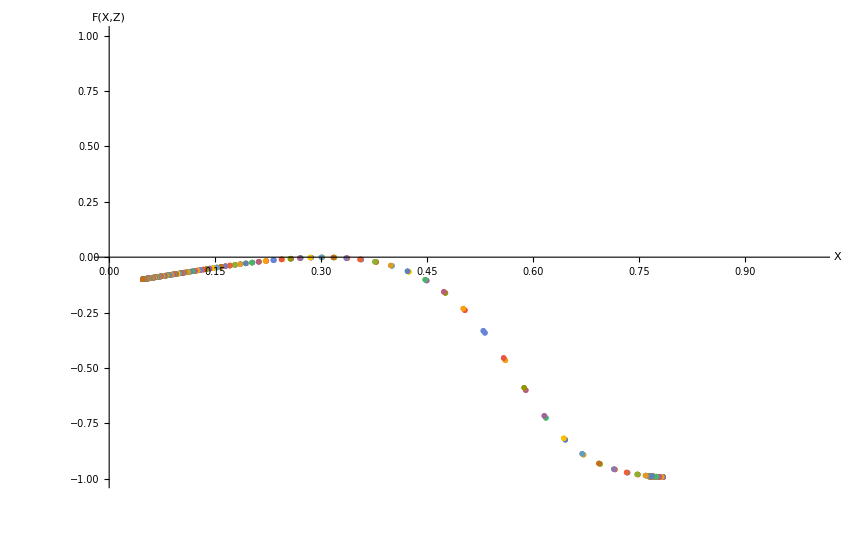

```mathematica
(*Plot X vs the remaining equation when Y' = 0*)
(*When F(X,Z) = 0, an Einstein point exists*)
EinsteinPlotLimitingCompactRepellor=ListPlot[EinsteinPointSolutionsLimitingCompactRepellor,PlotRange->{{0,1},{-1,1}},AxesLabel->{"X","F(X,Z)"}]
```

#### Plot the X-Y-Z Phase Space

```mathematica
(*Find the maximum value of K for this combination of X0 and Z0 such that Y0 is not imaginary*)
KMaxLimitingCompactRepellor=K/.Solve[Y0LimitingRepellor==0,K][[1]]
```

0.0352667

```mathematica
(*Solve trajLimitingCompact[K] for different values of K*)
```

```mathematica
solLimitingCompactRepellor[1]=trajLimitingCompactRepellor[KDensityParametersOpen]
```

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,0.,Indeterminate} is not a list of numbers with dimensions {3} at {t,X1[t],Y1[t],Z1[t]} = {-7.9808,0.76193,1.,0.000299282}.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solLimitingCompactRepellor[2]=trajLimitingCompactRepellor[KDensityParametersClosed]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solLimitingCompactRepellor[3]=trajLimitingCompactRepellor[-.1]
```

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,0.,Indeterminate} is not a list of numbers with dimensions {3} at {t,X1[t],Y1[t],Z1[t]} = {-2.82253,0.761968,1.,0.000757781}.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solLimitingCompactRepellor[4]=trajLimitingCompactRepellor[KMaxLimitingCompactRepellor]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solLimitingCompactRepellor[5]=trajLimitingCompactRepellor[0.005]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the trajectories for the different values of K given above.*)
(*Plot the solutions using a value of K found from the range of Ωk0 allowed by Planck 2018 in purple*)
```

```mathematica
trajLimitingCompactXYZRepellor[1]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactRepellor[1],{t,-7.97,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZRepellor[2]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactRepellor[2],{t,-100,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZRepellor[3]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactRepellor[3],{t,-2.81,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZRepellor[4]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactRepellor[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZRepellor[5]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactRepellor[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajLimitingCaseCompactRepellor=Table[trajLimitingCompactXYZRepellor[i],{i,1,5}];
```

```mathematica
(*Plot the Einstein fixed point*)
EinsteinFixedPointsLimitingCompactRepellor=ListPointPlot3D[{EinsteinPointLimitingCompactRepellor},PlotStyle->Black];
```

```mathematica
(*Solve theX-Y-Z system around the Einstein fixed point to plot the Closed Friedmann Separatrix (CFS)*)
CFSLimitingSolCompactRepellor=NDSolve[{deXt,deYt,deZt,X1[0]==EinsteinPointLimitingCompactRepellor[[1]],Y1[0]==0,Z1[0]==EinsteinPointLimitingCompactRepellor[[3]]},{X1,Y1,Z1},{t,-100,100}]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the CFS*)
CFSLimitingCompactRepellor=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.CFSLimitingSolCompactRepellor,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
(*Show the X-Y-Z phase space*)
Show[trajLimitingCaseCompactRepellor,EinsteinFixedPointsLimitingCompactRepellor,CFSLimitingCompactRepellor,AccnXYZRepellor,FPsXYZRepellor,CompactFPShowXYZRepellor,XYZCompactFormat]
```

-Graphics3D-

#### Plot the X-Z Projection

```mathematica
(*Plot one solution on the X-Z plane*)
trajLimitingCompactXZRepellor=ParametricPlot[Evaluate[{{Z1[t],X1[t]}}/.solLimitingCompactRepellor[1],{t,-7.97,100},PlotStyle -> {{Black, Thick,Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0,.03,0,.03,0},1]]],Arrow[x]};
```

```mathematica
(*Plot the Einstein fixed point on the X-Z plane*)
EinsteinFixedPointsLimitingCompactXZRepellor=ListPlot[{{EinsteinPointLimitingCompactRepellor[[3]],EinsteinPointLimitingCompactRepellor[[1]]}},PlotStyle->Black];
```

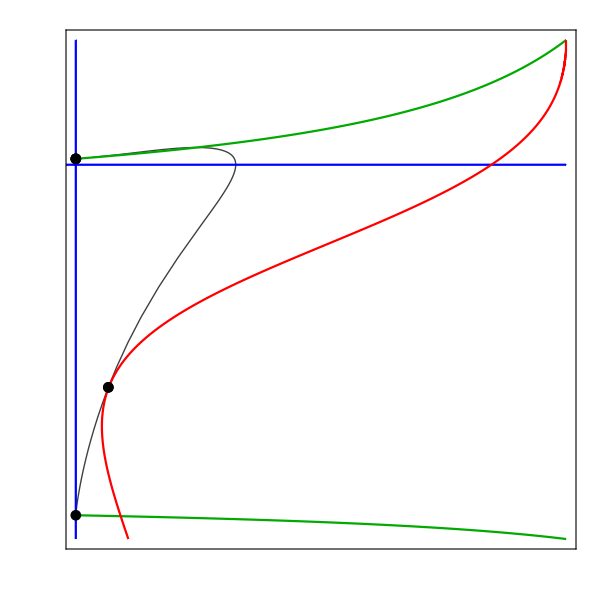

```mathematica
(*Show the X-Z phase space with the a'' = 0 (red), X' = 0 (green) and Z' = 0 (purple) curves*)
Show[trajLimitingCompactXZRepellor,XLineRepellor,ZLineRepellor,AccnXZRepellor,EinsteinFixedPointsLimitingCompactXZRepellor,FPsXZRepellor,CompactFPShowXZRepellor,XZCompactFormat]
```

### Two Einstein Fixed Points

#### Find the Einstein Fixed Points

```mathematica
(*Fix z0 using the density parameters*)
z0TwoEinsteinPointsRepellor=Ωm0*ℛ/(Ωx0*α);
```

```mathematica
(*Compactify z0*)
Z0TwoEinsteinPointsRepellor=z0TwoEinsteinPointsRepellor/(1+z0TwoEinsteinPointsRepellor)
```

0.0432077

```mathematica
(*Substitute Z0TwoEinsteinPoints into Y0 for this case*)
Y0TwoEinsteinPointsRepellor=Y0/.Z0->Z0TwoEinsteinPointsRepellor
```

(√(0.0483863-K))/(√(1.04839-K))

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajTwoEinsteinPointsCompactRepellor[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0TwoEinsteinPointsRepellor,Z1[0]==Z0TwoEinsteinPointsRepellor},{X1,Y1,Z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition (√(0.0483863-1. K))/(√(1.04839-1. K)) is not a number or a rectangular array of numbers.

NDSolve[{X1'[t]==-(3 (0.8 (1-X1[t])-0.25 X1[t]) (-0.05 (1-X1[t])+X1[t]) Y1[t])/(√(1-Y1[t]^2))-((1-X1[t]) X1[t] Y1[t] Z1[t])/(√(1-Y1[t]^2) (1-Z1[t])),Y1'[t]==-Y1[t]^2 √(1-Y1[t]^2)-1/6 (1-Y1[t]^2)^(3/2) (-0.12+(0.4375 X1[t])/(1-X1[t])-(0.75 X1[t]^2)/(1-X1[t])^2+Z1[t]/(1-Z1[t])),Z1'[t]==-(3 Y1[t] (1-Z1[t]) Z1[t])/(√(1-Y1[t]^2))+(X1[t] Y1[t] (1-Z1[t]) Z1[t])/((1-X1[t]) √(1-Y1[t]^2)),X1[0]==0.0909091,Y1[0]==(√(0.0483863-K))/(√(1.04839-K)),Z1[0]==0.0432077},{X1,Y1,Z1},{t,-100,100}]

```mathematica
(*Set-up tables of X1 and Z1 values to be used to find the X and Z value of the first Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
XTableSol1TwoEinsteinPointsCompactRepellor=Table[X1[i]/.trajTwoEinsteinPointsCompactRepellor[0],{i,-2,100,.01}];
ZTableSol1TwoEinsteinPointsCompactRepellor=Table[Z1[i]/.trajTwoEinsteinPointsCompactRepellor[0],{i,-2,100,.01}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol1TwoEinsteinPointsCompactRepellor=(ZTableSol1TwoEinsteinPointsCompactRepellor/(1-ZTableSol1TwoEinsteinPointsCompactRepellor))+(XTableSol1TwoEinsteinPointsCompactRepellor/(1-XTableSol1TwoEinsteinPointsCompactRepellor))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSol1TwoEinsteinPointsCompactRepellor/(1-XTableSol1TwoEinsteinPointsCompactRepellor))^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol1TwoEinsteinPointsCompact that is closest to zero. When EinsteinPlotValuesSol1TwoEinsteinPointsCompact = 0 (Y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints1CompactRepellor=Flatten[Nearest[EinsteinPlotValuesSol1TwoEinsteinPointsCompactRepellor,0]]
```

{-0.000146736}

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints1Compact in the EinsteinPlotValuesSol1TwoEinsteinPointsCompact*)
PositionNearestToZeroTwoEinsteinPoints1CompactRepellor=Flatten[Position[EinsteinPlotValuesSol1TwoEinsteinPointsCompactRepellor,NearestToZeroTwoEinsteinPoints1CompactRepellor]]
```

{125}

```mathematica
(*Find the Einstein point by finding the X and Z values in XTableSol1TwoEinsteinPointsCompact and ZTableSol1TwoEinsteinPointsCompact at PositionNearestToZeroTwoEinsteinPoints1Compact*)
EinsteinPoint1TwoEinsteinPointsCompactRepellor=Flatten[{XTableSol1TwoEinsteinPointsCompactRepellor[[PositionNearestToZeroTwoEinsteinPoints1CompactRepellor]],0,ZTableSol1TwoEinsteinPointsCompactRepellor[[PositionNearestToZeroTwoEinsteinPoints1CompactRepellor]]}]
```

{0.113148,0,0.0708422}

```mathematica
(*Set-up tables of X1 and Z1 values to be used to find the X and Z value of the second Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
XTableSol2TwoEinsteinPointsCompactRepellor=Table[X1[i]/.trajTwoEinsteinPointsCompactRepellor[0],{i,-5.6,-3.2,.001}];
ZTableSol2TwoEinsteinPointsCompactRepellor=Table[Z1[i]/.trajTwoEinsteinPointsCompactRepellor[0],{i,-5.6,-3.2,.001}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol2TwoEinsteinPointsCompactRepellor=(ZTableSol2TwoEinsteinPointsCompactRepellor/(1-ZTableSol2TwoEinsteinPointsCompactRepellor))+(XTableSol2TwoEinsteinPointsCompactRepellor/(1-XTableSol2TwoEinsteinPointsCompactRepellor))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSol2TwoEinsteinPointsCompactRepellor/(1-XTableSol2TwoEinsteinPointsCompactRepellor))^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol2TwoEinsteinPointsCompact that is closest to zero. When EinsteinPlotValuesSol2TwoEinsteinPointsCompact = 0 (Y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints2CompactRepellor=Flatten[Nearest[EinsteinPlotValuesSol2TwoEinsteinPointsCompactRepellor,0]]
```

{-0.00133878}

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints2Compact in the EinsteinPlotValuesSol2TwoEinsteinPointsCompact array*)
PositionNearestToZeroTwoEinsteinPoints2CompactRepellor=Flatten[Position[EinsteinPlotValuesSol2TwoEinsteinPointsCompactRepellor,NearestToZeroTwoEinsteinPoints2CompactRepellor]]
```

{2349}

```mathematica
(*Find the Einstein point by finding the X and Z values in XTableSol2TwoEinsteinPointsCompact and ZTableSol2TwoEinsteinPointsCompact at PositionNearestToZeroTwoEinsteinPoints2Compact*)
EinsteinPoint2TwoEinsteinPointsCompactRepellor=Flatten[{XTableSol2TwoEinsteinPointsCompactRepellor[[PositionNearestToZeroTwoEinsteinPoints2CompactRepellor]],0,ZTableSol2TwoEinsteinPointsCompactRepellor[[PositionNearestToZeroTwoEinsteinPoints2CompactRepellor]]}]
```

{0.617954,0,0.578629}

```mathematica
(*Put the Einstein fixed points into a common variable name*)
EinsteinPointTwoEPtsCompactRepellor[1]=EinsteinPoint1TwoEinsteinPointsCompactRepellor;
EinsteinPointTwoEPtsCompactRepellor[2]=EinsteinPoint2TwoEinsteinPointsCompactRepellor;
```

```mathematica
(*Put the Einstein fixed points into a table*)
EinsteinPointsTwoEPtsCompactRepellor=Table[EinsteinPointTwoEPtsCompactRepellor[i],{i,1,2}];
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each Einstein fixed point*)
EinsteinPointTableTwoEinsteinPointsCompactRepellor=Table[{EinsteinPointsTwoEPtsCompactRepellor[[i]]//MatrixForm,Simplify[JCompactXYZRepellor/.{X->EinsteinPointsTwoEPtsCompactRepellor[[i,1]],Y->EinsteinPointsTwoEPtsCompactRepellor[[i,2]],Z->EinsteinPointsTwoEPtsCompactRepellor[[i,3]]}]//MatrixForm,Eigenvalues[JCompactXYZRepellor/.{X->EinsteinPointsTwoEPtsCompactRepellor[[i,1]],Y->EinsteinPointsTwoEPtsCompactRepellor[[i,2]],Z->EinsteinPointsTwoEPtsCompactRepellor[[i,3]]}]//MatrixForm,Eigenvectors[JCompactXYZRepellor/.{X->EinsteinPointsTwoEPtsCompactRepellor[[i,1]],Y->EinsteinPointsTwoEPtsCompactRepellor[[i,2]],Z->EinsteinPointsTwoEPtsCompactRepellor[[i,3]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the Einstein fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableTwoEinsteinPointsCompactRepellor=TableForm[EinsteinPointTableTwoEinsteinPointsCompactRepellor,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.113148
0
0.0708422) | (0. | -0.148261 | 0.
-0.0521555 | 0. | -0.19305
0. | -0.189073 | 0.) | (-0.210317
0.210317
7.07944×10^-18) | (0.464307 | 0.658647 | 0.592117
0.464307 | -0.658647 | 0.592117
-0.965389 | 7.23655×10^-17 | 0.260815)
(0.617954
0
0.578629) | (0. | -0.595742 | 0.
2.27087 | 0. | -0.938684
0. | -0.337081 | 0.) | (-3.12568×10^-16+1.01806 ⅈ
-3.12568×10^-16-1.01806 ⅈ
1.2123×10^-16+0. ⅈ) | (-1.7397×10^-16+0.485617 ⅈ | 0.829866+0. ⅈ | -5.7413×10^-17+0.274771 ⅈ
-1.7397×10^-16-0.485617 ⅈ | 0.829866+0. ⅈ | -5.7413×10^-17-0.274771 ⅈ
0.382009+0. ⅈ | -1.14998×10^-15+0. ⅈ | 0.924159+0. ⅈ)

```mathematica
(*Set-up tables of all X1 and Z1 values*)
XTableSolTwoEinsteinPointsFullCompactRepellor=Table[X1[i]/.trajTwoEinsteinPointsCompactRepellor[0],{i,-100,100,.1}];
ZTableSolTwoEinsteinPointsFullCompactRepellor=Table[Z1[i]/.trajTwoEinsteinPointsCompactRepellor[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0*)
EinsteinPlotValuesSolTwoEinsteinPointsFullXZRepellor=(ZTableSolTwoEinsteinPointsFullCompactRepellor/(1-ZTableSolTwoEinsteinPointsFullCompactRepellor))+(XTableSolTwoEinsteinPointsFullCompactRepellor/(1-XTableSolTwoEinsteinPointsFullCompactRepellor))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSolTwoEinsteinPointsFullCompactRepellor/(1-XTableSolTwoEinsteinPointsFullCompactRepellor))^2;
```

```mathematica
(*Compactify EinsteinPlotValuesSolTwoEinsteinPointsFullXZ*)
EinsteinPlotValuesSolTwoEinsteinPointsFullCompactRepellor=EinsteinPlotValuesSolTwoEinsteinPointsFullXZRepellor/Sqrt[1+EinsteinPlotValuesSolTwoEinsteinPointsFullXZRepellor^2];
```

```mathematica
(*Merge the XTableSolTwoEinsteinPointsFullCompact values and the EinsteinPlotValuesSolTwoEinsteinPointsFullCompact values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsTwoEinsteinPointsCompactRepellor=MapThread[h,{XTableSolTwoEinsteinPointsFullCompactRepellor,EinsteinPlotValuesSolTwoEinsteinPointsFullCompactRepellor}];
```

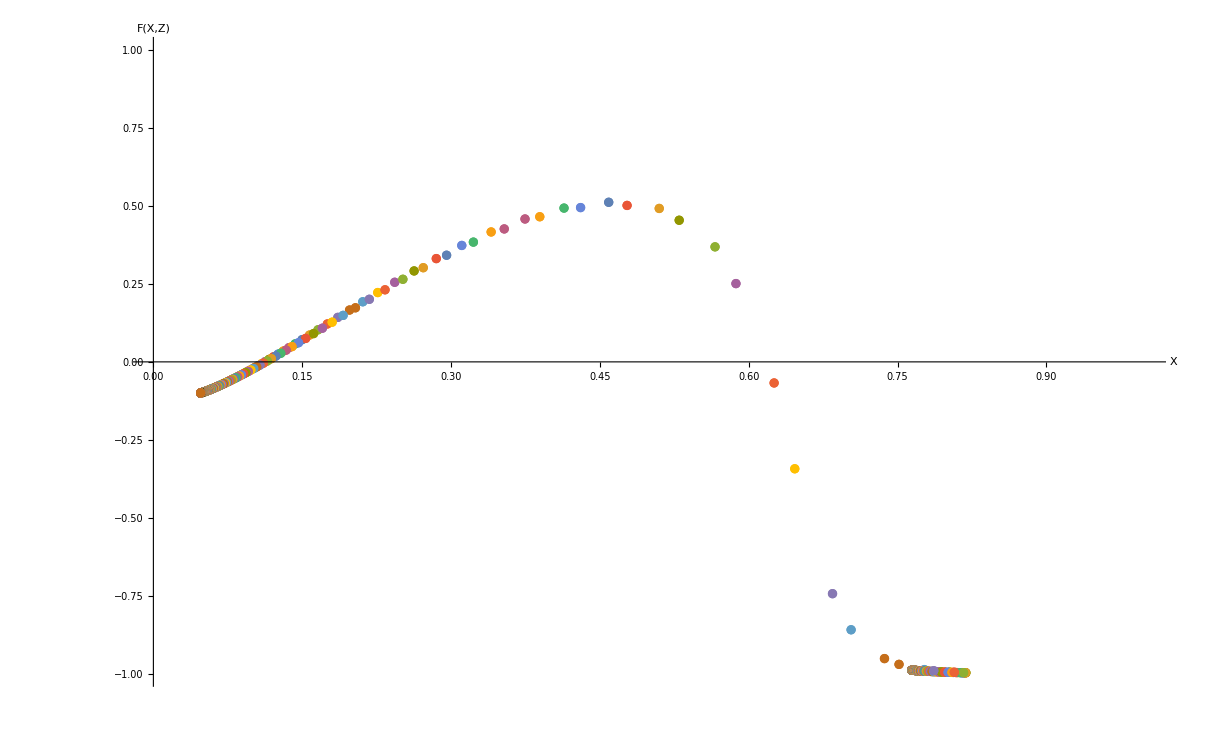

```mathematica
(*Plot X vs the remaining equation when Y' = 0*)
(*When F(X,Z) = 0, an Einstein point exists*)
EinsteinPlotTwoEinsteinPointsCompactRepellor=ListPlot[EinsteinPointSolutionsTwoEinsteinPointsCompactRepellor,PlotRange->{{0,1},{-1,1}},AxesLabel->{"X","F(X,Z)"}]
```

#### Plot the X-Y-Z Phase Space

```mathematica
(*Find the maximum value of K for this combination of X0 and Z0 so that Y0 is not imaginary*)
KMaxTwoEinsteinPointsCompactRepellor=K/.Flatten[Solve[Y0TwoEinsteinPointsRepellor==0,K]]
```

0.0483863

```mathematica
(*Solve trajTwoEinsteinPointsCompact[K] for different values of K*)
```

```mathematica
solTwoEinsteinPointsCompactRepellor[1]=trajTwoEinsteinPointsCompactRepellor[KDensityParametersOpen]
```

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,0.,Indeterminate} is not a list of numbers with dimensions {3} at {t,X1[t],Y1[t],Z1[t]} = {-6.53759,0.76194,1.,0.000424237}.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsCompactRepellor[2]=trajTwoEinsteinPointsCompactRepellor[KDensityParametersClosed]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsCompactRepellor[3]=trajTwoEinsteinPointsCompactRepellor[-.1]
```

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,0.,Indeterminate} is not a list of numbers with dimensions {3} at {t,X1[t],Y1[t],Z1[t]} = {-2.61973,0.76193,1.,0.000299232}.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsCompactRepellor[4]=trajTwoEinsteinPointsCompactRepellor[KMaxTwoEinsteinPointsCompactRepellor]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsCompactRepellor[5]=trajTwoEinsteinPointsCompactRepellor[0.025]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the trajectories for the different values of K given above*)
(*Plot the solutions using a value of K found from the range of Ωk0 allowed by Planck 2018 in purple*)
```

```mathematica
trajTwoEinsteinPointsCompactXYZRepellor[1]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactRepellor[1],{t,-6.535,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsCompactXYZRepellor[2]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactRepellor[2],{t,-100,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsCompactXYZRepellor[3]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactRepellor[3],{t,-2.615,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsCompactXYZRepellor[4]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactRepellor[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
trajTwoEinsteinPointsCompactXYZRepellor[5]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactRepellor[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Solve the X-Y-Z system using the centre Einstein fixed point for X0 and Z0 to plot a cyclic trajectory*)
CyclicTrajTwoEinsteinPointsCompactRepellor=NDSolve[{deXt,deYt,deZt,X1[0]==EinsteinPoint2TwoEinsteinPointsCompactRepellor[[1]],Y1[0]==0.35,Z1[0]==EinsteinPoint2TwoEinsteinPointsCompactRepellor[[3]]},{X1,Y1,Z1},{t,-100,100}];
```

```mathematica
(*Plot the cyclic trajectory*)
trajTwoEinsteinPointsCompactXYZRepellor[6]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.CyclicTrajTwoEinsteinPointsCompactRepellor,{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajTwoEinsteinPointsCaseCompactRepellor=Table[trajTwoEinsteinPointsCompactXYZRepellor[i],{i,1,6}];
```

```mathematica
(*Plot the Einstein fixed points*)
EinsteinFixedPointsTwoEinsteinPointsCompactRepellor=ListPointPlot3D[{EinsteinPoint1TwoEinsteinPointsCompactRepellor,EinsteinPoint2TwoEinsteinPointsCompactRepellor},PlotStyle->Black];
```

```mathematica
(*Solve the X-Y-Z system around the Einstein fixed point to plot the Closed Friedmann Separatrix (CFS)*)
CFSTwoEinsteinPointsSolCompactRepellor=NDSolve[{deXt,deYt,deZt,X1[0]==EinsteinPoint1TwoEinsteinPointsCompactRepellor[[1]],Y1[0]==-0.0005,Z1[0]==EinsteinPoint1TwoEinsteinPointsCompactRepellor[[3]]},{X1,Y1,Z1},{t,-100,100}]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the CFS*)
CFSTwoEinsteinPointsCompactRepellor=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.CFSTwoEinsteinPointsSolCompactRepellor,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Show the X-Y-Z phase space*)
Show[trajTwoEinsteinPointsCaseCompactRepellor,CFSTwoEinsteinPointsCompactRepellor,EinsteinFixedPointsTwoEinsteinPointsCompactRepellor,AccnXYZRepellor,FPsXYZRepellor,CompactFPShowXYZRepellor,XYZCompactFormat]
```

-Graphics3D-

#### Plot the X-Z Projection

```mathematica
(*Plot one solution on the X-Z plane*)
trajTwoEinsteinPointsCompactXZRepellor=ParametricPlot[Evaluate[{{Z1[t],X1[t]}}/.solTwoEinsteinPointsCompactRepellor[1],{t,-6.5375,100},PlotStyle -> {{Black,Thick, Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.03,0,.03,0},1]]],Arrow[x]};
```

```mathematica
(*Plot the Einstein fixed points on the X-Z plane*)
EinsteinFixedPointsTwoEinsteinPointsCompactXZRepellor=ListPlot[{{EinsteinPoint1TwoEinsteinPointsCompactRepellor[[3]],EinsteinPoint1TwoEinsteinPointsCompactRepellor[[1]]},{EinsteinPoint2TwoEinsteinPointsCompactRepellor[[3]],EinsteinPoint2TwoEinsteinPointsCompactRepellor[[1]]}},PlotStyle->Black];
```

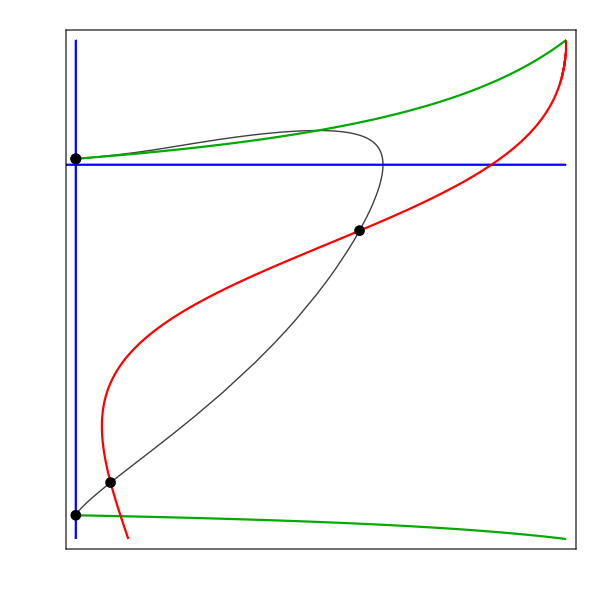

```mathematica
(*Show the X-Z phase space with the a'' = 0 (red), X' = 0 (green) and Z' = 0 (purple) curves*)
Show[trajTwoEinsteinPointsCompactXZRepellor,XLineRepellor,ZLineRepellor,AccnXZRepellor,EinsteinFixedPointsTwoEinsteinPointsCompactXZRepellor,FPsXZRepellor,CompactFPShowXZRepellor,XZCompactFormat]
```

### No Einstein Fixed Points

#### Plot to show there are no Einstein fixed points

```mathematica
(*Fix z0 such that there are no Einstein fixed points on the surface*)
z0NoEinsteinPointsRepellor=0.003;
```

```mathematica
(*Compactify z0*)
Z0NoEinsteinPointsRepellor=z0NoEinsteinPointsRepellor/(1+z0NoEinsteinPointsRepellor)
```

0.00299103

```mathematica
(*Substitute Z0NoEinsteinPoints into Y0 for this case*)
Y0NoEinsteinPointsRepellor=Y0/.Z0->Z0NoEinsteinPointsRepellor
```

(√(0.0343333-K))/(√(1.03433-K))

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajNoEinsteinPointsCompactRepellor[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0NoEinsteinPointsRepellor,Z1[0]==Z0NoEinsteinPointsRepellor},{X1,Y1,Z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition (√(0.0343333-1. K))/(√(1.03433-1. K)) is not a number or a rectangular array of numbers.

NDSolve[{X1'[t]==-(3 (0.8 (1-X1[t])-0.25 X1[t]) (-0.05 (1-X1[t])+X1[t]) Y1[t])/(√(1-Y1[t]^2))-((1-X1[t]) X1[t] Y1[t] Z1[t])/(√(1-Y1[t]^2) (1-Z1[t])),Y1'[t]==-Y1[t]^2 √(1-Y1[t]^2)-1/6 (1-Y1[t]^2)^(3/2) (-0.12+(0.4375 X1[t])/(1-X1[t])-(0.75 X1[t]^2)/(1-X1[t])^2+Z1[t]/(1-Z1[t])),Z1'[t]==-(3 Y1[t] (1-Z1[t]) Z1[t])/(√(1-Y1[t]^2))+(X1[t] Y1[t] (1-Z1[t]) Z1[t])/((1-X1[t]) √(1-Y1[t]^2)),X1[0]==0.0909091,Y1[0]==(√(0.0343333-K))/(√(1.03433-K)),Z1[0]==0.00299103},{X1,Y1,Z1},{t,-100,100}]

```mathematica
(*Set-up tables of all X1 and Z1 values*)
XTableSolNoEinsteinPointsFullCompactRepellor=Table[X1[i]/.trajNoEinsteinPointsCompactRepellor[0],{i,-100,100,.1}];
ZTableSolNoEinsteinPointsFullCompactRepellor=Table[Z1[i]/.trajNoEinsteinPointsCompactRepellor[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0*)
EinsteinPlotValuesSolNoEinsteinPointsFullCompactRepellor=(ZTableSolNoEinsteinPointsFullCompactRepellor/(1-ZTableSolNoEinsteinPointsFullCompactRepellor))+(XTableSolNoEinsteinPointsFullCompactRepellor/(1-XTableSolNoEinsteinPointsFullCompactRepellor))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSolNoEinsteinPointsFullCompactRepellor/(1-XTableSolNoEinsteinPointsFullCompactRepellor))^2;
```

```mathematica
(*Compactify EinsteinPlotValuesSolNoEinsteinPointsFullCompact*)
EinsteinPlotValuesSolNoEinsteinPointsFullXZRepellor=EinsteinPlotValuesSolNoEinsteinPointsFullCompactRepellor/Sqrt[1+EinsteinPlotValuesSolNoEinsteinPointsFullCompactRepellor^2];
```

```mathematica
(*Merge the XTableSolNoEinsteinPointsFullCompact values and the EinsteinPlotValuesSolNoEinsteinPointsFullXZ values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsNoEinsteinPointsCompactRepellor=MapThread[h,{XTableSolNoEinsteinPointsFullCompactRepellor,EinsteinPlotValuesSolNoEinsteinPointsFullXZRepellor}];
```

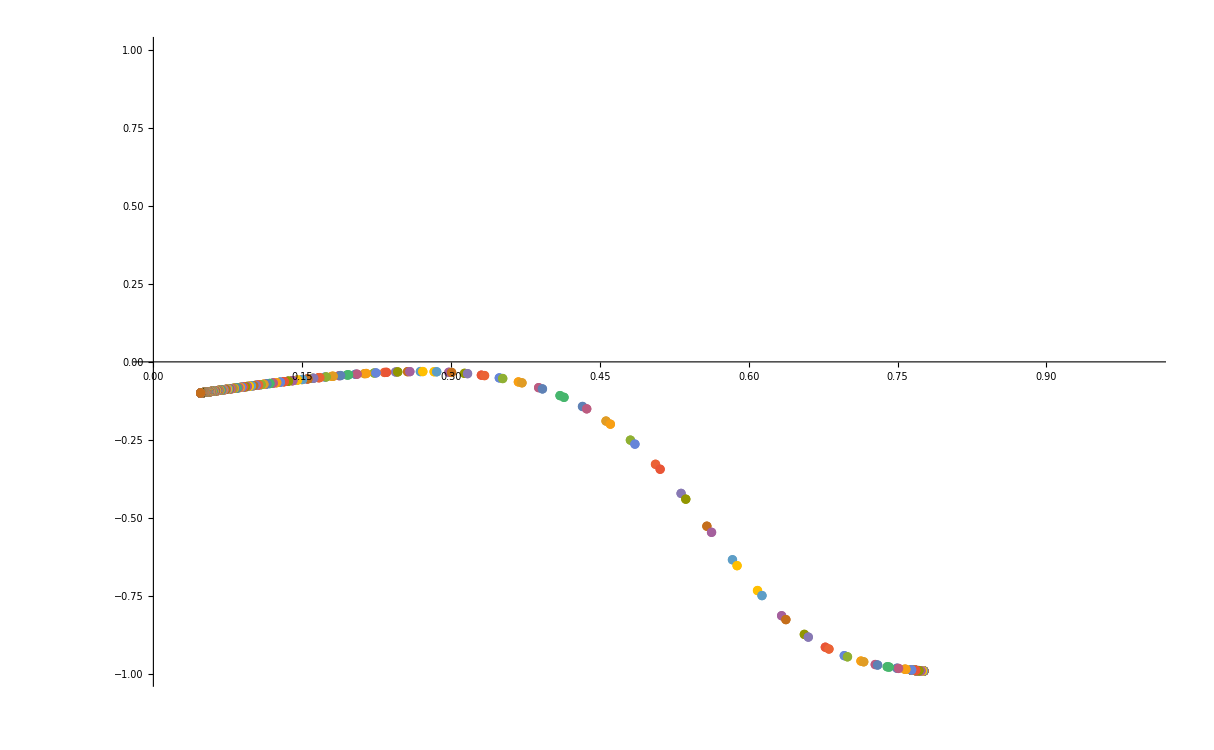

```mathematica
(*Plot X vs the remaining equation when Y' = 0*)
(*Here, F(X,Z) is never zero, so there are no Einstein fixed points*)
EinsteinPlotNoEinsteinPointsCompactRepellor=ListPlot[EinsteinPointSolutionsNoEinsteinPointsCompactRepellor,PlotRange->{{0,1},{-1,1}}]
```

#### Plot the X-Y-Z Phase Space

```mathematica
(*Find the maximum value of K for this combination of X0 and Z0 such that Y0 is not imaginary*)
KMaxNoEinsteinPointsCompactRepellor=K/.Solve[Y0NoEinsteinPointsRepellor==0,K][[1]]
```

0.0343333

```mathematica
(*Solve trajNoEinsteinPointsCompact[K] for different values of K*)
```

```mathematica
solNoEinsteinPointsCompactRepellor[1]=trajNoEinsteinPointsCompactRepellor[KDensityParametersOpen]
```

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,0.,Indeterminate} is not a list of numbers with dimensions {3} at {t,X1[t],Y1[t],Z1[t]} = {-8.24064,0.761957,1.,0.000616911}.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsCompactRepellor[2]=trajNoEinsteinPointsCompactRepellor[KDensityParametersClosed]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsCompactRepellor[3]=trajNoEinsteinPointsCompactRepellor[-.1]
```

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,0.,Indeterminate} is not a list of numbers with dimensions {3} at {t,X1[t],Y1[t],Z1[t]} = {-2.84158,0.761932,1.,0.000324898}.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsCompactRepellor[4]=trajNoEinsteinPointsCompactRepellor[0.01]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsCompactRepellor[5]=trajNoEinsteinPointsCompactRepellor[KMaxNoEinsteinPointsCompactRepellor]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the trajectories for the different values of K given above.*)
(*Plot the solutions using a value of K found from the range of Ωk0 allowed by Planck 2018 in purple*)
```

```mathematica
trajNoEinsteinPointsCompactXYZRepellor[1]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactRepellor[1],{t,-8.23,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZRepellor[2]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactRepellor[2],{t,-100,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZRepellor[3]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactRepellor[3],{t,-2.83,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZRepellor[4]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactRepellor[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZRepellor[5]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactRepellor[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajNoEinsteinPointsPlotsCompactRepellor=Table[trajNoEinsteinPointsCompactXYZRepellor[i],{i,1,5}];
```

```mathematica
(*Show the X-Y-Z phase space*)
Show[trajNoEinsteinPointsPlotsCompactRepellor,AccnXYZRepellor,FPsXYZRepellor,CompactFPShowXYZRepellor,XYZCompactFormat]
```

-Graphics3D-

#### Plot the X-Z Projection

```mathematica
(*Plot one solution on the X-Z plane*)
trajNoEinsteinPointsCompactXZRepellor=ParametricPlot[Evaluate[{{Z1[t],X1[t]}}/.solNoEinsteinPointsCompactRepellor[1],{t,-8.23,100},PlotStyle -> {{Black,Thick, Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0,.03,0,.03,0},1]]],Arrow[x]};
```

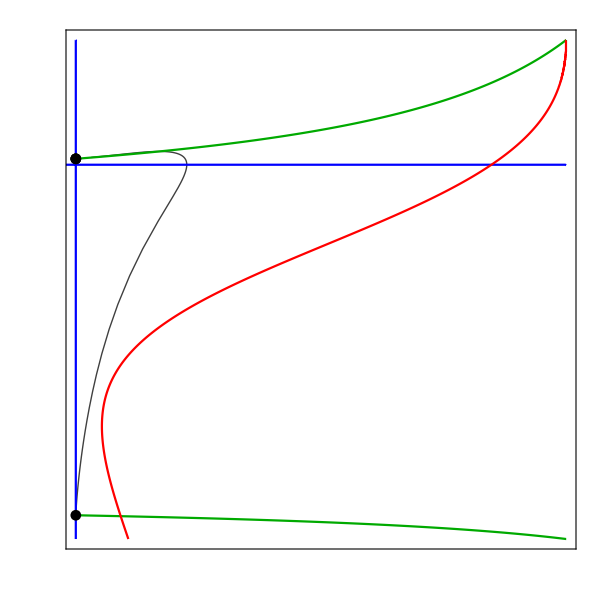

```mathematica
(*Show the X-Z phase space with the a'' = 0 (red), X' = 0 (green) and Z' = 0 (purple) curves*)
Show[trajNoEinsteinPointsCompactXZRepellor,XLineRepellor,ZLineRepellor,AccnXZRepellor,FPsXZRepellor,CompactFPShowXZRepellor,XZCompactFormat]
```

## Investigate system when ℛ = 10^(-120)

### Set-up

```mathematica
(*Clear variables*)
Clear[q,ϵ,ℛ,wx]
```

```mathematica
(*Set parameter values*)
q=1;
ϵ=-0.25;
ℛ=10^(-120);
wx=-0.2;
```

```mathematica
(*Define Ωx0 and Ωm0 using data from Planck 2018*)
Ωx0=0.6889;
Ωm0=0.3111;
```

```mathematica
(*Set a value for α, which sets the value of the low energy cosmological constant*)
α=0.5;
```

```mathematica
(*Define the initial conditions, where a0 = 1 and K is defined as k/ρ* *)

x0=ℛ/α;
y0=Sqrt[x0/3+Z0/(3*(1-Z0))-K];
```

```mathematica
(*Compactify the initial conditions*)

X0=x0/(1+x0);
Y0=y0/Sqrt[1+y0^2];
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y in terms of time, t*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*(X1[t]-ℛ*(1-X1[t]))*((1+wx)*(1-X1[t])+ϵ*X1[t])-q*X1[t]*(1-X1[t])*(Z1[t]/(1-Z1[t]))*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((Z1[t]/(1-Z1[t]))+(X1[t]/(1-X1[t]))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X1[t]^2/((1-X1[t])^2))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2))) + q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
```

### Find the value of z0 to give the limiting case

```mathematica
(*Fix z0 using the density parameters*)
z0RealisticℛRepellor=Ωm0*ℛ/(Ωx0*α)
```

9.03179×10^-121

```mathematica
(*Compactify z0*)
Z0RealisticℛRepellor=z0RealisticℛRepellor/(1+z0RealisticℛRepellor)
```

9.03179×10^-121

```mathematica
(*Substitute Z0Realisticℛ into Y0 for this case*)
Y0RealisticℛRepellor=Y0/.Z0->Z0RealisticℛRepellor
```

(√(9.67726×10^-121-K))/(√(1.-K))

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajRealisticℛRepellor[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0RealisticℛRepellor,Z1[0]==Z0RealisticℛRepellor},{X1,Y1,Z1},{t,-100,100}];
```

NDSolve::ndinnt: Initial condition (√(9.67726×10^-121-1. K))/(√(1.-1. K)) is not a number or a rectangular array of numbers.

```mathematica
(*Set-up tables of all X1 and Z1 values*)
XTableRealisticℛRepellor=Table[X1[i]/.trajRealisticℛRepellor[0],{i,-100,100,.1}];
ZTableRealisticℛRepellor=Table[Z1[i]/.trajRealisticℛRepellor[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0*)
EinsteinPlotValuesRealisticℛRepellor=(ZTableRealisticℛRepellor/(1-ZTableRealisticℛRepellor))+(XTableRealisticℛRepellor/(1-XTableRealisticℛRepellor))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableRealisticℛRepellor/(1-XTableRealisticℛRepellor))^2;
```

```mathematica
(*Compactify EinsteinPlotValuesRealisticℛ*)
EinsteinPlotRealisticℛCompactRepellor=EinsteinPlotValuesRealisticℛRepellor/Sqrt[1+EinsteinPlotValuesRealisticℛRepellor^2];
```

```mathematica
(*Find the maximum value of EinsteinPlotRealisticℛCompact*)
(*As EinsteinPlotRealisticℛCompact is always less than zero there are no Einstein points when z0 is defined using the density parameters*)
Max[EinsteinPlotRealisticℛCompactRepellor]
```

-6.96821×10^-121